# Group coherence Using the coefficient of variation (CV) to estimate changes in range shape and fragmentation N. Love and S. Otto (2026)

## Individuals distributed according to a bivariate normal

### Commands for simplifying terms [ENTER]

This section gives the list of constraints and summarizes the results to avoid having to reenter them:

```mathematica
constraints={σx>0,σy>0,σ>0,ρ≥0,Δx^2>0,Δy^2>0,Δz>0,c>0,Element[{σx,σy,ρ,Δx,Δy,Δz,c},Reals]};
```

Summarizing the results:

```mathematica
soln=(2 σx EllipticE[1-σy^2/σx^2])/(√π);
```

```mathematica
solnsq=2 (σx^2+σy^2);
```

```mathematica
CVherd=(√(1/2 π (σx^2+σy^2)-σx^2 EllipticE[1-σy^2/σx^2]^2))/(σx EllipticE[1-σy^2/σx^2]);
```

The results below assume σx=σy=σ:

```mathematica
indsoln=1.7724538509056207 σ;
indsolnsq=3.3412233051393185 σ^2;
```

```mathematica
CVind=0.2520801657678077; (*Symmetric single patch*)
CVind1=√(-1+1/12 (6 √3+π));(*Extremely elongated single patch*)

solnC=(1-f) √π σ+1/4 ⅇ^(-Subscript[c, S]^2/8) f √π σ (BesselI[1,Subscript[c, S]^2/8] Subscript[c, S]^2+BesselI[0,Subscript[c, S]^2/8] (4+Subscript[c, S]^2));
```

```mathematica
solnsqC=4 (1-f) σ^2+f σ^2 (4+Subscript[c, S]^2);
```

```mathematica
CVherdC=Sqrt[(16 ⅇ^(Subscript[c, S]^2/4) (4+f Subscript[c, S]^2))/(π (4 ⅇ^(Subscript[c, S]^2/8) (1-f)+f BesselI[1,Subscript[c, S]^2/8] Subscript[c, S]^2+f BesselI[0,Subscript[c, S]^2/8] (4+Subscript[c, S]^2))^2)-1]/.Subscript[c, S]->c/σ;
```

A herd split in two with a chance f of drawing from different patches has a CVind of:

```mathematica
CVindfarsplit=√((1/2-f)/f);
```

A very elongated herd:

```mathematica
CVherd1=Limit[CVherd,σx->Infinity]
```

√(1/2 (-2+π))

For comparison, we can numerically integrate the function for a given parameter set.

For the herd-level CV, we can use analytical results where available:

mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
sqH=(1-f) solnsq+f (c^2+2 (σx^2+σy^2))/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;:

The individual-level CV first requires  integration of the average distance of an individual to any other. Analytical results are only available for the average distance in the symmetric Gaussian case (σx=σy):

```mathematica
Solve[2 p (1-p)==f,p]
```

{{p→1/2 (1-√(1-2 f))},{p→1/2 (1+√(1-2 f))}}

```mathematica
avedist[x2_?NumericQ,y2_?NumericQ,σ_?NumericQ,c_?NumericQ]:=√(π/2) σ LaguerreL[1/2,-((c+x2)^2+y2^2)/(2 σ^2)]; (*c is displacement along x-axis*)
sqI[σ_?NumericQ,c_?NumericQ,f_?NumericQ]:=NIntegrate[((p1*(p1*avedist[x2,y2,σ,0]+p2*avedist[x2,y2,σ,c])^2+p2*(p1*avedist[x2,y2,σ,-c]+p2*avedist[x2,y2,σ,0])^2)/.p2->1-p1/.p1->1/2 (1-√(1-2 f)))PDF[MultinormalDistribution[{0,0},{{σ^2,0},{0,σ^2}}],{x2,y2}],{x2,-tryLIM,tryLIM},{y2,-tryLIM,tryLIM}];
```

A much slower integration is needed to first find the average distance in the asymmetrical case:

```mathematica
avedist[x2_?NumericQ,y2_?NumericQ,σx_?NumericQ,σy_?NumericQ,c_?NumericQ]:=NIntegrate[Sqrt[((x2-x1)^2+(y2-y1)^2)]PDF[MultinormalDistribution[{c,0},{{σx^2,0},{0,σy^2}}],{x1,y1}],{x1,-tryLIM,tryLIM},{y1,-tryLIM,tryLIM}];
sqI[σx_?NumericQ,σy_?NumericQ,c_?NumericQ,f_?NumericQ]:=NIntegrate[((p1*(p1*avedist[x2,y2,σx,σy,0]+p2*avedist[x2,y2,σx,σy,c])^2+p2*(p1*avedist[x2,y2,σx,σy,-c]+p2*avedist[x2,y2,σx,σy,0])^2)/.p2->1-p1/.p1->1/2 (1-√(1-2 f)))*PDF[MultinormalDistribution[{0,0},{{σx^2,0},{0,σy^2}}],{x2,y2}],{x2,-tryLIM,tryLIM},{y2,-tryLIM,tryLIM}];
```

When c=0 (no split), we can speed up the integration:

```mathematica
sqI[σx_?NumericQ,σy_?NumericQ]:=NIntegrate[(avedist[x2,y2,σx,σy,0])^2*PDF[MultinormalDistribution[{0,0},{{σx^2,0},{0,σy^2}}],{x2,y2}],{x2,-tryLIM,tryLIM},{y2,-tryLIM,tryLIM}];
```

When f=1/2 (even split), we can also speed up the integration (recognizing that the average distance for -c and for +c are equal):

```mathematica
sqI[σx_?NumericQ,σy_?NumericQ,c_?NumericQ]:=NIntegrate[(1/2*avedist[x2,y2,σx,σy,0]+1/2*avedist[x2,y2,σx,σy,c])^2*PDF[MultinormalDistribution[{0,0},{{σx^2,0},{0,σy^2}}],{x2,y2}],{x2,-tryLIM,tryLIM},{y2,-tryLIM,tryLIM}];
```

### Analysis

#### E[X]: Average distance among all pairs

Consider a simplified range that is Gaussian in shape with mean 0, standard deviation σx and σy, and correlation structure ρ:

```mathematica
PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{x,y}]
```

(ⅇ^(1/2 (-(x (y ρ σx-x σy))/((-1+ρ^2) σx^2 σy)-(y (-y σx+x ρ σy))/((-1+ρ^2) σx σy^2))))/(2 π √(σx^2 σy^2-ρ^2 σx^2 σy^2))

```mathematica
Manipulate[
Plot3D[PDF[MultinormalDistribution[{0,0},{{1,ρ },{ρ ,1}}],{x,y}],{x,-2,2},{y,-2,2}],
{ρ,0,1}]
```

The average pairwise distance is obtained by integrating over all positions of one individual {x1,y1} and then all positions of the second individual {x2,y2}, all of which are real numbers within the range.

```mathematica
Simplify[Sqrt[(x2-x1)^2+(y2-y1)^2]PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{x1,y1}]PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{x2,y2}]]/.ρ->0
```

(ⅇ^(-(y1^2 σx^2+y2^2 σx^2+(x1^2+x2^2) σy^2)/(2 σx^2 σy^2)) √((x1-x2)^2+(y1-y2)^2))/(4 π^2 σx^2 σy^2)

Unfortunately, this does not integrate directly:

```mathematica
Integrate[%,x1]
```

(∫ⅇ^(-(y1^2 σx^2+y2^2 σx^2+(x1^2+x2^2) σy^2)/(2 σx^2 σy^2)) √((x1-x2)^2+(y1-y2)^2)ⅆx1)/(4 π^2 σx^2 σy^2)

We work instead with Δx=x2-x1 and Δy=y2-y1, which simplifies the integration:

```mathematica
Simplify[Sqrt[Δx^2+Δy^2]PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{x1,y1}]PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{Δx+x1,Δy+y1}]]/.ρ->0
```

(ⅇ^(-(2 y1^2 σx^2+2 y1 Δy σx^2+Δy^2 σx^2+(2 x1^2+2 x1 Δx+Δx^2) σy^2)/(2 σx^2 σy^2)) √(Δx^2+Δy^2))/(4 π^2 σx^2 σy^2)

```mathematica
Simplify[Integrate[%,{x1,-Infinity,Infinity}],constraints]
```

(ⅇ^(1/4 (-Δx^2/σx^2-(2 (2 y1^2+2 y1 Δy+Δy^2))/σy^2)) √(Δx^2+Δy^2))/(4 π^(3/2) σx σy^2)

```mathematica
Simplify[Integrate[%,{y1,-Infinity,Infinity}],constraints]
```

(ⅇ^(-Δx^2/(4 σx^2)-Δy^2/(4 σy^2)) √(Δx^2+Δy^2))/(4 π σx σy)

```mathematica
Simplify[Integrate[%,{Δy,-Infinity,Infinity}],constraints]
```

(ⅇ^(-Δx^2/(4 σx^2)) σy HypergeometricU[-1/2,0,Δx^2/(4 σy^2)])/(√π σx)

[Note that the order was reversed, first Δy and then Δx, to get the term in the EllipticE to be between 0 and 1 when σx is assumed to be the major axis.]

```mathematica
soln=Simplify[Integrate[%,{Δx,-Infinity,Infinity}],constraints]
```

(2 σx EllipticE[1-σy^2/σx^2])/(√π)

where EllipticE is the complete integral over the ellipse of ∫_0^(π/2) (1-m sin^2(θ))^(1/2)ⅆθ

```mathematica
soln=(2 σx EllipticE[1-σy^2/σx^2])/(√π);
```

```mathematica
soln/.σx->σ/.σy->σ//Simplify
```

√π σ

```mathematica
soln/.ρ->0/.σx->0.5/.σy->2.
```

2.41993

```mathematica
Simplify[Sqrt[(x2-x1)^2+(y2-y1)^2]PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{x1,y1}]PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{x2,y2}]]/.ρ->0/.σx->1/2/.σy->2;
NIntegrate[%,{x1,-Infinity,Infinity},{x2,-Infinity,Infinity},{y1,-Infinity,Infinity},{y2,-Infinity,Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.41984 and 0.000600329 for the integral and error estimates.

2.41984

Significance: By knowing the area and shape of herd home ranges (or schools of fish, flocks of birds, etc.), we can estimate the average distance between individuals, here assuming a Gaussian distribution.

#### E[X^2]: Average distance among all pairs

```mathematica
Simplify[(Δx^2+Δy^2)PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{x1,y1}]PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{Δx+x1,Δy+y1}]]/.ρ->0
```

(ⅇ^(-(2 y1^2 σx^2+2 y1 Δy σx^2+Δy^2 σx^2+(2 x1^2+2 x1 Δx+Δx^2) σy^2)/(2 σx^2 σy^2)) (Δx^2+Δy^2))/(4 π^2 σx^2 σy^2)

```mathematica
Simplify[Integrate[%,{x1,-Infinity,Infinity}],constraints]
```

(ⅇ^(1/4 (-Δx^2/σx^2-(2 (2 y1^2+2 y1 Δy+Δy^2))/σy^2)) (Δx^2+Δy^2))/(4 π^(3/2) σx σy^2)

```mathematica
Simplify[Integrate[%,{y1,-Infinity,Infinity}],constraints]
```

(ⅇ^(-Δx^2/(4 σx^2)-Δy^2/(4 σy^2)) (Δx^2+Δy^2))/(4 π σx σy)

```mathematica
Simplify[Integrate[%,{Δx,-Infinity,Infinity}],constraints]
```

(ⅇ^(-Δy^2/(4 σy^2)) (Δy^2+2 σx^2))/(2 √π σy)

```mathematica
solnsq=Simplify[Integrate[%,{Δy,-Infinity,Infinity}],constraints]
```

2 (σx^2+σy^2)

```mathematica
solnsq/.ρ->0/.σx->0.5/.σy->2.
```

8.5

```mathematica
Simplify[((x2-x1)^2+(y2-y1)^2)PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{x1,y1}]PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{x2,y2}]]/.ρ->0/.σx->0.5/.σy->2;
NIntegrate[%,{x1,-Infinity,Infinity},{x2,-Infinity,Infinity},{y1,-Infinity,Infinity},{y2,-Infinity,Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.49997 and 0.00133161 for the integral and error estimates.

8.49997

#### Herd CV : Coefficient of variation among all pairs

Considering all pairwise distances measured in the population (ignoring individual identity), the herd CV for pairwise distances is:

```mathematica
CVherd=Simplify[Sqrt[solnsq-soln^2]/soln,constraints]
```

(√(1/2 π (σx^2+σy^2)-σx^2 EllipticE[1-σy^2/σx^2]^2))/(σx EllipticE[1-σy^2/σx^2])

Alternatively, we can write the CV as Sqrt[solnsq/soln^2-1]. Next we show that the fraction solnsq/soln^2 (and hence CV) doesn’t depend on the scale, as long as the ratio of ymax/xmax remains constant (call this “α”):

```mathematica
Simplify[solnsq/soln^2/.σy->α σx,constraints]
```

(π (1+α^2))/(2 EllipticE[1-α^2]^2)

Thus, the CV can be written as:

```mathematica
CVherdALT=Sqrt[(π (1+α^2))/(2  EllipticE[1-α^2]^2)-1];
```

Thus, the CV is independent of the scale (σx,σy), as expected.

As the range elongates (either becoming broader α<1 or taller α>1), CV rises:

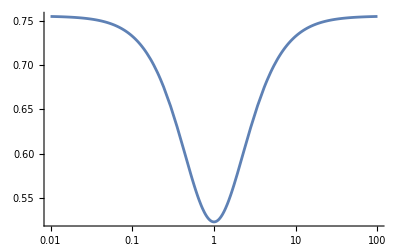

```mathematica
LogLinearPlot[CVherdALT,{α,1/100,100}]
```

The CV is √(4/π-1) (=0.523) when the Gaussian is symmetrical (α=1) and rises as the herd elongates to a maximum of √(π/2-1)(=0.756)

```mathematica
Limit[Sqrt[(π (1+α^2))/(2 α^2 EllipticE[1-1/α^2]^2)-1],α->1]
%//N
```

√(-1+4/π)

0.522723

```mathematica
Limit[Sqrt[(π (1+α^2))/(2 α^2 EllipticE[1-1/α^2]^2)-1],α->0]
%//N
```

√(1/2 (-2+π))

0.755511

#### Herd split patches: Two Gaussian patches at a distance c from one another [σx = σy]

Here we split the range in two and move one patch to the right by an amount c.  For the intra-individual distances, half will be in the same patch (given above) and half will be in the other patch, which we now calculate. For clarity, we assume that individual 2 is from the right-most patch, displaced by c on the x axis.

```mathematica
Simplify[Sqrt[Δx^2+Δy^2]PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{x1,y1}]PDF[MultinormalDistribution[{c,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{Δx+x1,Δy+y1}]]/.ρ->0
```

(ⅇ^(-(2 y1^2 σx^2+2 y1 Δy σx^2+Δy^2 σx^2+(c^2+2 x1^2+2 x1 Δx+Δx^2-2 c (x1+Δx)) σy^2)/(2 σx^2 σy^2)) √(Δx^2+Δy^2))/(4 π^2 σx^2 σy^2)

```mathematica
Simplify[Integrate[%,{x1,-Infinity,Infinity}],constraints]
```

(ⅇ^(1/4 (-(c-Δx)^2/σx^2-(2 (2 y1^2+2 y1 Δy+Δy^2))/σy^2)) √(Δx^2+Δy^2))/(4 π^(3/2) σx σy^2)

```mathematica
Simplify[Integrate[%,{y1,-Infinity,Infinity}],constraints]
```

(ⅇ^(-(c-Δx)^2/(4 σx^2)-Δy^2/(4 σy^2)) √(Δx^2+Δy^2))/(4 π σx σy)

```mathematica
integrateme=Simplify[Integrate[%,{Δy,-Infinity,Infinity}],constraints]
```

(ⅇ^(-(c-Δx)^2/(4 σx^2)) σy HypergeometricU[-1/2,0,Δx^2/(4 σy^2)])/(√π σx)

This does not integrate directly:

```mathematica
Integrate[integrateme,Δx]
```

(σy ∫ⅇ^(-(c-Δx)^2/(4 σx^2)) HypergeometricU[-1/2,0,Δx^2/(4 σy^2)]ⅆΔx)/(√π σx)

```mathematica
Integrate[integrateme,{Δx,-Infinity,Infinity}]
```

∫_(-∞)^∞ (ⅇ^(-(c-Δx)^2/(4 σx^2)) σy HypergeometricU[-1/2,0,Δx^2/(4 σy^2)])/(√π σx)ⅆΔx

However, in the symmetric case (σx=σy=σy), it does:

```mathematica
FullSimplify[Integrate[integrateme/.σy->σ/.σx->σ,{Δx,-Infinity,Infinity},Assumptions->constraints],constraints]
```

(ⅇ^(-c^2/(8 σ^2)) √π ((c^2+4 σ^2) BesselI[0,c^2/(8 σ^2)]+c^2 BesselI[1,c^2/(8 σ^2)]))/(4 σ)

The distance c only enters in terms of c/σ (the scaled distance between the two populations), so we switch to working in terms of this scaled distance c_S (the “c” presented in the paper):

```mathematica
partsolnC=FullSimplify[%/.c->Subscript[c, S] σ,constraints]
```

1/4 ⅇ^(-c_S^2/8) √π σ (BesselI[1,c_S^2/8] c_S^2+BesselI[0,c_S^2/8] (4+c_S^2))

The expected value of the distance squared is much simpler to calculate:

```mathematica
Simplify[(Δx^2+Δy^2)PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{x1,y1}]PDF[MultinormalDistribution[{c,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{Δx+x1,Δy+y1}]]/.ρ->0
```

(ⅇ^(-(2 y1^2 σx^2+2 y1 Δy σx^2+Δy^2 σx^2+(c^2+2 x1^2+2 x1 Δx+Δx^2-2 c (x1+Δx)) σy^2)/(2 σx^2 σy^2)) (Δx^2+Δy^2))/(4 π^2 σx^2 σy^2)

```mathematica
Simplify[Integrate[%,{x1,-Infinity,Infinity}],constraints]
```

(ⅇ^(1/4 (-(c-Δx)^2/σx^2-(2 (2 y1^2+2 y1 Δy+Δy^2))/σy^2)) (Δx^2+Δy^2))/(4 π^(3/2) σx σy^2)

```mathematica
Simplify[Integrate[%,{y1,-Infinity,Infinity}],constraints]
```

(ⅇ^(-(c-Δx)^2/(4 σx^2)-Δy^2/(4 σy^2)) (Δx^2+Δy^2))/(4 π σx σy)

```mathematica
Simplify[Integrate[%,{Δy,-Infinity,Infinity}],constraints]
```

(ⅇ^(-(c-Δx)^2/(4 σx^2)) (Δx^2+2 σy^2))/(2 √π σx)

```mathematica
Simplify[Integrate[%,{Δx,-Infinity,Infinity}],constraints]
```

c^2+2 (σx^2+σy^2)

In the symmetric case measuring c in terms of standard deviations:

```mathematica
partsolnsqC=Factor[%/.c->Subscript[c, S] σ/.σx->σ/.σy->σ]
```

σ^2 (4+c_S^2)

Recall that we need to assume σx=σy=σ and average over individuals chosen from the same patch or from different patches. Here we allow a fraction 1-f to be chosen from within a patch (either one) and f between the patches:

```mathematica
solnC=(1-f) soln+f partsolnC/.σx->σ/.σy->σ
solnsqC=(1-f) solnsq+f partsolnsqC/.σx->σ/.σy->σ
```

(1-f) √π σ+1/4 ⅇ^(-c_S^2/8) f √π σ (BesselI[1,c_S^2/8] c_S^2+BesselI[0,c_S^2/8] (4+c_S^2))

4 (1-f) σ^2+f σ^2 (4+c_S^2)

Relative to the unsplit case:

```mathematica
FullSimplify[solnsqC/solnsq^2/.σx->σ/.σy->σ,constraints]
```

(4+f c_S^2)/(16 σ^2)

Calculating the distance squared over the mean squared for the CV:

```mathematica
Simplify[solnsqC/solnC^2/.σx->σ/.σy->σ]
```

(16 ⅇ^(c_S^2/4) (4+f c_S^2))/(π (-4 ⅇ^(c_S^2/8) (-1+f)+4 f BesselI[0,c_S^2/8]+f (BesselI[0,c_S^2/8]+BesselI[1,c_S^2/8]) c_S^2)^2)

Note that the above depends only on c/σ and not on c itself (as expected).  That is, the amount of split relative to the standard deviation of each patch is what matters.

```mathematica
CVherdC=Sqrt[(16 ⅇ^(Subscript[c, S]^2/4) (4+f Subscript[c, S]^2))/(π (4 ⅇ^(Subscript[c, S]^2/8) (1-f)+(4+Subscript[c, S]^2)f BesselI[0,Subscript[c, S]^2/8]+f Subscript[c, S]^2 BesselI[1,Subscript[c, S]^2/8])^2)-1];
```

Note that the CVherd goes to √(1/f-1) in the limit as c becomes very large relative to σ, because a fraction f of the time pairs are at distance c and 1-f the time near 0 so CVherdC approaches Sqrt[((1-f)0+f c_S^2)/((1-f)0+f c_S)^2-1]=1

```mathematica
Sqrt[((1-f)0+f Subscript[c, S]^2)/((1-f)0+f Subscript[c, S])^2-1]
```

√(-1+1/f)

```mathematica
Limit[CVherdC,Subscript[c, S]->Infinity, Assumptions->{0<f<1,Subscript[c, S]>0,σ>0}]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

√(-1+1/f)

and goes to √(4/π-1) as c_S->0, as in the case of a single population:

```mathematica
Limit[Simplify[CVherdC],Subscript[c, S]->0]
```

√(-1+64/((-4 (-1+f)+4 f)^2 π))

#### Individual CV: Average pairwise distance from individual i [σx = σy]

We now focus on an individual at position {x1,y1} and determine its average pairwise distance to all other individuals measured (not yet using the PDF for {x1,y1}).  This would then be used as the basis for calculating the CV among individuals. 

Unfortunately, there appears to be no closed form solution, although the Rice Distribution describes the average distance from a point to a Gaussian PDF, but only for σx = σy:

```mathematica
Mean[RiceDistribution[Sqrt[x1^2+y2^2],σ]]
```

√(π/2) σ LaguerreL[1/2,-(x1^2+y2^2)/(2 σ^2)]

```mathematica
tryx1=0.3;tryy1=0.7;tryσ=2;
Simplify[Sqrt[(x2-tryx1)^2+(y2-tryy1)^2]PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{x2,y2}]]/.ρ->0/.σx->tryσ/.σy->tryσ;
NIntegrate[%,{x2,-Infinity,Infinity},{y2,-Infinity,Infinity}]
```

2.59668

```mathematica
Mean[RiceDistribution[Sqrt[tryx1^2+tryy1^2],tryσ]]//N
```

2.59668

Unfortunately, the Laguerre function in the mean is not readily integrable:

```mathematica
Simplify[Mean[RiceDistribution[Sqrt[x1^2+y1^2],σ]]PDF[MultinormalDistribution[{0,0},{{σx^2,ρ σx σy},{ρ σx σy,σy^2}}],{x1,y1}]/.ρ->0/.σx->σ/.σy->σ,constraints]
```

(ⅇ^(-(x1^2+y1^2)/(2 σ^2)) LaguerreL[1/2,-(x1^2+y1^2)/(2 σ^2)])/(2 √(2 π) σ)

```mathematica
Simplify[Integrate[%,x1],constraints]
```

(∫ⅇ^(-(x1^2+y1^2)/(2 σ^2)) LaguerreL[1/2,-(x1^2+y1^2)/(2 σ^2)]ⅆx1)/(2 √(2 π) σ)

Note that we can simplify this, using r to denote the radius between {x1,y1} and the centre of the Gaussian, the probability of being at that point r is then given by the normal distribution multiplied by 2*r (the circumference around the bivariate Gaussian at distance r from the mean) and divided by the area:

```mathematica
Simplify[Integrate[(2 r PDF[ NormalDistribution[0,σ],r]),{r,0,Infinity}],constraints]
```

√(2/π) σ

```mathematica
Mean[RiceDistribution[r,σ]]((2 r PDF[ NormalDistribution[0,σ],r])/(√(2/π) σ))
```

(ⅇ^(-r^2/(2 σ^2)) √(π/2) r LaguerreL[1/2,-r^2/(2 σ^2)])/σ

```mathematica
Simplify[Integrate[%,r],constraints]
```

(√(π/2) ∫ⅇ^(-r^2/(2 σ^2)) r LaguerreL[1/2,-r^2/(2 σ^2)]ⅆr)/σ

Rescaling r to σ (rS=r/σ) and noting that ⅆr becomes σⅆrS:
	
	σ ⅇ^(-rS^2/2) √(π/2) rS LaguerreL[1/2,-rS^2/2]

While the above cannot be integrated analytically, we only need a numerical solution (factoring the σ out):

```mathematica
indsoln=σ NIntegrate[ⅇ^(-rS^2/2) √(π/2) rS LaguerreL[1/2,-rS^2/2],{rS,0,Infinity}]
```

1.77245 σ

As expected, when integrated over r, we get the mean distance found above:

```mathematica
soln/.σx->σ/.σy->σ
%//N
```

√π σ

1.77245 σ

What we really want though is E[X^2]:

```mathematica
Mean[RiceDistribution[r,σ]]
```

√(π/2) σ LaguerreL[1/2,-r^2/(2 σ^2)]

```mathematica
Mean[RiceDistribution[r,σ]]^2((2 r PDF[ NormalDistribution[0,σ],r])/(√(2/π) σ))
```

1/2 ⅇ^(-r^2/(2 σ^2)) π r LaguerreL[1/2,-r^2/(2 σ^2)]^2

```mathematica
Simplify[Integrate[%,r],constraints]
```

1/2 π ∫ⅇ^(-r^2/(2 σ^2)) r LaguerreL[1/2,-r^2/(2 σ^2)]^2ⅆr

Rescaling r to σ (rS=r/σ) and noting that ⅆr becomes σⅆrS:

```mathematica
1/2 ⅇ^(-rS^2/2) π rS σ^2 LaguerreL[1/2,-rS^2/2]^2;
```

```mathematica
Integrate[ %,rS]
```

1/2 π σ^2 ∫ⅇ^(-rS^2/2) rS LaguerreL[1/2,-rS^2/2]^2ⅆrS

While the above cannot be integrated analytically, we only need a numerical solution:

```mathematica
indsolnsq=(σ^2 π)/2 NIntegrate[ ⅇ^(-rS^2/2)  rS  LaguerreL[1/2,-rS^2/2]^2,{rS,0,Infinity}]
```

3.34122 σ^2

It could also be approximated (not used):

```mathematica
Series[LaguerreL[1/2,-rS^2/2]^2 ,{rS,0,5}]
```

1+rS^2/2+rS^4/32+O[rS]^6

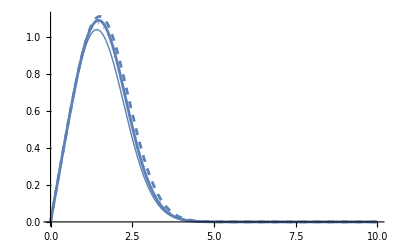

```mathematica
Show[
Plot[ⅇ^(-rS^2/2) rS LaguerreL[1/2,-rS^2/2]^2,{rS,0,10}],
Plot[ⅇ^(-rS^2/2) rS  (1+rS^2/2),{rS,0,10},PlotStyle->Thin],
Plot[ⅇ^(-rS^2/2) rS  (1+rS^2/2+rS^4/64),{rS,0,10},PlotStyle->Dotted],
Plot[ⅇ^(-rS^2/2) rS  (1+rS^2/2+rS^4/32),{rS,0,10},PlotStyle->Dashed],PlotRange->All
]
```

Half-way between the quadratic and quartic approximation works best when weighted by ⅇ^(-rS^2/2) rS

```mathematica
{NIntegrate[ⅇ^(-rS^2/2) rS LaguerreL[1/2,-rS^2/2]^2,{rS,0,Infinity}],
NIntegrate[ⅇ^(-rS^2/2) rS  (1+rS^2/2),{rS,0,Infinity}],NIntegrate[ⅇ^(-rS^2/2) rS  (1+rS^2/2+rS^4/64),{rS,0,Infinity}],
NIntegrate[ⅇ^(-rS^2/2) rS  (1+rS^2/2+rS^4/32),{rS,0,Infinity}]}
```

{2.12709,2.,2.125,2.25}

For the σx = σy = σ case, individual CV can be written as Sqrt[indsolnsq/soln^2-1], which again does not depend on the scale (σ):

```mathematica
CVind=Simplify[Sqrt[indsolnsq/soln^2-1]/.σx->σ/.σy->σ]
```

0.25208

1D Analysis - For comparison, a very elongated distribution would be equivalent to the 1D case:

```mathematica
Sqrt[(x2-x1)^2]PDF[NormalDistribution[0,σx],x2]
```

(ⅇ^(-x2^2/(2 σx^2)) √((-x1+x2)^2))/(√(2 π) σx)

We take the focal individual to be at position x1 and calculate its distance to other individuals [it’s easier to just take the distance as the positive value, breaking the integral into x2>x1 and x2<x1 (switching the sign in the latter case)]

```mathematica
Integrate[(x2-x1)PDF[NormalDistribution[0,σx],x2],x2,Assumptions->{x1>0,σx>0}]
```

(-ⅇ^(-x2^2/(2 σx^2)) σx^2-√(π/2) x1 σx Erf[x2/(√2 σx)])/(√(2 π) σx)

```mathematica
Simplify[Simplify[Limit[%,x2->Infinity,Assumptions->{x1>0,σx>0}]-Limit[%,x2->x1,Assumptions->{x1>0,σx>0}],{x1>0,σx>0}]+
Simplify[Limit[-%,x2->x1,Assumptions->{x1>0,σx>0}]-Limit[-%,x2->-Infinity,Assumptions->{x1>0,σx>0}],{x1>0,σx>0}],constraints]
```

ⅇ^(-x1^2/(2 σx^2)) √(2/π) σx+x1 Erf[x1/(√2 σx)]

The above gives the average distance of individuals at position x1 to all others.  We then calculate the average distance and then the average distance squared among focal individuals:

```mathematica
Integrate[(ⅇ^(-x1^2/(2 σx^2)) √(2/π) σx+x1 Erf[x1/(√2 σx)])PDF[NormalDistribution[0,σx],x1],x1,Assumptions->constraints]
```

(σx Erf[x1/σx])/(√π)-(ⅇ^(-x1^2/(2 σx^2)) σx Erf[x1/(√2 σx)])/(√(2 π))

```mathematica
indsoln1=Simplify[Simplify[Limit[%,x1->Infinity,Assumptions->{x1>0,σx>0}]-Limit[%,x1->-Infinity,Assumptions->{x1>0,σx>0}],{x1>0,σx>0}],constraints]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(2 σx)/(√π)

Repeating for the average distance squared turns out to be easier with the limits of integration:

```mathematica
indsolnsq1=Integrate[(ⅇ^(-x1^2/(2 σx^2)) √(2/π) σx+x1 Erf[x1/(√2 σx)])^2 PDF[NormalDistribution[0,σx],x1],{x1,-Infinity,Infinity},Assumptions->constraints]
```

((6 √3+π) σx^2)/(3 π)

```mathematica
CVind1=Simplify[Sqrt[(((6 √3+π) σx^2)/(3 π))/((2 σx)/(√π))^2-1]]
```

√(-1+1/12 (6 √3+π))

```mathematica
%//N
```

0.357526

Given the challenges of integrating the individual-level average distance, attempts to analyse the case of a split herd did not bear fruit. That said, the extreme cases are known. When the two herds overlap completely (c=0), we already have the non-split result above (CVind). At the other extreme, where the two patches are very far apart (c -> ∞), the individual mean μ_IID approaches p_2 c for individuals drawn from patch 1 (with ~0 distance to other individuals within the patch and a distance c when drawn from the other patch) and similarly p_1 c for individuals drawn from patch 2; altogether, this gives an average distance of E[μ_IID]=2 p_1 p_2 c=f c and an E[μ_IID^2]=p_1(p_2 c)^2+p_2(p_1 c)^2=f/2 c^2, an individual-level variance of Var[μ_IID]=f/2 c^2-(f c)^2=f (1/2-f) c^2, and so a CV of  Sqrt[(f (1/2-f) c^2)/(f c)^2]=√((1/2-f)/f). When the two patches are equal in size (f=1/2), all individuals have the same average distance to all others (~c/2) and there is no variance (CVind=0), but when the two patches are unequal in size, CVind can rise because individuals in the smaller patch have a much higher average IID to all other individuals, since most other individuals are in the larger patch.

```mathematica
CVindfarsplit=√((1/2-f)/f);
```

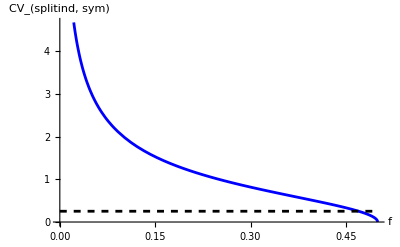

```mathematica
Show[
Plot[√((1/2-f)/f),{f,0,1/2},PlotStyle->Blue],
Plot[CVind,{f,0,1/2},PlotStyle->{Dashed,Black}],
AxesLabel->{"f","CV_(splitind, sym)"}
]
```

By comparison, a plot of CV_herd in the limit of very distant patches (solid) as a function of f (the chance individuals are drawn from different patches):

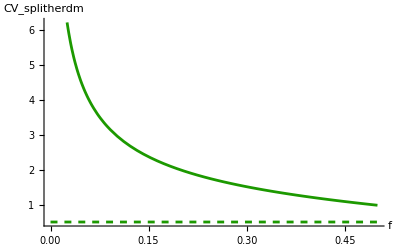

```mathematica
Show[
Plot[√(1/f-1)(*Asymmetrical split case*),{f,0,1/2},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[√(4/π-1) (*Unsplit case*),{f,0,1/2},PlotStyle->{Dashed,RGBColor[0.11,0.6,0.]}],
AxesLabel->{"f","CV_splitherdm"},PlotRange->All,AxesOrigin->{0,0}
]
```

Plot of CV_herd/CV_ind in the limit of very distant patches (solid) as a function of f (the chance individuals are drawn from different patches):

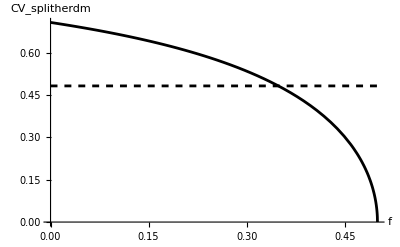

```mathematica
Show[
Plot[(√((1/2-f)/f))/(√(1/f-1))(*Asymmetrical split case*),{f,0,1/2},PlotStyle->Black],
Plot[CVind/(√(4/π-1)) (*Unsplit case*),{f,0,1/2},PlotStyle->{Dashed,Black}],
AxesLabel->{"f","CV_ratio"},PlotRange->All,AxesOrigin->{0,0}
]
```

Thus, CV_ratio falls for distant patches only when f is small enough (roughly f=0.35, with a 35% chance of drawing individuals from different patches).

### Simulation check

1000 individuals were simulated from the given population distribution. CV_herd and CV_ind match the predictions to the first two digits of precision.

#### Herd with a Gaussian range (CV_herd~0.525, CV_ind~0.255)

```mathematica
SeedRandom[28645];
```

Assume a random distribution of individuals (blue):

```mathematica
tryσx=1;
tryσy=1;
```

```mathematica
table=Table[{Random[NormalDistribution[0,tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,1000}];
```

Calculating the mean Euclidean distance for all pairwise distances (blue)

This table includes all of the pairwise distances:

```mathematica
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,1000},{j,i+1,1000}]];
```

The mean and SD:

```mathematica
{ Mean[disttable],StandardDeviation[disttable]}
```

{1.74168,0.914825}

The coefficient of variation across the herd (CV_herd):

```mathematica
StandardDeviation[disttable]/Mean[disttable]
```

0.525253

This matches the expectation:

```mathematica
Simplify[CVherd/.σx->tryσx/.σy->tryσy,constraints]//N
```

0.522723

Looking instead at how far, on average, each individual is to all others, then calculating the CV in this value among individuals (CV_ind):

```mathematica
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,1000}]),{i,1,1000}];
```

The mean and SD:

```mathematica
{Mean[disttable2],StandardDeviation[disttable2]}
```

{1.74168,0.443523}

Because of the averaging that occurs for each individual’s average pairwise distance, we get a lower CV_ind:

```mathematica
StandardDeviation[disttable2]/Mean[disttable2]
```

0.254652

This matches the expectation:

```mathematica
Simplify[CVind,constraints]//N
```

0.25208

#### Moderately elongated range (σy=σx/2; CV_herd~0.587, CV_ind~0.285)

```mathematica
SeedRandom[29543];
```

Assume a random distribution of individuals (blue):

```mathematica
tryσx=1;
tryσy=1/2;
```

```mathematica
table=Table[{Random[NormalDistribution[0,tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,1000}];
```

Calculating the mean Euclidean distance for all pairwise distances (blue)

This table includes all of the pairwise distances:

```mathematica
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,1000},{j,i+1,1000}]];
```

The mean and SD:

```mathematica
{ Mean[disttable],StandardDeviation[disttable]}
```

{1.40677,0.825723}

The coefficient of variation across the herd (CV_herd):

```mathematica
StandardDeviation[disttable]/Mean[disttable]
```

0.586963

This matches the expectation:

```mathematica
Simplify[CVherd/.σx->tryσx/. σy->tryσy,constraints]//N
```

0.582027

Looking instead at how far, on average, each individual is to all others, then calculating the CV in this value among individuals (CV_ind):

```mathematica
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,1000}]),{i,1,1000}];
```

The mean and SD:

```mathematica
{Mean[disttable2],StandardDeviation[disttable2]}
```

{1.40677,0.401356}

Because of the averaging that occurs for each individual’s average pairwise distance, we get a lower CV_ind:

```mathematica
StandardDeviation[disttable2]/Mean[disttable2]
```

0.285303

#### Very elongated range (σy=σx/100; CV_herd~0.752, CV_ind~0.354)

```mathematica
SeedRandom[87772];
```

Assume a random distribution of individuals (blue):

```mathematica
tryσx=1;
tryσy=1/100;
```

```mathematica
table=Table[{Random[NormalDistribution[0,tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,1000}];
```

Calculating the mean Euclidean distance for all pairwise distances (blue)

This table includes all of the pairwise distances:

```mathematica
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,1000},{j,i+1,1000}]];
```

The mean and SD:

```mathematica
{ Mean[disttable],StandardDeviation[disttable]}
```

{1.14843,0.863437}

The coefficient of variation across the herd (CV_herd):

```mathematica
StandardDeviation[disttable]/Mean[disttable]
```

0.751843

This matches the expectation:

```mathematica
Simplify[CVherd/.σx->tryσx/. σy->tryσy,constraints]//N
```

0.755044

Looking instead at how far, on average, each individual is to all others, then calculating the CV in this value among individuals (CV_ind):

```mathematica
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,1000}]),{i,1,1000}];
```

The mean and SD:

```mathematica
{Mean[disttable2],StandardDeviation[disttable2]}
```

{1.14843,0.406857}

Because of the averaging that occurs for each individual’s average pairwise distance, we get a lower CV_ind:

```mathematica
StandardDeviation[disttable2]/Mean[disttable2]
```

0.354273

This matches the expectation:

```mathematica
Simplify[CVind1,constraints]//N
```

0.357526

### Figure 1 - numerical integration

Blue: Individual level CV (dots based on simulations, lines based on symmetrical case).
Green: Herd level CV (dots based on simulation, lines based on symmetrical case).
Black:  CV_ind/CV_herd (dots based on simulations for CV_ind, lines based on symmetrical case).

#### Integrations - Previously evaluated [ENTER]

```mathematica
intplottingherdB={{0,0.5227232008770635},{1/10,0.5293407474740066},{1/5,0.5503767552787215},{3/10,0.5848351377204023},{2/5,0.62782586044906},{1/2,0.6719299336710343},{3/5,0.7097154906842982},{7/10,0.7362030893671205},{4/5,0.750347311420061},{9/10,0.7550437399359384}}
```

```mathematica
intplottingindB={{0,0.2520803544905147},{1/10,0.25518000579634537},{1/5,0.26500879705698094},{3/10,0.28104222825868547},{2/5,0.30089248432425053},{1/2,0.32100396904321005},{3/5,0.3379153430671249},{7/10,0.34947066393942994},{4/5,0.35543883559280276},{9/10,0.3573447344676925}};
```

```mathematica
intplottingherdC={{0,0.5227232009873112},{1/10,0.5227239329075928},{1/5,0.5228035469998735},{3/10,0.524138853351632},{2/5,0.5331526008906213},{1/2,0.564706069452737},{3/5,0.6287045924514781},{7/10,0.7160813351874343},{4/5,0.8123470005583199},{17/20,0.8607613089836089},{9/10,0.9084236045853212},{19/20,0.9549220148114106}};
```

```mathematica
intplottingindC={{0,0.2520801165942636},{1/10,0.25200522607365977},{1/5,0.25045324939015384},{3/10,0.24214702204367256},{2/5,0.2196389599705442},{1/2,0.1824561380264057},{3/5,0.13975272658817786},{7/10,0.09890672312111803},{4/5,0.06196960807245782},{17/20,0.04504547458329638},{9/10,0.02911028854877327},{19/20,0.014115108294420907}};
```

```mathematica
intplottingherdD={{0,0.5227232009167528},{1/10,0.522765342177266},{1/5,0.5237411178502892},{3/10,0.5303806786463606},{2/5,0.5568407057211127},{1/2,0.6290112526942427},{3/5,0.7709046690326646},{7/10,0.9898655921091033},{4/5,1.285715663381551},{17/20,1.4635528845278027},{9/10,1.6629036118663814},{19/20,1.885663601432402}};
```

```mathematica
intplottingindD={{0,0.25208011647204787},{1/10,0.2521252663731851},{1/5,0.2531597393007574},{3/10,0.2599886855698586},{2/5,0.28536759406129264},{1/2,0.3469263473303876},{3/5,0.4535365545965457},{7/10,0.6039566130027363},{4/5,0.797324070459304},{17/20,0.9111044114964313},{9/10,1.0374447025752387},{19/20,1.1776331930939605}};
```

```mathematica
intplottingherdE={{0,0.6930602128358243},{1/10,0.6948904347790711},{1/5,0.6985044096686023},{3/10,0.6966414046157752},{2/5,0.6902150082664524},{1/2,0.7009810157250438},{3/5,0.7433856557817154},{7/10,0.8052669243278289},{4/5,0.8725072815481681},{17/20,0.9058183616725517},{9/10,0.9383112518124032},{19/20,0.9697485747084602}};
```

```mathematica
intplottingindE={{0,0.3305091378599227},{1/10,0.3311328217296327},{1/5,0.32901781580559153},{3/10,0.31061300951506027},{2/5,0.2657695141011268},{1/2,0.20557280709498166},{3/5,0.14918433456574715},{7/10,0.10202850796401869}};
```

```mathematica
intplottingherdF={{0,0.6930602123134018},{1/10,0.693862097938722},{1/5,0.6980850105248394},{3/10,0.713045444952277},{2/5,0.7563161059997862},{1/2,0.8528248405288947},{3/5,1.0150758204965915},{7/10,1.2343819546078152},{4/5,1.4983253202659426},{17/20,1.6445273457921878},{9/10,1.7994518487401867},{19/20,1.9627864846282088}};
```

```mathematica
intplottingindF={{0,0.33050913703905305},{1/10,0.3309342481823283},{1/5,0.33427240136835296},{3/10,0.3494190470482914},{2/5,0.3937162387004852},{1/2,0.48014277552932955},{3/5,0.604581513129078},{7/10,0.7567573245973087}};
```

```mathematica
intplottingherdG={{0,0.693060212015846},{1/10,0.6909930062529258},{1/5,0.6829132007857964},{3/10,0.6652837114870311},{2/5,0.6345135606116789},{1/2,0.5900257015584462},{3/5,0.5404849669297872},{7/10,0.5148716694424429},{4/5,0.5679102580542682},{17/20,0.6379907350895276},{9/10,0.7366346897317203},{19/20,0.8591757553792789}};
```

```mathematica
intplottingindG={{0,0.3305070397971567},{1/10,0.32958054824689326},{1/5,0.32592369336767346},{3/10,0.31772906558774194},{2/5,0.30257026103488976},{1/2,0.27779181354490734},{3/5,0.24108205847797515},{7/10,0.19102717033238367}};
```

```mathematica
intplottingherdH={{0,0.6930602120182102},{1/10,0.6923158078070205},{1/5,0.689402355177155},{3/10,0.6830261797738891},{2/5,0.671856507590081},{1/2,0.6557918659982612},{3/5,0.6393680779919669},{7/10,0.6423135312150211},{4/5,0.7315501716253063},{17/20,0.8569435601543314},{9/10,1.0823639522911108},{19/20,1.4682982329072491}};
```

```mathematica
intplottingindH={{0,0.33050703980087154},{1/10,0.3301743864655322},{1/5,0.3288795654495974},{3/10,0.3260900099882},{2/5,0.3214051608033421},{1/2,0.31549620210759655},{3/5,0.3128443626830841},{7/10,0.3297041622472292}};
```

#### Panel A: Symmetric range contraction [σ along x axis, decreasing from left to right]

```mathematica
SeedRandom[12241];
```

We seek to examine a range of σx=σy=σ from 0 to 1. [We expect no effect.] In our plots, we’ll show σ decreasing along the x-axis varying x from 0 to 1. To do so, we define σ = (1-x)^V, which allows us to vary σ from 1 at x=0 to 0 at x=1. V allows us to change the midpoint, which we set to 2, so that a value of x=1/2 corresponds to σ=1/4. To convert the x-axis to σ, we use 1-σ^(1/V):

```mathematica
tryV=2;
```

```mathematica
Solve[σ==(1-x)^V,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1-σ^(1/V)}}

```mathematica
tab=Join[Table[i,{i,0,9/10,1/10}],{{19/20}}]//Flatten
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,19/20}

```mathematica
numind=100;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Table[{Random[NormalDistribution[0,(1-tab[[t]])^tryV]],Random[NormalDistribution[0,(1-tab[[t]])^tryV]]},{i,1,numind}];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsim[tab[[t]],tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsim[tab[[t]],tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdA=Table[{tab[[t]],CVherdsim[tab[[t]],tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.512284},{1/10,0.503982},{1/5,0.513253},{3/10,0.49795},{2/5,0.525723},{1/2,0.513991},{3/5,0.525625},{7/10,0.504365},{4/5,0.53337},{9/10,0.509055},{19/20,0.504871}}

```mathematica
forplottingindA=Table[{tab[[t]],CVindsim[tab[[t]],tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.247301},{1/10,0.226619},{1/5,0.241133},{3/10,0.225003},{2/5,0.260052},{1/2,0.246679},{3/5,0.261796},{7/10,0.234893},{4/5,0.275199},{9/10,0.236232},{19/20,0.236838}}

To label the x axis with σ values:

```mathematica
{x,(1-x)^tryV}/.x->tab//MatrixForm
```

(0 | 1/10 | 1/5 | 3/10 | 2/5 | 1/2 | 3/5 | 7/10 | 4/5 | 9/10 | 19/20
1 | 81/100 | 16/25 | 49/100 | 9/25 | 1/4 | 4/25 | 9/100 | 1/25 | 1/100 | 1/400)

```mathematica
Select[x/.Solve[(1-x)^tryV==1/10,x],#<1&]
```

{1/10 (10-√10)}

```mathematica
xticks={{0.01,"1"},{1/2 (2-√2),"1/2"},{1/2,"1/4"},{1/10 (10-√10),"1/10"},{4/5,"1/25"},{9/10,"1/100"},{1,"1/∞"}}
```

{{0.01,1},{1/2 (2-√2),1/2},{1/2,1/4},{1/10 (10-√10),1/10},{4/5,1/25},{9/10,1/100},{1,1/∞}}

```mathematica
maxc=1;
```

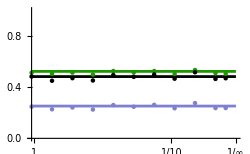

```mathematica
plotA=Show[
Plot[CVherd/.σx->σy/.σy->(1-x)^tryV,{x,0,1},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[CVind,{x,0,1},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[(CVind/CVherd/.σx->σy/.σy->(1-x)^tryV),{x,0,1},PlotStyle->Black],
ListPlot[forplottingherdA,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[forplottingindA,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Table[{forplottingindA[[i,1]],forplottingindA[[i,2]]/forplottingherdA[[i,2]]},{i,1,Length[forplottingindA]}],PlotStyle->{Black}],
AxesOrigin->{0,0},
PlotRange->{{0,1},{0,1}},
Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel B: Asymmetric contraction leading to elongated ranges [σx/σy along x axis]

```mathematica
SeedRandom[21773];
```

We seek to examine a range of σy from 0 to 1, holding σx=1. In our plots, we’ll show σx/σy along the x-axis using values of x from 0 to 1. To do so, we define σy = (1-x)^V, which allows us to vary σx/σy from 1 at x=0 to infinity at x=1. V allows us to change the midpoint, which we set to 2, so that a value of x=1/2 corresponds to σx/σy=4. To convert the x-axis to σy, we use 1-σy^(1/V):

```mathematica
tryV=2;
```

```mathematica
Solve[σy==(1-x)^V,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1-σy^(1/V)}}

```mathematica
tab=Table[i,{i,0,9/10,1/10}]//Flatten
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10}

```mathematica
tryσx=1;
tryf=0; (*No split*)
```

```mathematica
numind=100;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Table[{Random[NormalDistribution[0,tryσx]],Random[NormalDistribution[0,(1-tab[[t]])^tryV]]},{i,1,numind}];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsim[tryσx,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsim[tryσx,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdB=Table[{tab[[t]],CVherdsim[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.491624},{1/10,0.509512},{1/5,0.567223},{3/10,0.616676},{2/5,0.60762},{1/2,0.644016},{3/5,0.716753},{7/10,0.724227},{4/5,0.710472},{9/10,0.73793}}

```mathematica
forplottingindB=Table[{tab[[t]],CVindsim[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.215466},{1/10,0.240091},{1/5,0.282201},{3/10,0.332271},{2/5,0.288243},{1/2,0.28341},{3/5,0.374266},{7/10,0.328504},{4/5,0.283964},{9/10,0.347029}}

Below, we’ll want the ratio of CVind/CVherd in the limit for a very elongated range:

```mathematica
limratio=Limit[CVind1/CVherd/.σx->tryσx,σy->Infinity]
```

√((6 (-2+√3)+π)/(6 (-2+π)))

To label the x axis:

```mathematica
{x,tryσx/(1-x)^tryV}/.x->tab//MatrixForm
```

(0 | 1/10 | 1/5 | 3/10 | 2/5 | 1/2 | 3/5 | 7/10 | 4/5 | 9/10
1 | 100/81 | 25/16 | 100/49 | 25/9 | 4 | 25/4 | 100/9 | 25 | 100)

```mathematica
Select[x/.Solve[1/(1-x)^tryV==10,x],#<1&]
```

{1/10 (10-√10)}

```mathematica
xticks={{0.01,"1"},{1/2 (2-√2),"2"},{1/2,"4"},{1/10 (10-√10),"10"},{4/5,"25"},{9/10,"100"},{1,"∞"}}
```

{{0.01,1},{1/2 (2-√2),2},{1/2,4},{1/10 (10-√10),10},{4/5,25},{9/10,100},{1,∞}}

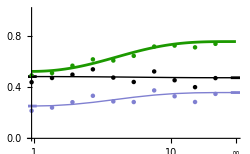

```mathematica
plotB=Show[
Plot[CVherd/.σx->tryσx/.σy->(1-x)^tryV,{x,0,1},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[CVind,{x,-0.025,0.025},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVind1,{x,0.975,1.025},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[(CVind/CVherd/.σx->tryσx/.σy->tryσx),{x,-0.025,0.025},PlotStyle->Black],
Plot[limratio,{x,0.975,1.025},PlotStyle->Black],
ListPlot[forplottingherdB,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[forplottingindB,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[intplottingindB,{{1,CVind1}}],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingindB[[i,1]],forplottingindB[[i,2]]/forplottingherdB[[i,2]]},{i,1,Length[forplottingindB]}],PlotStyle->{Black}],
ListPlot[Join[Table[{intplottingindB[[i,1]],intplottingindB[[i,2]]/(CVherd/.σx->tryσx/.σy->(1-tab[[i]])^tryV)},{i,1,Length[intplottingindB]}],{{1,limratio}}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,1},{0,1}},
Ticks->{xticks,Automatic},ImageSize->250
]
```

Dividing CVind by CVherd gives very similar answers in the 1D and symmetrical 2D cases (at opposite ends of this “elongation” axis). While the dashed line looks flat, the values are not exactly the same.

```mathematica
{CVind/(CVherd/.σx->1/.σy->1),CVind1/CVherd1}//N
```

{0.482244,0.473224}

#### Panel B: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate:

```mathematica
tryLIM=Infinity;
tryc=0;
tryf=0;
tryσx=1;

For[t=1,t≤Length[tab],t++,
tryσy=(1-tab[[t]])^tryV;
mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
sqH=(1-f) solnsq+f (c^2+2 (σx^2+σy^2))/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
CVherdintC[tryσx,tab[[t]]]=Sqrt[sqH-mean^2]/mean;
Print[{CVherdintC[tryσx,tab[[t]]]}]
]
```

{0.522723}

{0.529341}

{0.550377}

{0.584835}

{0.627826}

{0.67193}

{0.709715}

{0.736203}

{0.750347}

{0.755044}

```mathematica
For[t=1,t≤Length[tab],t++,
tryσy=(1-tab[[t]])^tryV;
mean=N[(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc];

CVindintC[tryσx,tab[[t]]]=Sqrt[sqI[tryσx,tryσy]-mean^2]/mean;Print[{CVindintC[tryσx,tab[[t]]]}]
]
```

{0.25208}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.25518}

{0.265009}

{0.281042}

{0.300892}

{0.321004}

{0.337915}

{0.349471}

{0.355439}

{0.357345}

```mathematica
intplottingherdB=Table[{tab[[t]],CVherdintC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.522723},{1/10,0.529341},{1/5,0.550377},{3/10,0.584835},{2/5,0.627826},{1/2,0.67193},{3/5,0.709715},{7/10,0.736203},{4/5,0.750347},{9/10,0.755044}}

```mathematica
intplottingindB=Table[{tab[[t]],CVindintC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.25208},{1/10,0.25518},{1/5,0.265009},{3/10,0.281042},{2/5,0.300892},{1/2,0.321004},{3/5,0.337915},{7/10,0.349471},{4/5,0.355439},{9/10,0.357345}}

#### Panel C: Even herd split [midpoint at c=4]

```mathematica
SeedRandom[32912];
```

We seek to examine a range of distances, c, between the peaks. To do so, we use c/(V+c) along the x-axis, which allows us to vary c from 0 at x=0 to infinity at x=1, within a single plot (we use V = 4 so that patches 4 sd apart are half-way along the plot). To convert the x-axis to c, we use:

```mathematica
tryV=4;
```

```mathematica
Solve[c/(tryV+c)==x,c]
```

{{c→-(4 x)/(-1+x)}}

```mathematica
tab=Join[Table[i,{i,0/10,7/10,1/10}],Table[i,{i,8/10,19/20,1/20}]]//Flatten
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,17/20,9/10,19/20}

```mathematica
numind1=50;
numind2=50;
numind=numind1+numind2;
```

```mathematica
tryf=2 (numind2/numind)(numind1/numind) (*Unequal split with 95% in one patch so f = 0.095*)
```

1/2

```mathematica
tryσ=1;
tryσx=tryσ;
tryσy=tryσ;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Join[Table[{Random[NormalDistribution[0,tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,numind1}],Table[{Random[NormalDistribution[(tryV tab[[t]])/(1-tab[[t]]),tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,numind2}]];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsimC[tryσx,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsimC[tryσx,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdC=Table[{tab[[t]],CVherdsimC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.539929},{1/10,0.511008},{1/5,0.497931},{3/10,0.515449},{2/5,0.509044},{1/2,0.567113},{3/5,0.62758},{7/10,0.707042},{4/5,0.800881},{17/20,0.852974},{9/10,0.903404},{19/20,0.943065}}

```mathematica
forplottingindC=Table[{tab[[t]],CVindsimC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.280179},{1/10,0.243007},{1/5,0.22465},{3/10,0.24886},{2/5,0.185671},{1/2,0.15517},{3/5,0.143541},{7/10,0.0960585},{4/5,0.0705833},{17/20,0.0401585},{9/10,0.0276361},{19/20,0.0142774}}

```mathematica
maxc=1;
```

Below, we’ll want the ratio of CVind/CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratio=Limit[CVindfarsplit/CVherdC/.σ->tryσ/.f->tryf,c->Infinity]
```

0

We also plot CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratioHERD=Limit[CVherdC/.σ->tryσ/.f->tryf,c->Infinity]
```

1

Choosing x-axis tick positions:

```mathematica
{x,(tryV x)/(1-x)}/.x->tab//Transpose
```

{{0,0},{1/10,4/9},{1/5,1},{3/10,12/7},{2/5,8/3},{1/2,4},{3/5,6},{7/10,28/3},{4/5,16},{17/20,68/3},{9/10,36},{19/20,76}}

```mathematica
Solve[(tryV x)/(1-x)==2,x]
```

{{x→1/3}}

```mathematica
xticks={{0.01,"0"},{1/5,"1"},{1/3,"2"},{1/2,"4"},{3/5,"6"},{4/5,"16"},{9/10,"36"},{1,"∞"}}
```

{{0.01,0},{1/5,1},{1/3,2},{1/2,4},{3/5,6},{4/5,16},{9/10,36},{1,∞}}

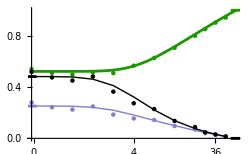

```mathematica
plotC=Show[
Plot[CVherdC/.σ->tryσ/.f->tryf/.c->(tryV x)/(1-x),{x,0,maxc},WorkingPrecision->50,PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[limratioHERD,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVind/.σx->tryσx/.σy->tryσy,{x,-0.025,0.025},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVindfarsplit/.σx->tryσx/.σy->tryσy/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVind/CVherd/.σx->tryσx/.σy->tryσy,{x,-0.025,0.025},PlotStyle->Black],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdC,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[forplottingindC,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[intplottingindC,Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingherdC[[i,1]],forplottingindC[[i,2]]/forplottingherdC[[i,2]]},{i,1,Length[forplottingindC]}],PlotStyle->{Black}],
ListPlot[Table[{intplottingindC[[i,1]],intplottingindC[[i,2]]/N[(CVherdC/.σ->tryσ/.f->tryf/.c->(tryV x)/(1-x)/.x->tab[[i]]),20]},{i,1,Length[forplottingindC]}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,1}},Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel C: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate:

```mathematica
tryLIM=Infinity;

For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
sqH=(1-f) solnsq+f (c^2+2 (σx^2+σy^2))/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
CVherdintC[tryσx,tab[[t]]]=Sqrt[sqH-mean^2]/mean;
Print[{CVherdintC[tryσx,tab[[t]]]}]
]
```

{0.522723}

{0.522724}

{0.522804}

{0.524139}

{0.533153}

{0.564706}

{0.628705}

{0.716081}

{0.812347}

{0.860761}

{0.908424}

{0.954922}

```mathematica
For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;

CVindintC[tryσ,tab[[t]]]=Sqrt[sqI[tryσ,tryc,tryf]-mean^2]/mean;Print[{CVindintC[tryσ,tab[[t]]]}]
]
```

{0.25208}

{0.252005}

{0.250453}

{0.242147}

{0.219639}

{0.182456}

{0.139753}

{0.0989067}

{0.0619696}

{0.0450455}

{0.0291103}

{0.0141151}

```mathematica
intplottingherdC=Table[{tab[[t]],CVherdintC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.522723},{1/10,0.522724},{1/5,0.522804},{3/10,0.524139},{2/5,0.533153},{1/2,0.564706},{3/5,0.628705},{7/10,0.716081},{4/5,0.812347},{17/20,0.860761},{9/10,0.908424},{19/20,0.954922}}

```mathematica
intplottingindC=Table[{tab[[t]],CVindintC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.25208},{1/10,0.252005},{1/5,0.250453},{3/10,0.242147},{2/5,0.219639},{1/2,0.182456},{3/5,0.139753},{7/10,0.0989067},{4/5,0.0619696},{17/20,0.0450455},{9/10,0.0291103},{19/20,0.0141151}}

#### Panel D: Uneven herd split [midpoint at c=4]

```mathematica
SeedRandom[43812];
```

We seek to examine a range of distances, c, between the peaks. To do so, we use c/(V+c) along the x-axis, which allows us to vary c from 0 at x=0 to infinity at x=1, within a single plot (we use V = 4 so that patches 4 sd apart are half-way along the plot). To convert the x-axis to c, we use:

```mathematica
tryV=4;
```

```mathematica
Solve[c/(tryV+c)==x,c]
```

{{c→-(4 x)/(-1+x)}}

```mathematica
tab=Join[Table[i,{i,0/10,7/10,1/10}],Table[i,{i,8/10,19/20,1/20}]]//Flatten
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,17/20,9/10,19/20}

```mathematica
numind1=90;
numind2=10;
numind=numind1+numind2;
```

```mathematica
tryf=2 (numind2/numind)(numind1/numind) (*Unequal split with 90% in one patch so f = 0.18*)
```

9/50

```mathematica
tryσ=1;
tryσx=tryσ;
tryσy=tryσ;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Join[Table[{Random[NormalDistribution[0,tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,numind1}],Table[{Random[NormalDistribution[(tryV tab[[t]])/(1-tab[[t]]),tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,numind2}]];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsimC[tryσx,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsimC[tryσx,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdD=Table[{tab[[t]],CVherdsimC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.557435},{1/10,0.514321},{1/5,0.524728},{3/10,0.539212},{2/5,0.52205},{1/2,0.611301},{3/5,0.772606},{7/10,0.975436},{4/5,1.24874},{17/20,1.48845},{9/10,1.66103},{19/20,1.88208}}

```mathematica
forplottingindD=Table[{tab[[t]],CVindsimC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.297448},{1/10,0.246918},{1/5,0.257451},{3/10,0.276005},{2/5,0.258947},{1/2,0.327936},{3/5,0.458483},{7/10,0.595828},{4/5,0.782364},{17/20,0.93942},{9/10,1.04646},{19/20,1.18934}}

These are visually indistinguishable.

```mathematica
maxc=1;
```

Below, we’ll want the ratio of CVind/CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratio=Limit[CVindfarsplit/CVherdC/.σ->tryσ/.f->tryf,c->Infinity]
```

4/(√41)

We also plot CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratioHERD=Limit[CVherdC/.σ->tryσ/.f->tryf,c->Infinity]
```

(√41)/3

Choosing x-axis tick positions:

```mathematica
{x,(tryV x)/(1-x)}/.x->tab//Transpose
```

{{0,0},{1/10,4/9},{1/5,1},{3/10,12/7},{2/5,8/3},{1/2,4},{3/5,6},{7/10,28/3},{4/5,16},{17/20,68/3},{9/10,36},{19/20,76}}

```mathematica
Solve[(tryV x)/(1-x)==2,x]
```

{{x→1/3}}

```mathematica
xticks={{0.01,"0"},{1/5,"1"},{1/3,"2"},{1/2,"4"},{3/5,"6"},{4/5,"16"},{9/10,"36"},{1,"∞"}}
```

{{0.01,0},{1/5,1},{1/3,2},{1/2,4},{3/5,6},{4/5,16},{9/10,36},{1,∞}}

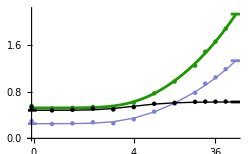

```mathematica
plotD=Show[
Plot[CVherdC/.σ->tryσ/.f->tryf/.c->(tryV x)/(1-x),{x,0,maxc},WorkingPrecision->50,PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[limratioHERD,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVind/.σx->tryσx/.σy->tryσy,{x,-0.025,0.025},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVindfarsplit/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVind/CVherd/.σx->tryσx/.σy->tryσy,{x,-0.025,0.025},PlotStyle->Black],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdD,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[forplottingindD,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[intplottingindD,{{1,CVindfarsplit/.f->tryf}}],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingherdD[[i,1]],forplottingindD[[i,2]]/forplottingherdD[[i,2]]},{i,1,Length[forplottingindD]}],PlotStyle->{Black}],
ListPlot[Join[Table[{intplottingindD[[i,1]],intplottingindD[[i,2]]/intplottingherdD[[i,2]]},{i,1,Length[forplottingindD]}],{{1,limratio}}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,2.2}},Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel D: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate:

```mathematica
tryLIM=Infinity;

For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
sqH=(1-f) solnsq+f (c^2+2 (σx^2+σy^2))/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
CVherdintC[tryσx,tab[[t]]]=Sqrt[sqH-mean^2]/mean;
Print[{CVherdintC[tryσx,tab[[t]]]}]
]
```

{0.522723}

{0.522765}

{0.523741}

{0.530381}

{0.556841}

{0.629011}

{0.770905}

{0.989866}

{1.28572}

{1.46355}

{1.6629}

{1.88566}

```mathematica
For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;

CVindintC[tryσ,tab[[t]]]=Sqrt[sqI[tryσ,tryc,tryf]-mean^2]/mean;Print[{CVindintC[tryσ,tab[[t]]]}]
]
```

{0.25208}

{0.252125}

{0.25316}

{0.259989}

{0.285368}

{0.346926}

{0.453537}

{0.603957}

{0.797324}

{0.911104}

{1.03744}

{1.17763}

```mathematica
intplottingherdD=Table[{tab[[t]],CVherdintC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.522723},{1/10,0.522765},{1/5,0.523741},{3/10,0.530381},{2/5,0.556841},{1/2,0.629011},{3/5,0.770905},{7/10,0.989866},{4/5,1.28572},{17/20,1.46355},{9/10,1.6629},{19/20,1.88566}}

```mathematica
intplottingindD=Table[{tab[[t]],CVindintC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.25208},{1/10,0.252125},{1/5,0.25316},{3/10,0.259989},{2/5,0.285368},{1/2,0.346926},{3/5,0.453537},{7/10,0.603957},{4/5,0.797324},{17/20,0.911104},{9/10,1.03744},{19/20,1.17763}}

#### Panel E: Even herd split with elongated patches [σy short]

```mathematica
SeedRandom[59238];
```

We seek to examine a range of distances, c, between the peaks, now allowing each patch to be elongated. To do so, we use c/(V+c) along the x-axis, which allows us to vary c from 0 at x=0 to infinity at x=1, within a single plot (we use V = 4 so that patches 4 sd apart are half-way along the plot). To convert the x-axis to c, we use:

```mathematica
tryV=4;
```

```mathematica
Solve[c/(tryV+c)==x,c]
```

{{c→-(4 x)/(-1+x)}}

```mathematica
tab=Join[Table[i,{i,0/10,7/10,1/10}],Table[i,{i,8/10,19/20,1/20}]]//Flatten
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,17/20,9/10,19/20}

```mathematica
numind1=50;
numind2=50;
numind=numind1+numind2;
```

```mathematica
tryf=2 (numind2/numind)(numind1/numind) (*Equal split with 50% in one patch so f = 1/2*)
```

1/2

```mathematica
tryσx=1;
tryσy=1/5;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Join[Table[{Random[NormalDistribution[0,tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,numind1}],Table[{Random[NormalDistribution[(tryV tab[[t]])/(1-tab[[t]]),tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,numind2}]];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsimC[tryσx,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsimC[tryσx,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdE=Table[{tab[[t]],CVherdsimC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.662284},{1/10,0.731637},{1/5,0.659794},{3/10,0.705657},{2/5,0.700424},{1/2,0.686867},{3/5,0.731116},{7/10,0.802803},{4/5,0.867401},{17/20,0.893992},{9/10,0.931899},{19/20,0.960352}}

```mathematica
forplottingindE=Table[{tab[[t]],CVindsimC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.318859},{1/10,0.384075},{1/5,0.265289},{3/10,0.330758},{2/5,0.301587},{1/2,0.224402},{3/5,0.154839},{7/10,0.0955232},{4/5,0.0606599},{17/20,0.0510101},{9/10,0.0256701},{19/20,0.0146037}}

Below, we’ll want the ratio of CVind/CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratio=Limit[CVindfarsplit/CVherdC/.σ->tryσx/.f->tryf,c->Infinity]
```

0

We also plot CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
CVherdfar=Limit[CVherdC/.σ->tryσx/.f->tryf,c->Infinity]
```

1

```mathematica
maxc=1;
```

```mathematica
xticks={{0.01,"0"},{1/5,"1"},{1/3,"2"},{1/2,"4"},{3/5,"6"},{4/5,"16"},{9/10,"36"},{1,"∞"}}
```

{{0.01,0},{1/5,1},{1/3,2},{1/2,4},{3/5,6},{4/5,16},{9/10,36},{1,∞}}

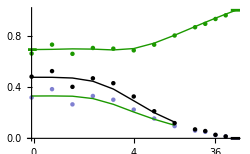

```mathematica
plotE=Show[
Plot[CVherdfar,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVindfarsplit/.σx->tryσx/.σy->tryσy/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVherd/.σx->tryσx/.σy->tryσy,{x,-0.025,0.025},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdE,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[Join[intplottingherdE,{{1,CVherdfar}}],Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[forplottingindE,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[intplottingindE,Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[Table[{forplottingherdE[[i,1]],forplottingindE[[i,2]]/forplottingherdE[[i,2]]},{i,1,Length[forplottingindE]}],PlotStyle->{Black}],
ListPlot[Table[{intplottingherdE[[i,1]],intplottingindE[[i,2]]/intplottingherdE[[i,2]]},{i,1,Length[intplottingindE]}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,1}},Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel E: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate:

```mathematica
tryLIM=Infinity;

For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
sqH=(1-f) solnsq+f (c^2+2 (σx^2+σy^2))/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
CVherdintC[tryσx,tab[[t]]]=Sqrt[sqH-mean^2]/mean;
Print[{CVherdintC[tryσx,tab[[t]]]}]
]
```

{0.69306}

{0.69489}

{0.698504}

{0.696641}

{0.690215}

{0.700981}

{0.743386}

{0.805267}

{0.872507}

{0.905818}

{0.938311}

{0.969749}

Uses slightly faster code for an even split.  Errors become too large in the numerical integration for values of c above ~10, so we stop there:

```mathematica
tryLIM=Infinity;

For[t=1,t≤9,t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;

CVindintC[tryσx,tab[[t]]]=Sqrt[sqI[tryσx,tryσy,tryc]-mean^2]/mean;Print[{CVindintC[tryσx,tab[[t]]]}]
]
```

{0.330509}

{0.331133}

{0.329018}

{0.310613}

{0.26577}

{0.205573}

{0.149184}

{0.102029}

{0.+0.844342 ⅈ}

```mathematica
intplottingherdE=Table[{tab[[t]],CVherdintC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.69306},{1/10,0.69489},{1/5,0.698504},{3/10,0.696641},{2/5,0.690215},{1/2,0.700981},{3/5,0.743386},{7/10,0.805267},{4/5,0.872507},{17/20,0.905818},{9/10,0.938311},{19/20,0.969749}}

```mathematica
intplottingindE=Table[{tab[[t]],CVindintC[tryσx,tab[[t]]]},{t,1,8}]
```

{{0,0.330509},{1/10,0.331133},{1/5,0.329018},{3/10,0.310613},{2/5,0.26577},{1/2,0.205573},{3/5,0.149184},{7/10,0.102029}}

#### Panel F: Uneven herd split with elongated patches [σy short]

```mathematica
SeedRandom[66127];
```

We seek to examine a range of distances, c, between the peaks, now allowing each patch to be elongated. To do so, we use c/(V+c) along the x-axis, which allows us to vary c from 0 at x=0 to infinity at x=1, within a single plot (we use V = 4 so that patches 4 sd apart are half-way along the plot). To convert the x-axis to c, we use:

```mathematica
tryV=4;
```

```mathematica
Solve[c/(tryV+c)==x,c]
```

{{c→-(4 x)/(-1+x)}}

```mathematica
tab=Join[Table[i,{i,0/10,7/10,1/10}],Table[i,{i,8/10,19/20,1/20}]]//Flatten
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,17/20,9/10,19/20}

```mathematica
numind1=90;
numind2=10;
numind=numind1+numind2;
```

```mathematica
tryf=2 (numind2/numind)(numind1/numind) (*Unequal split with 90% in one patch so f = 0.18*)
```

9/50

```mathematica
tryσx=1;
tryσy=1/5;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Join[Table[{Random[NormalDistribution[0,tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,numind1}],Table[{Random[NormalDistribution[(tryV tab[[t]])/(1-tab[[t]]),tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,numind2}]];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsimC[tryσx,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsimC[tryσx,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdF=Table[{tab[[t]],CVherdsimC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.691802},{1/10,0.69979},{1/5,0.691527},{3/10,0.689225},{2/5,0.710581},{1/2,0.875459},{3/5,1.00076},{7/10,1.24493},{4/5,1.50389},{17/20,1.63601},{9/10,1.80324},{19/20,1.93481}}

```mathematica
forplottingindF=Table[{tab[[t]],CVindsimC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.336235},{1/10,0.354119},{1/5,0.32242},{3/10,0.32635},{2/5,0.351786},{1/2,0.498425},{3/5,0.603531},{7/10,0.77143},{4/5,0.944348},{17/20,1.02885},{9/10,1.13972},{19/20,1.22167}}

Below, we’ll want the ratio of CVind/CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratio=Limit[CVindfarsplit/CVherdC/.σ->tryσx/.f->tryf,c->Infinity]
```

4/(√41)

We also plot CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
CVherdfar=Limit[CVherdC/.σ->tryσx/.f->tryf,c->Infinity]
```

(√41)/3

```mathematica
maxc=1;
```

```mathematica
xticks={{0.01,"0"},{1/5,"1"},{1/3,"2"},{1/2,"4"},{3/5,"6"},{4/5,"16"},{9/10,"36"},{1,"∞"}}
```

{{0.01,0},{1/5,1},{1/3,2},{1/2,4},{3/5,6},{4/5,16},{9/10,36},{1,∞}}

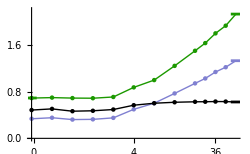

```mathematica
plotF=Show[
Plot[CVherdfar,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVindfarsplit/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVherd/.σx->tryσx/.σy->tryσy,{x,-0.025,0.025},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdF,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[Join[forplottingherdF,{{1,CVherdfar}}],Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[forplottingindF,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[forplottingindF,{{1,CVindfarsplit/.f->tryf}}],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingherdF[[i,1]],forplottingindF[[i,2]]/forplottingherdF[[i,2]]},{i,1,Length[forplottingindF]}],PlotStyle->{Black}],
ListPlot[Join[Table[{forplottingherdF[[i,1]],forplottingindF[[i,2]]/forplottingherdF[[i,2]]},{i,1,Length[forplottingindF]}],{{1,limratio}}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,2.2}},Ticks->{xticks,Automatic},ImageSize->250
]
```

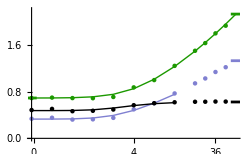

```mathematica
plotF=Show[
Plot[CVherdfar,{x,0.975,1.05},PlotStyle->{RGBColor[0.11,0.6,0.]},PlotRange->All],
Plot[CVindfarsplit/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVherd/.σx->tryσx/.σy->tryσy,{x,-0.025,0.025},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdF,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[Join[intplottingherdF,{{1,CVherdfar}}],Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[forplottingindF,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[intplottingindF,Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]},PlotRange->All],
ListPlot[Table[{forplottingherdF[[i,1]],forplottingindF[[i,2]]/forplottingherdF[[i,2]]},{i,1,Length[forplottingindF]}],PlotStyle->{Black}],
ListPlot[Table[{intplottingherdF[[i,1]],intplottingindF[[i,2]]/intplottingherdF[[i,2]]},{i,1,Length[intplottingindF]}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,2.2}},Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel F: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate:

```mathematica
tryLIM=Infinity;

For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
sqH=(1-f) solnsq+f (c^2+2 (σx^2+σy^2))/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
CVherdintC[tryσx,tab[[t]]]=Sqrt[sqH-mean^2]/mean;
Print[{CVherdintC[tryσx,tab[[t]]]}]
]
```

{0.69306}

{0.693862}

{0.698085}

{0.713045}

{0.756316}

{0.852825}

{1.01508}

{1.23438}

{1.49833}

{1.64453}

{1.79945}

{1.96279}

Errors become too large in the numerical integration for values of c above ~10, so we stop there:

```mathematica
tryLIM=Infinity;

For[t=1,t≤9,t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;

CVindintC[tryσx,tab[[t]]]=Sqrt[sqI[tryσx,tryσy,tryc,tryf]-mean^2]/mean;Print[{CVindintC[tryσx,tab[[t]]]}]
]
```

{0.330509}

{0.330934}

{0.334272}

{0.349419}

{0.393716}

{0.480143}

{0.604582}

{0.756757}

{0.+0.646899 ⅈ}

```mathematica
intplottingherdF=Table[{tab[[t]],CVherdintC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.69306},{1/10,0.693862},{1/5,0.698085},{3/10,0.713045},{2/5,0.756316},{1/2,0.852825},{3/5,1.01508},{7/10,1.23438},{4/5,1.49833},{17/20,1.64453},{9/10,1.79945},{19/20,1.96279}}

```mathematica
intplottingindF=Table[{tab[[t]],CVindintC[tryσx,tab[[t]]]},{t,1,8}]
```

{{0,0.330509},{1/10,0.330934},{1/5,0.334272},{3/10,0.349419},{2/5,0.393716},{1/2,0.480143},{3/5,0.604582},{7/10,0.756757}}

#### Panel G: Even herd split with elongated patches [σy long]

```mathematica
SeedRandom[77212];
```

We seek to examine a range of distances, c, between the peaks, now allowing each patch to be elongated. To do so, we use c/(V+c) along the x-axis, which allows us to vary c from 0 at x=0 to infinity at x=1, within a single plot (we use V = 4 so that patches 4 sd apart are half-way along the plot). To convert the x-axis to c, we use:

```mathematica
tryV=4;
```

```mathematica
Solve[c/(tryV+c)==x,c]
```

{{c→-(4 x)/(-1+x)}}

```mathematica
tab=Join[Table[i,{i,0/10,7/10,1/10}],Table[i,{i,8/10,19/20,1/20}]]//Flatten
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,17/20,9/10,19/20}

```mathematica
numind1=50;
numind2=50;
numind=100;
```

```mathematica
tryf=2 (numind2/numind)(numind1/numind) (*Equal split with 50% in one patch so f = 1/2*)
```

1/2

```mathematica
tryσx=1;
tryσy=5;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Join[Table[{Random[NormalDistribution[0,tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,numind1}],Table[{Random[NormalDistribution[(tryV tab[[t]])/(1-tab[[t]]),tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,numind2}]];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsimC[tryσx,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsimC[tryσx,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdG=Table[{tab[[t]],CVherdsimC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.686409},{1/10,0.644523},{1/5,0.704123},{3/10,0.656835},{2/5,0.617756},{1/2,0.558788},{3/5,0.554038},{7/10,0.500392},{4/5,0.582835},{17/20,0.641793},{9/10,0.731081},{19/20,0.839928}}

```mathematica
forplottingindG=Table[{tab[[t]],CVindsimC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.318933},{1/10,0.287707},{1/5,0.352326},{3/10,0.341636},{2/5,0.289254},{1/2,0.255619},{3/5,0.266793},{7/10,0.188248},{4/5,0.117176},{17/20,0.0912151},{9/10,0.0579121},{19/20,0.0308411}}

Below, we’ll want the ratio of CVind/CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratio=Limit[CVindfarsplit/CVherdC/.σ->tryσx/.f->tryf,c->Infinity]
```

0

We also plot CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
CVherdfar=Limit[CVherdC/.σ->tryσx/.f->tryf,c->Infinity]
```

1

```mathematica
maxc=1;
```

```mathematica
Solve[(tryV x)/(1-x)==6,x]
```

{{x→3/5}}

```mathematica
xticks={{0.01,"0"},{1/5,"1"},{1/3,"2"},{1/2,"4"},{3/5,"6"},{4/5,"16"},{9/10,"36"},{1,"∞"}}
```

{{0.01,0},{1/5,1},{1/3,2},{1/2,4},{3/5,6},{4/5,16},{9/10,36},{1,∞}}

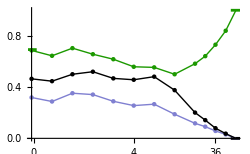

```mathematica
plotG=Show[
Plot[CVherdfar,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVindfarsplit/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVherd/.σx->tryσx/.σy->tryσy,{x,-0.025,0.025},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdG,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[Join[forplottingherdG,{{1,CVherdfar}}],Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[forplottingindG,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[forplottingindG,{{1,CVindfarsplit/.f->tryf}}],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingherdG[[i,1]],forplottingindG[[i,2]]/forplottingherdG[[i,2]]},{i,1,Length[forplottingindG]}],PlotStyle->{Black}],
ListPlot[Join[Table[{forplottingherdG[[i,1]],forplottingindG[[i,2]]/forplottingherdG[[i,2]]},{i,1,Length[forplottingindG]}],{{1,limratio}}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,1}},Ticks->{xticks,Automatic},ImageSize->250
]
```

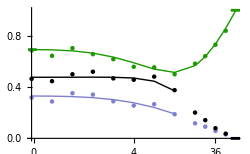

```mathematica
plotG=Show[
Plot[CVherdfar,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVindfarsplit/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVherd/.σx->tryσx/.σy->tryσy,{x,-0.025,0.025},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdG,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[Join[intplottingherdG,{{1,CVherdfar}}],Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[forplottingindG,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[intplottingindG],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingherdG[[i,1]],forplottingindG[[i,2]]/forplottingherdG[[i,2]]},{i,1,Length[forplottingindG]}],PlotStyle->{Black}],
ListPlot[Join[Table[{intplottingherdG[[i,1]],intplottingindG[[i,2]]/intplottingherdG[[i,2]]},{i,1,Length[intplottingindG]}]],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,1}},Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel G: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate:

```mathematica
tryLIM=Infinity;

For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
sqH=(1-f) solnsq+f (c^2+2 (σx^2+σy^2))/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
CVherdintC[tryσx,tab[[t]]]=Sqrt[sqH-mean^2]/mean;
Print[{CVherdintC[tryσx,tab[[t]]]}]
]
```

{0.69306}

{0.690993}

{0.682913}

{0.665284}

{0.634514}

{0.590026}

{0.540485}

{0.514872}

{0.56791}

{0.637991}

{0.736635}

{0.859176}

Uses slightly faster code for an even split.  Errors become too large in the numerical integration for values of c above ~10, so we stop there:

Errors become too large in the numerical integration for values of c above ~10, so we stop there:

```mathematica
tryLIM=Infinity;

For[t=1,t≤9,t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;

CVindintC[tryσx,tab[[t]]]=Sqrt[sqI[tryσx,tryσy,tryc]-mean^2]/mean;Print[{CVindintC[tryσx,tab[[t]]]}]
]
```

{0.330507}

{0.329581}

{0.325924}

{0.317729}

{0.30257}

{0.277792}

{0.241082}

{0.191027}

{0.+0.754737 ⅈ}

```mathematica
intplottingherdG=Table[{tab[[t]],CVherdintC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.69306},{1/10,0.690993},{1/5,0.682913},{3/10,0.665284},{2/5,0.634514},{1/2,0.590026},{3/5,0.540485},{7/10,0.514872},{4/5,0.56791},{17/20,0.637991},{9/10,0.736635},{19/20,0.859176}}

```mathematica
intplottingindG=Table[{tab[[t]],CVindintC[tryσx,tab[[t]]]},{t,1,8}]
```

{{0,0.330507},{1/10,0.329581},{1/5,0.325924},{3/10,0.317729},{2/5,0.30257},{1/2,0.277792},{3/5,0.241082},{7/10,0.191027}}

#### Panel H: Uneven herd split with elongated patches [σy long]

```mathematica
SeedRandom[827523];
```

We seek to examine a range of distances, c, between the peaks, now allowing each patch to be elongated. To do so, we use c/(V+c) along the x-axis, which allows us to vary c from 0 at x=0 to infinity at x=1, within a single plot (we use V = 4 so that patches 4 sd apart are half-way along the plot). To convert the x-axis to c, we use:

```mathematica
tryV=4;
```

```mathematica
Solve[c/(tryV+c)==x,c]
```

{{c→-(4 x)/(-1+x)}}

```mathematica
tab=Join[Table[i,{i,0/10,7/10,1/10}],Table[i,{i,8/10,19/20,1/20}]]//Flatten
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,17/20,9/10,19/20}

```mathematica
numind1=90;
numind2=10;
numind=numind1+numind2;
```

```mathematica
tryf=2 (numind2/numind)(numind1/numind) (*Unequal split with 90% in one patch so f = 0.18*)
```

9/50

```mathematica
tryσx=1;
tryσy=5;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Join[Table[{Random[NormalDistribution[0,tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,numind1}],Table[{Random[NormalDistribution[(tryV tab[[t]])/(1-tab[[t]]),tryσx]],Random[NormalDistribution[0,tryσy]]},{i,1,numind2}]];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsimC[tryσx,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsimC[tryσx,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdH=Table[{tab[[t]],CVherdsimC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.694576},{1/10,0.716758},{1/5,0.677128},{3/10,0.660936},{2/5,0.678201},{1/2,0.696807},{3/5,0.641276},{7/10,0.632392},{4/5,0.778978},{17/20,0.856287},{9/10,1.08728},{19/20,1.44195}}

```mathematica
forplottingindH=Table[{tab[[t]],CVindsimC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.338501},{1/10,0.380425},{1/5,0.304561},{3/10,0.316123},{2/5,0.334335},{1/2,0.368381},{3/5,0.31681},{7/10,0.334846},{4/5,0.460827},{17/20,0.518812},{9/10,0.675009},{19/20,0.903865}}

Below, we’ll want the ratio of CVind/CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratio=Limit[CVindfarsplit/CVherdC/.σ->tryσx/.f->tryf,c->Infinity]
```

4/(√41)

We also plot CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
CVherdfar=Limit[CVherdC/.σ->tryσx/.f->tryf,c->Infinity]
```

(√41)/3

```mathematica
maxc=1;
```

```mathematica
xticks={{0.01,"0"},{1/5,"1"},{1/3,"2"},{1/2,"4"},{3/5,"6"},{4/5,"16"},{9/10,"36"},{1,"∞"}}
```

{{0.01,0},{1/5,1},{1/3,2},{1/2,4},{3/5,6},{4/5,16},{9/10,36},{1,∞}}

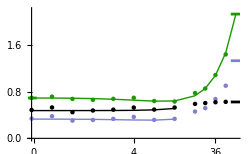

```mathematica
plotH=Show[
Plot[CVherdfar,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVindfarsplit/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVherd/.σx->tryσx/.σy->tryσy,{x,-0.025,0.025},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdH,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[Join[intplottingherdH,{{1,CVherdfar}}],Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[forplottingindH,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[intplottingindH,Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]},PlotRange->All],
ListPlot[Table[{forplottingherdH[[i,1]],forplottingindH[[i,2]]/forplottingherdH[[i,2]]},{i,1,Length[forplottingindH]}],PlotStyle->{Black}],
ListPlot[Table[{intplottingherdH[[i,1]],intplottingindH[[i,2]]/intplottingherdH[[i,2]]},{i,1,Length[intplottingindH]}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,2.2}},Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel H: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate:

```mathematica
tryLIM=Infinity;

For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
sqH=(1-f) solnsq+f (c^2+2 (σx^2+σy^2))/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;
CVherdintC[tryσx,tab[[t]]]=Sqrt[sqH-mean^2]/mean;
Print[{CVherdintC[tryσx,tab[[t]]]}]
]
```

{0.69306}

{0.692316}

{0.689402}

{0.683026}

{0.671857}

{0.655792}

{0.639368}

{0.642314}

{0.73155}

{0.856944}

{1.08236}

{1.4683}

Errors become too large in the numerical integration for values of c above ~10, so we stop there:

```mathematica
tryLIM=Infinity;

For[t=1,t≤9,t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=(1-f) soln+f NIntegrate[(ⅇ^(-(tryc-Δx)^2/(4 tryσx^2)) tryσy HypergeometricU[-1/2,0,Δx^2/(4 tryσy^2)])/(√π tryσx),{Δx,-tryLIM,tryLIM}]/.σx->tryσx/.σy->tryσy/.f->tryf/.c->tryc;

CVindintC[tryσx,tab[[t]]]=Sqrt[sqI[tryσx,tryσy,tryc,tryf]-mean^2]/mean;Print[{CVindintC[tryσx,tab[[t]]]}]
]
```

{0.330507}

{0.330174}

{0.32888}

{0.32609}

{0.321405}

{0.315496}

{0.312844}

{0.329704}

{0.+0.528792 ⅈ}

```mathematica
intplottingherdH=Table[{tab[[t]],CVherdintC[tryσx,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.69306},{1/10,0.692316},{1/5,0.689402},{3/10,0.683026},{2/5,0.671857},{1/2,0.655792},{3/5,0.639368},{7/10,0.642314},{4/5,0.73155},{17/20,0.856944},{9/10,1.08236},{19/20,1.4683}}

```mathematica
intplottingindH=Table[{tab[[t]],CVindintC[tryσx,tab[[t]]]},{t,1,Length[tab]-4}]
```

{{0,0.330507},{1/10,0.330174},{1/5,0.32888},{3/10,0.32609},{2/5,0.321405},{1/2,0.315496},{3/5,0.312844},{7/10,0.329704}}

#### Altogether

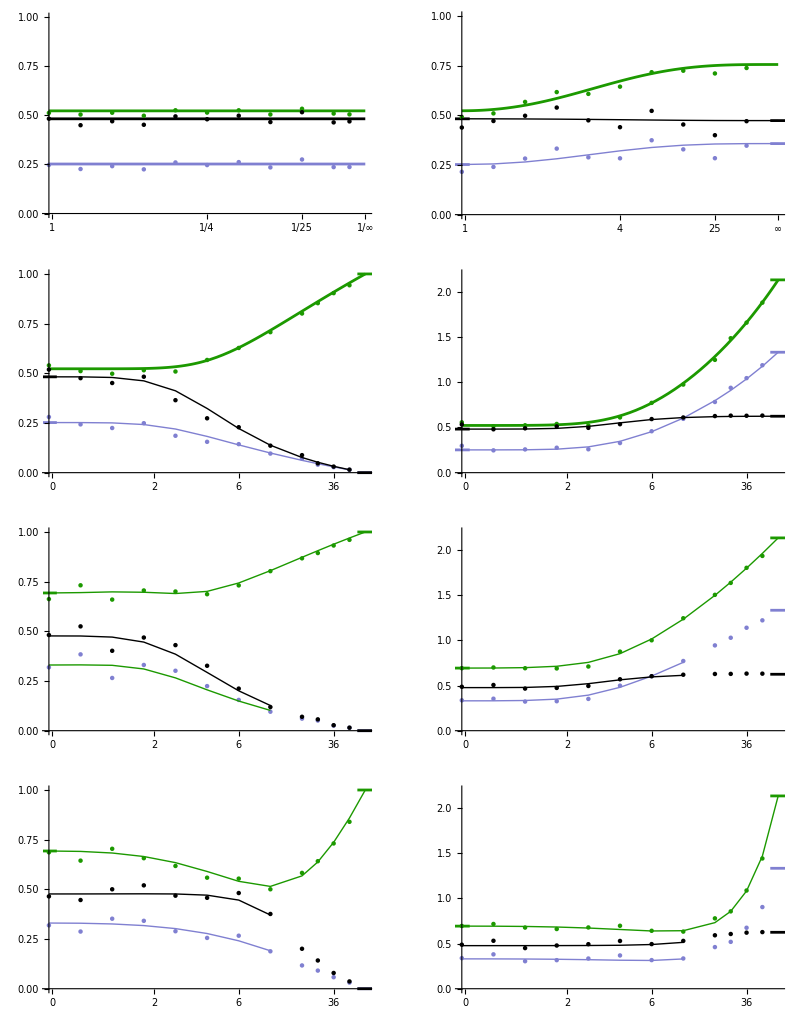

```mathematica
GraphicsGrid[{{plotA,plotB},{plotC,plotD},{plotE,plotF},{plotG,plotH}}]
```

## Individuals distributed uniformly across a rectangle

### Commands for simplifying terms [ENTER]

Assume that the positions are positive and real values:

```mathematica
fullconditions={0<x1<xmax,0<y1<ymax,0<x2<xmax,0<y2<ymax,-xmax<dx<xmax,-ymax<dy<ymax,0<dymax<ymax,_Symbol∈Reals};
```

Suppress error messages when some of the above are irrelevant:

```mathematica
Off[Limit::alimv]
```

Log terms can be gathered together using the code suggested by Alexei Boulbitch in StackExchange (https://mathematica.stackexchange.com/questions/22705/simplify-expressions-with-log)

```mathematica
collectLog[expr_]:=Module[{rule1,rule2,a,b,x},rule1=Log[a_]+Log[b_]->Log[a*b];
rule2=x_*Log[a_]->Log[a^x];
(expr/.rule1)/.rule2/.rule1/.rule2];
```

```mathematica
collectLog2[expr_]:=Module[{rule1,rule2,a,b,x},rule1=-x_ Log[a_]+x_ Log[b_]->x Log[a/b];
(expr/.rule1)];
```

```mathematica
collectLog3[expr_]:=Module[{rule1,rule2,a,b,x},rule1=x_ Log[a_]+x_ Log[b_]->x Log[a b];
(expr/.rule1)];
```

```mathematica
collectLog4[expr_]:=Module[{rule1,rule2,a,b,x},rule1=x_ Log[a_]+y_ Log[b_]->Log[a^x b^y];
(expr/.rule1)];
```

Summarizing the results:

```mathematica
soln=(xmax^5+ymax^5)/(15 xmax^2 ymax^2)+1/15 H(3-xmax^2/ymax^2-ymax^2/xmax^2)+(xmax^3 Log[(ymax+H)/xmax]+ymax^3 Log[(xmax+H)/ymax])/(6 xmax ymax) /.H->√(xmax^2+ymax^2);
```

```mathematica
FullSimplify[soln-xmax/(30 α^2)solncapt/.ymax->α xmax/.solncapt->2(1+α^5)-2 H (1-3 α^2+α^4)+Log[((1+H)/α)^(5 α^4) (H+α)^(5 α)]/.H->√(1+α^2),{xmax>0,α>0}]
```

0

```mathematica
solnX2=(xmax^2+ymax^2)/6 ;
```

```mathematica
CVherd=Sqrt[(150 α^4 (1+α^2))/solncapt^2-1]/.solncapt->2+2 α^5-2 H (1-3 α^2+α^4)+Log[((1+H)/α)^(5 α^4) (H+α)^(5 α)]/.H->√(1+α^2)/.α->ymax/xmax;
```

where α->ymax/xmax gives the asymmetry in the range.

For herds separated by a distance of c_s=c/xmax along the x-axis, the

```mathematica
solnc=soln+(f max)/(30  α^2) distcapt;
```

```mathematica
solncX2=(xmax^2+ymax^2)/6+c^2 f;
```

```mathematica
backtransform2={H->√(1+α^2),H1->√(α^2+(-1+Subscript[c, s])^2),H2->√(α^2+Subscript[c, s]^2),H3->√(α^2+(1+Subscript[c, s])^2),H4->√((-1+Subscript[c, s])^2)};
```

```mathematica
distcapt= (((1+Subscript[c, s])^5-2(1+α^5+Subscript[c, s]^5))+2 H (1-3 α^2+α^4)+2 H2 (α^2-α Subscript[c, s]-Subscript[c, s]^2) (α^2+α Subscript[c, s]-Subscript[c, s]^2)- H1 (-1+α+α^2-(-2+α) Subscript[c, s]-Subscript[c, s]^2) (-1-α+α^2+(2+α) Subscript[c, s]-Subscript[c, s]^2)+H3 (-1+α+α^2+(-2+α) Subscript[c, s]-Subscript[c, s]^2) (1+α-α^2+(2+α) Subscript[c, s]+Subscript[c, s]^2)+H4^5)+5/4 α Log[(H+α)^-4 ((H2+α)/Subscript[c, s])^(-4 Subscript[c, s]^4) ((H1+α)/H4)^(2 (-1+Subscript[c, s])^4)  ((H3+α)/(1+Subscript[c, s]))^(2 (1+Subscript[c, s])^4) ((α/(1+H))^2(1+H3+Subscript[c, s])/(-1+H1+Subscript[c, s]))^(2 α^3)(((-1+H1+Subscript[c, s]) (1+H3+Subscript[c, s]))/(H2+Subscript[c, s])^2)^(2 α^3 Subscript[c, s]) ];
```

```mathematica
CVherdC=Sqrt[(α^4 150 (1+α^2+6 f Subscript[c, s]^2))/(solncapt+f distcapt)^2-1]/.solncapt->2+2 α^5-2 H (1-3 α^2+α^4)+Log[((1+H)/α)^(5 α^4) (H+α)^(5 α)]/.H->√(1+α^2)/.backtransform2/.α->ymax/xmax/.Subscript[c, s]->c/xmax;
```

For individual-level CV:

```mathematica
intraind=1/3 1/(xmax ymax) (x1 y1 √(x1^2+y1^2)+(xmax-x1) y1 √((xmax-x1)^2+y1^2)+(ymax-y1)x1 √(x1^2+(ymax-y1)^2) +(xmax-x1) (ymax-y1)√((xmax-x1)^2+(ymax-y1)^2) )+1/6 1/(xmax ymax)Log[  ((xmax-x1+√((xmax-x1)^2+y1^2))/(√(x1^2+y1^2)-x1))^(y1^3) ((ymax-y1+√(x1^2+(ymax-y1)^2))/(√(x1^2+y1^2)-y1))^(x1^3)((√((xmax-x1)^2+y1^2)-y1)/(ymax-y1+√((xmax-x1)^2+(ymax-y1)^2)))^((x1-xmax)^3)((√((ymax-y1)^2+x1^2)-x1)/(xmax-x1+√((xmax-x1)^2+(ymax-y1)^2)))^((y1-ymax)^3)  ];
```

The results below assume xmax=ymax=max:

```mathematica
indsoln=1/15 max (2+√2+5 Log[1+√2]);
indsolnsq=0.27892463475631724 max^4;
CVind=0.16116021233464142;
CVind1=1/(2 √5);
```

A herd split in two with a chance f of drawing from different patches has a CVind of:

```mathematica
CVindfarsplit=√((1/2-f)/f);
```

A very elongated herd has:

```mathematica
CVherd1=1/(√2);
CVind1=1/(2 √5);
```

For comparison, we can numerically integrate the function for a given parameter set.

For the herd-level CV, we can use analytical results where available:

mean=soln+(f xmax)/(30  α^2) ((((1+c_s)^5-2(1+α^5+c_s^5))+2 H (1-3 α^2+α^4)+2 H2 (α^2-α c_s-c_s^2) (α^2+α c_s-c_s^2)- H1 (-1+α+α^2-(-2+α) c_s-c_s^2) (-1-α+α^2+(2+α) c_s-c_s^2)+H3 (-1+α+α^2+(-2+α) c_s-c_s^2) (1+α-α^2+(2+α) c_s+c_s^2)+H4^5)+5/4 α Log[(H+α)^-4 ((H1+α)/H4)^(2 (-1+c_s)^4)  (c_s/(H2+α))^(4 c_s^4) ((H3+α)/(1+c_s))^(2 (1+c_s)^4) ((α/(1+H))^2(1+H3+c_s)/(-1+H1+c_s))^(2 α^3)(((-1+H1+c_s) (1+H3+c_s))/(H2+c_s)^2)^(2 α^3 c_s) ])/.{H->√(1+α^2),H1->√(α^2+(-1+c_s)^2),H2->√(α^2+c_s^2),H3->√(α^2+(1+c_s)^2),H4->√((-1+c_s)^2)}/.c_s->c/xmax/.α ->ymax/xmax/.xmax->tryxmax/.ymax->tryymax/.f->tryf/.c->tryc;
sqH=(xmax^2+ymax^2)/6+c^2 f/.xmax->tryxmax/.ymax->tryymax/.f->tryf/.c->tryc;

The individual-level CV first requires  integration of the average distance of an individual to any other. Analytical results are only available for the average distance in the symmetric Gaussian case (xmax=ymax):

```mathematica
Solve[2 p (1-p)==f,p]
```

{{p→1/2 (1-√(1-2 f))},{p→1/2 (1+√(1-2 f))}}

```mathematica
avedist[x1_?NumericQ,y1_?NumericQ,xmax_?NumericQ,ymax_?NumericQ]:=1/3 1/(xmax ymax) (x1 y1 √(x1^2+y1^2)+(xmax-x1) y1 √((xmax-x1)^2+y1^2)+(ymax-y1)x1 √(x1^2+(ymax-y1)^2) +(xmax-x1) (ymax-y1)√((xmax-x1)^2+(ymax-y1)^2) )+1/6 1/(xmax ymax)Log[  ((xmax-x1+√((xmax-x1)^2+y1^2))/(√(x1^2+y1^2)-x1))^(y1^3) ((ymax-y1+√(x1^2+(ymax-y1)^2))/(√(x1^2+y1^2)-y1))^(x1^3)((√((xmax-x1)^2+y1^2)-y1)/(ymax-y1+√((xmax-x1)^2+(ymax-y1)^2)))^((x1-xmax)^3)((√((ymax-y1)^2+x1^2)-x1)/(xmax-x1+√((xmax-x1)^2+(ymax-y1)^2)))^((y1-ymax)^3)  ]; 
sqI[xmax_?NumericQ,ymax_?NumericQ,c_?NumericQ,f_?NumericQ]:=NIntegrate[((p1*(p1*avedist[x1,y1,xmax,ymax]+p2*avedist[x1+c,y1,xmax,ymax])^2+p2*(p1*avedist[x1-c,y1,xmax,ymax]+p2*avedist[x1,y1,xmax,ymax])^2)/.p2->1-p1/.p1->1/2 (1-√(1-2 f)))(1/(xmax ymax)),{x1,0,xmax},{y1,0,ymax}];(*c is displacement along x-axis*)
```

When c=0 (no split), we can speed up the integration:

```mathematica
sqI[xmax_?NumericQ,ymax_?NumericQ]:=
NIntegrate[(avedist[x1,y1,xmax,ymax,0])^2(1/(xmax ymax)),{x1,0,xmax},{y1,0,ymax}];
```

When xmax=ymax, we can speed up the integration:

```mathematica
avedist[x1_?NumericQ,y1_?NumericQ,max_?NumericQ]:=1/(6 max^2)(2 ((max-x1) √((max-x1)^2+(max-y1)^2) (max-y1)+x1 √(x1^2+(max-y1)^2) (max-y1)+(max-x1) y1 √((max-x1)^2+y1^2)+x1 y1 √(x1^2+y1^2))+Log[((-x1+√(x1^2+(max-y1)^2))/(max-x1+√((max-x1)^2+(max-y1)^2)))^((-max+y1)^3) ((-y1+√((max-x1)^2+y1^2))/(max+√((max-x1)^2+(max-y1)^2)-y1))^((-max+x1)^3) ((max-x1+√((max-x1)^2+y1^2))/(-x1+√(x1^2+y1^2)))^(y1^3) ((max+√(x1^2+(max-y1)^2)-y1)/(-y1+√(x1^2+y1^2)))^(x1^3)]); 
sqI[max_?NumericQ,c_?NumericQ,f_?NumericQ]:=NIntegrate[((p1*(p1*avedist[x1,y1,max]+p2*avedist[x1+c,y1,max])^2+p2*(p1*avedist[x1-c,y1,max]+p2*avedist[x1,y1,max])^2)/.p2->1-p1/.p1->1/2 (1-√(1-2 f)))(1/(max max)),{x1,0,max},{y1,0,max}];(*c is displacement along x-axis*)
```

The above were not sufficiently accurate for large c values, but accuracy could be improved by first taking the limit in avedist to the distant x1 value:

```mathematica
avedist[x1_?NumericQ,y1_?NumericQ,xmax_?NumericQ,ymax_?NumericQ]:=Limit[1/3 1/(xmax ymax) (xx1 y1 √(xx1^2+y1^2)+(xmax-xx1) y1 √((xmax-xx1)^2+y1^2)+(ymax-y1)xx1 √(xx1^2+(ymax-y1)^2) +(xmax-xx1) (ymax-y1)√((xmax-xx1)^2+(ymax-y1)^2) )+1/6 1/(xmax ymax)Log[  ((xmax-xx1+√((xmax-xx1)^2+y1^2))/(√(xx1^2+y1^2)-xx1))^(y1^3) ((ymax-y1+√(xx1^2+(ymax-y1)^2))/(√(xx1^2+y1^2)-y1))^(xx1^3)((√((xmax-xx1)^2+y1^2)-y1)/(ymax-y1+√((xmax-xx1)^2+(ymax-y1)^2)))^((xx1-xmax)^3)((√((ymax-y1)^2+xx1^2)-xx1)/(xmax-xx1+√((xmax-xx1)^2+(ymax-y1)^2)))^((y1-ymax)^3)  ],xx1->x1]; 
sqI[xmax_?NumericQ,ymax_?NumericQ,c_?NumericQ,f_?NumericQ]:=NIntegrate[((p1*(p1*avedist[x1,y1,xmax,ymax]+p2*avedist[x1+c,y1,xmax,ymax])^2+p2*(p1*avedist[x1-c,y1,xmax,ymax]+p2*avedist[x1,y1,xmax,ymax])^2)/.p2->1-p1/.p1->1/2 (1-√(1-2 f)))(1/(xmax ymax)),{x1,0,xmax},{y1,0,ymax}];(*c is displacement along x-axis*)
```

Also when xmax=ymax:

```mathematica
avedist[x1_?NumericQ,y1_?NumericQ,max_?NumericQ]:=Limit[1/(6 max^2)(2 ((max-xx1) √((max-xx1)^2+(max-y1)^2) (max-y1)+xx1 √(xx1^2+(max-y1)^2) (max-y1)+(max-xx1) y1 √((max-xx1)^2+y1^2)+xx1 y1 √(xx1^2+y1^2))+Log[((-xx1+√(xx1^2+(max-y1)^2))/(max-xx1+√((max-xx1)^2+(max-y1)^2)))^((-max+y1)^3) ((-y1+√((max-xx1)^2+y1^2))/(max+√((max-xx1)^2+(max-y1)^2)-y1))^((-max+xx1)^3) ((max-xx1+√((max-xx1)^2+y1^2))/(-xx1+√(xx1^2+y1^2)))^(y1^3) ((max+√(xx1^2+(max-y1)^2)-y1)/(-y1+√(xx1^2+y1^2)))^(xx1^3)]),xx1->x1]; 
sqI[max_?NumericQ,c_?NumericQ,f_?NumericQ]:=NIntegrate[((p1*(p1*avedist[x1,y1,max]+p2*avedist[x1+c,y1,max])^2+p2*(p1*avedist[x1-c,y1,max]+p2*avedist[x1,y1,max])^2)/.p2->1-p1/.p1->1/2 (1-√(1-2 f)))(1/(max max)),{x1,0,max},{y1,0,max}];(*c is displacement along x-axis*)
```

### Analysis

#### E[X]: Average distance among all pairs

Consider a simplified range that is rectangular in shape from {0,xmax} and {0,ymax}, with uniform density of individuals across the range with probability density function g[x1,y1] = 1/(xmax ymax).  

The average pairwise distance is obtained by integrating over all positions of one individual {x1,y1} and then all positions of the second individual {x2,y2}, all of which are real numbers within the range.

We carry out these integrations in steps (it is faster to use the indefinite integrals and simplify when applying the limits of integration), first rewriting g[x1,y1] g[x2,y2] Sqrt[(x2-x1)^2+(y2-y1)^2] in terms of the distances dx=x2-x1 and dy=y2-y1 and then factoring out g[x1,y1] g[x2,y2], which we’ll handle at the end.

Step 1: Integrating over dx

```mathematica
Integrate[Sqrt[dx^2+dy^2],dx];
Collect[collectLog[%//TrigToExp],Log,Simplify[#,Assumptions->fullconditions]&]
```

1/4 (2 dx √(dx^2+dy^2)-dy^2 Log[(-dx+√(dx^2+dy^2))/(dx+√(dx^2+dy^2))])

We evaluate the integrals starting at the left-most point (x1,y1), which means that we are ignoring the half of the space where (x2,y2) is left most (this halves the area that we are looking over, accounted for below).  That is, we assume here that x2>x1, so the smallest that dx can be is zero.

```mathematica
FullSimplify[(%/.dx->xmax-x1)-(%/.dx->0),fullconditions]
```

1/4 (2 √(dy^2+(x1-xmax)^2) (-x1+xmax)-dy^2 Log[(x1+√(dy^2+(x1-xmax)^2)-xmax)/(-x1+√(dy^2+(x1-xmax)^2)+xmax)])

```mathematica
FullSimplify[Integrate[%,x1],fullconditions]
```

1/6 (2 dy^2-(x1-xmax)^2) √(dy^2+(x1-xmax)^2)+1/4 dy^2 (-x1+xmax) Log[(x1+√(dy^2+(x1-xmax)^2)-xmax)/(-x1+√(dy^2+(x1-xmax)^2)+xmax)]

```mathematica
FullSimplify[(%/.x1->xmax)-Limit[%,x1->0,Assumptions->fullconditions],fullconditions]
```

1/12 (2 (-2 dy^2+xmax^2) √(dy^2+xmax^2)+4 Abs[dy]^3-3 dy^2 xmax Log[1+(2 xmax (xmax-√(dy^2+xmax^2)))/dy^2])

The Abs[dy]^3 term is coming from terms like (dy^2)^(3/2) but cause Mathematica problems when integrating (determined by relaxing the assumptions given by fullconditions).  Replacing the Abs[] terms with explicit functions:

```mathematica
%/.Abs[dy]^3->(dy^2)^(3/2);
```

Step 2: Integrating over dy

```mathematica
FullSimplify[TrigToExp[Integrate[%,dy]],fullconditions]
```

1/24 (dy √(dy^2+xmax^2) (-2 dy^2+3 xmax^2)-xmax^4 Log[xmax^2 (-dy+√(dy^2+xmax^2))]+2 dy^3 (Abs[dy]-xmax Log[1+(2 xmax (xmax-√(dy^2+xmax^2)))/dy^2]))

Again replacing the Abs[] terms with explicit functions:

```mathematica
%/.Abs[dy]->(dy^2)^(1/2);
```

We evaluate the integrals starting at the left-most point (x1,y1), which means that we are ignoring the half of the space where (x2,y2) is left most (this halves the area that we are looking over, accounted for below). That is, we assume here that y2>y1, so the smallest that dy can be is zero.

```mathematica
FullSimplify[(%/.dy->ymax-y1)-Limit[%,dy->0,Assumptions->fullconditions],fullconditions]
```

1/24 ((3 xmax^2-2 (y1-ymax)^2) √(xmax^2+(y1-ymax)^2) (-y1+ymax)+3 xmax^4 Log[xmax]+2 (y1-ymax)^3 (y1-ymax+xmax Log[1+(2 xmax (xmax-√(xmax^2+(y1-ymax)^2)))/(y1-ymax)^2])-xmax^4 Log[xmax^2 (y1+√(xmax^2+(y1-ymax)^2)-ymax)])

```mathematica
FullSimplify[Integrate[%,y1],fullconditions]
```

1/24 (2/5 (xmax^4 √(xmax^2+(y1-ymax)^2)-3 xmax^2 √(xmax^2+(y1-ymax)^2) (y1-ymax)^2+(y1-ymax)^4 (y1+√(xmax^2+(y1-ymax)^2)-ymax))+xmax^4 (y1+2 ymax) Log[xmax]+1/2 xmax (y1-ymax)^4 Log[1+(2 xmax (xmax-√(xmax^2+(y1-ymax)^2)))/(y1-ymax)^2]+xmax^4 (-y1+ymax) Log[y1+√(xmax^2+(y1-ymax)^2)-ymax])

```mathematica
FullSimplify[Limit[%,y1->ymax,Assumptions->fullconditions]-Limit[%,y1->0,Assumptions->fullconditions],fullconditions]
```

1/240 (4 (xmax^5+ymax^5-xmax^4 √(xmax^2+ymax^2)+3 xmax^2 ymax^2 √(xmax^2+ymax^2)-ymax^4 √(xmax^2+ymax^2))+10 xmax^4 ymax Log[(ymax+√(xmax^2+ymax^2))/xmax]-5 xmax ymax^4 Log[1+(2 xmax (xmax-√(xmax^2+ymax^2)))/ymax^2])

This has to be multiplied by the uniform probability density for the two individuals, g[x1,y1] g[x2,y2] = 1/(xmax ymax)^2, and multiplied by 4 to account for the fact that we have only looked at half of the x region (x1<x2) and half of the y region (y1<y2):

```mathematica
Collect[collectLog4[% 4/(xmax ymax)^2],{Log,√(xmax^2+ymax^2)},Simplify]
```

1/15 √(xmax^2+ymax^2) (3-xmax^2/ymax^2-ymax^2/xmax^2)+(4 (xmax^5+ymax^5)+Log[((ymax+√(xmax^2+ymax^2))/xmax)^(10 xmax^4 ymax) (1+(2 xmax (xmax-√(xmax^2+ymax^2)))/ymax^2)^(-5 xmax ymax^4)])/(60 xmax^2 ymax^2)

Recognizing that (1+(2 xmax (xmax-√(xmax^2+ymax^2)))/ymax^2)=(ymax^2/((xmax+√(ymax^2+xmax^2))^2)) [multiplying top and bottom by (xmax+√(ymax^2+xmax^2))^2] and simplifying, the average pairwise distance can be written as:

```mathematica
soln=(xmax^5+ymax^5)/(15 xmax^2 ymax^2)+1/15 √(xmax^2+ymax^2) (3-xmax^2/ymax^2-ymax^2/xmax^2)+Log[((ymax+√(xmax^2+ymax^2))/xmax)^(xmax^3) ((xmax+√(ymax^2+xmax^2))/ymax)^(ymax^3)]/(6 xmax ymax);
```

We can rewrite the squareroots as the hypotenuse:

```mathematica
soln=(xmax^5+ymax^5)/(15 xmax^2 ymax^2)+1/15 H(3-xmax^2/ymax^2-ymax^2/xmax^2)+(xmax^3 Log[(ymax+H)/xmax]+ymax^3 Log[(xmax+H)/ymax])/(6 xmax ymax) /.H->√(xmax^2+ymax^2);
```

In the square case, the mean distance scales with the length (xmax):

```mathematica
Simplify[soln/.ymax->xmax,xmax>0,Trig->False]
```

1/15 xmax (2+√2+5 Log[1+√2])

```mathematica
%//N
```

0.521405 xmax

Significance: By knowing the area and shape of herd home ranges (or schools of fish, flocks of birds, etc.), we can estimate the average distance between individuals, here assuming a rectangular distribution with uniform density.

#### E[X^2]: Average distance squared among all pairs

We repeat the above to calculate (x2-x1)^2+(y2-y1)^2, first rewriting in terms of the distances dx=x2-x1 and dy=y2-y1.

```mathematica
fullconditions={0<x1<xmax,0<y1<ymax,0<x2<xmax,0<y2<ymax,-xmax<dx<xmax,-ymax<dy<ymax,_Symbol∈Reals};
```

Step 1: Integrating over dx

```mathematica
Integrate[dx^2+dy^2,dx]
```

dx^3/3+dx dy^2

We evaluate the integrals starting at the left-most point (x1,y1), which means that we are ignoring the half of the space where (x2,y2) is left most (this halves the area that we are looking over, accounted for below). That is, we assume here that x2>x1, so the smallest that dx can be is zero.

```mathematica
FullSimplify[(%/.dx->xmax-x1)-(%/.dx->0),fullconditions]
```

dy^2 (-x1+xmax)+1/3 (-x1+xmax)^3

```mathematica
FullSimplify[Integrate[%,x1],fullconditions]
```

-1/12 x1 (x1-2 xmax) (6 dy^2+x1^2-2 x1 xmax+2 xmax^2)

```mathematica
FullSimplify[(%/.x1->xmax)-Limit[%,x1->0,Assumptions->fullconditions],fullconditions]
```

1/12 xmax^2 (6 dy^2+xmax^2)

```mathematica
FullSimplify[Integrate[%,dy],fullconditions]
```

1/12 dy xmax^2 (2 dy^2+xmax^2)

Step 2: Integrating over dy

We evaluate the integrals starting at the left-most point (x1,y1), which means that we are ignoring the half of the space where (x2,y2) is left most (this halves the area that we are looking over, accounted for below). That is, we assume here that y2>y1, so the smallest that dy can be is zero.

```mathematica
FullSimplify[(%/.dy->ymax-y1)-Limit[%,dy->0,Assumptions->fullconditions],fullconditions]
```

1/12 xmax^2 (xmax^2+2 (y1-ymax)^2) (-y1+ymax)

```mathematica
FullSimplify[Integrate[%,y1],fullconditions]
```

-1/24 xmax^2 y1 (y1-2 ymax) (xmax^2+y1^2-2 y1 ymax+2 ymax^2)

```mathematica
FullSimplify[Limit[%,y1->ymax,Assumptions->fullconditions]-Limit[%,y1->0,Assumptions->fullconditions],fullconditions]
```

1/24 xmax^2 ymax^2 (xmax^2+ymax^2)

This has to be multiplied by the uniform probability density for the two individuals, g[x1,y1] g[x2,y2] = 1/(xmax ymax)^2, and multiplied by 4 to account for the fact that we have only looked at half of the x region (x1<x2) and half of the y region (y1<y2):

```mathematica
%4/(xmax ymax)^2
```

1/6 (xmax^2+ymax^2)

```mathematica
solnX2=(xmax^2+ymax^2)/6 ;
```

#### Herd CV : Coefficient of variation among all pairs

Considering all pairwise distances measured in the population (ignoring individual identity), the herd CV for pairwise distances is:

```mathematica
CVherd=Sqrt[solnX2-soln^2]/soln
```

(√(1/6 (xmax^2+ymax^2)-(1/15 √(xmax^2+ymax^2) (3-xmax^2/ymax^2-ymax^2/xmax^2)+(xmax^5+ymax^5)/(15 xmax^2 ymax^2)+(ymax^3 Log[(xmax+√(xmax^2+ymax^2))/ymax]+xmax^3 Log[(ymax+√(xmax^2+ymax^2))/xmax])/(6 xmax ymax))^2))/(1/15 √(xmax^2+ymax^2) (3-xmax^2/ymax^2-ymax^2/xmax^2)+(xmax^5+ymax^5)/(15 xmax^2 ymax^2)+(ymax^3 Log[(xmax+√(xmax^2+ymax^2))/ymax]+xmax^3 Log[(ymax+√(xmax^2+ymax^2))/xmax])/(6 xmax ymax))

Alternatively, we can write the CV as Sqrt[solnX2/soln^2-1]. Next we show that the fraction solnX2/soln^2 (and hence CV) doesn’t depend on the scale, as long as the ratio of ymax/xmax remains constant (call this “α”):

```mathematica
Simplify[solnX2/soln^2/.ymax->α xmax,{xmax>0,α>0},Trig->False]
```

(150 α^4 (1+α^2))/((2+2 α^5-2 √(1+α^2)+6 α^2 √(1+α^2)-2 α^4 √(1+α^2)+5 α^4 Log[(1+√(1+α^2))/α]+5 α Log[α+√(1+α^2)])^2)

The denominator can be simplified using the hypotenuse:

```mathematica
Simplify[soln/.xmax->max/.ymax->α max,fullconditions]
```

(max (2+2 α^5-2 √(1+α^2)+6 α^2 √(1+α^2)-2 α^4 √(1+α^2)+5 α^4 Log[(1+√(1+α^2))/α]+5 α Log[α+√(1+α^2)]))/(30 α^2)

```mathematica
Simplify[collectLog[%/(max/(30  α^2))/.√(1+α^2)->H]]
```

2+2 α^5-2 H (1-3 α^2+α^4)+Log[((1+H)/α)^(5 α^4) (H+α)^(5 α)]

After a bit of cleaning, the CV can be written as:

```mathematica
CVherdALT=Sqrt[(150 α^4 (1+α^2))/solncapt^2-1]/.solncapt->2+2 α^5-2 H (1-3 α^2+α^4)+Log[((1+H)/α)^(5 α^4) (H+α)^(5 α)]/.H->√(1+α^2);
```

Thus, the CV is independent of the scale, as expected.

In the square case, the expected CV is:

```mathematica
Simplify[CVherdALT/.α->1,Trig->False]
```

√(-1+75/(2+√2+5 Log[1+√2])^2)

```mathematica
%//N
```

0.475505

As the range elongates (either becoming broader α<1 or taller α>1), CV rises towards 0.707:

```mathematica
CVherd1=Limit[CVherdALT,α->0]
```

1/(√2)

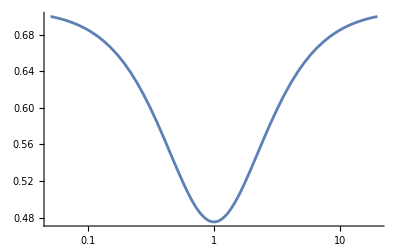

```mathematica
LogLinearPlot[CVherdALT,{α,0.05,20}]
```

```mathematica
CVherd/.ymax->1/.xmax->{0.2,1.}
```

{0.645688,0.475505}

#### Herd split patches: E[X] for two patches at a distance c from one another

Here we split the range in two and move one patch to the right by an amount c.  For the intra-individual distances, a fraction f of pairs will be drawn from different patches and the remainder from the same patch (given above). For clarity, we assume that individual 2 is from the right-most patch, displaced by c on the x axis. 

Care must be taken, however, when considering dx^2=((x2+c)-x1)^2.  we cannot just take x2>x1 because that overestimates the distance compared to the case where x2<x1.  Below we integrate directly with respect to x2 and x1 over the full range, but we start by integrating with respect to y1, where we again can consider only those cases where y2>y1 in the integration, accounting for this restriction afterwards.

Note that we will deal with the probability density function for the position of individuals in two patches at the end, which we can do because these distributions are uniform within each patch.

Updating full conditions:

```mathematica
fullconditions={0<x1<xmax,0<y1<ymax,0<x2<xmax,0<y2<ymax,0<dy<ymax,c>0,-xmax+c<dx<xmax+c,Δy>0,max>0,α>0,Subscript[c, s]>0,_Symbol∈Reals};
```

We need to integrate:

	Integrate[Sqrt[((x2+c)-x1)^2 + (y2 - y1)^2], x2]

We carry out these integrations in steps (it is faster to use the indefinite integrals and simplify when applying the limits of integration), first rewriting Sqrt[(x2-x1)^2+(y2-y1)^2] in terms of the distances dx=(x2+c)-x1 and dy=y2-y1.

We start with the simpler of the integrals, along the y-axis:

Step 1: Integrating over dy

```mathematica
Integrate[Sqrt[dx^2+dy^2],dy];
Collect[collectLog[%//TrigToExp],Log,Simplify[#,Assumptions->fullconditions]&]
```

1/4 (2 dy √(dx^2+dy^2)-dx^2 Log[(-dy+√(dx^2+dy^2))/(dy+√(dx^2+dy^2))])

We evaluate the integrals assuming that the top-most point within a patch is (x2,y2), which means that we are ignoring the half of the space where (x2,y2) is bottom most (this halves the area that we are looking over, accounted for below).

```mathematica
Simplify[collectLog[Simplify[(%/.dy->ymax-y1)-(%/.dy->0),fullconditions]],fullconditions]
```

1/4 (2 √(dx^2+(y1-ymax)^2) (-y1+ymax)-dx^2 Log[(y1+√(dx^2+(y1-ymax)^2)-ymax)/(-y1+√(dx^2+(y1-ymax)^2)+ymax)])

We can simplify the fraction in the log by noting that 
	(y1+√(dx^2+(y1-ymax)^2)-ymax)(-y1+√(dx^2+(y1-ymax)^2)+ymax)//Expand
gives dx^2	.

Allowing us to rewrite the above as:

```mathematica
1/4 (2 √(dx^2+(y1-ymax)^2) (-y1+ymax)-dx^2 Log[dx^2/((ymax-y1+√(dx^2+(y1-ymax)^2))^2)]);
```

or as:
[Avoid taking the square out of the log, as numerical errors creep in when dx can be negative.]

```mathematica
1/4 (2 √(dx^2+(y1-ymax)^2) (-y1+ymax)+dx^2 Log[((ymax-y1+√(dx^2+(y1-ymax)^2))^2)/dx^2]);
```

```mathematica
Collect[Simplify[collectLog[Integrate[%,y1]],fullconditions],Log,Simplify[#,fullconditions]&]
```

1/6 (2 dx^2-(y1-ymax)^2) √(dx^2+(y1-ymax)^2)+1/4 dx^2 (-y1+ymax) Log[dx^2/((-y1+√(dx^2+(y1-ymax)^2)+ymax)^2)]

```mathematica
Simplify[collectLog[Simplify[(%/.y1->ymax)-(%/.y1->0),fullconditions]],fullconditions]
```

1/12 (2 (-2 dx^2+ymax^2) √(dx^2+ymax^2)+4 Abs[dx]^3-3 dx^2 ymax Log[dx^2/((ymax+√(dx^2+ymax^2))^2)])

Step 2: Integrating over dx

Because we need to consider dx^2=((x2+c)-x1)^2 for both x2<x1 and x2>x1, we proceed with integrating with respect to x2 and x1 directly:
[Converting Abs[dx]^3 to (dx^2)^(3/2) allows Mathematica to integrate.]

```mathematica
1/12 (2 (-2 dx^2+ymax^2) √(dx^2+ymax^2)+4 (dx^2)^(3/2)-3 dx^2 ymax Log[dx^2/((ymax+√(dx^2+ymax^2))^2)])/.dx->x2+c-x1;

Simplify[TrigToExp[Integrate[%,x2]],fullconditions]
```

1/24 (2 (c-x1+x2) ymax^2 √((c-x1+x2)^2+ymax^2)-(c-x1+x2) (2 c^2-4 c x1+2 x1^2+4 c x2-4 x1 x2+2 x2^2-ymax^2) √((c-x1+x2)^2+ymax^2)+2 (c-x1+x2) Abs[c-x1+x2]^3-3 ymax^4 Log[-c+x1-x2+√((c-x1+x2)^2+ymax^2)]+ymax^4 (Log[-c+x1-x2+√((c-x1+x2)^2+ymax^2)]-Log[c-x1+x2+√((c-x1+x2)^2+ymax^2)])-2 (c-x1+x2)^3 ymax Log[(c-x1+x2)^2/((ymax+√((c-x1+x2)^2+ymax^2))^2)])

```mathematica
collectLog[collectLog[collectLog4[%]]]
```

1/24 (2 (c-x1+x2) ymax^2 √((c-x1+x2)^2+ymax^2)-(c-x1+x2) (2 c^2-4 c x1+2 x1^2+4 c x2-4 x1 x2+2 x2^2-ymax^2) √((c-x1+x2)^2+ymax^2)+2 (c-x1+x2) Abs[c-x1+x2]^3+Log[(-c+x1-x2+√((c-x1+x2)^2+ymax^2))^(-3 ymax^4) ((-c+x1-x2+√((c-x1+x2)^2+ymax^2))/(c-x1+x2+√((c-x1+x2)^2+ymax^2)))^(ymax^4) ((c-x1+x2)^2/((ymax+√((c-x1+x2)^2+ymax^2))^2))^(-2 (c-x1+x2)^3 ymax)])

```mathematica
1/24 (2 (c-x1+x2) ymax^2 √((c-x1+x2)^2+ymax^2)-(c-x1+x2) (2 c^2-4 c x1+2 x1^2+4 c x2-4 x1 x2+2 x2^2-ymax^2) √((c-x1+x2)^2+ymax^2)+2 (c-x1+x2) Abs[c-x1+x2]^3+Log[((c-x1+x2+√((c-x1+x2)^2+ymax^2))/ymax^4)^(ymax^4)((c-x1+x2)^2/((ymax+√((c-x1+x2)^2+ymax^2))^2))^(-2 (c-x1+x2)^3 ymax)]);
```

```mathematica
Simplify[collectLog[Simplify[(%/.x2->xmax)-(%/.x2->0),fullconditions]],fullconditions]
```

1/24 (2 (c-x1+xmax)^4-2 (c-x1) ymax^2 √(c^2-2 c x1+x1^2+ymax^2)+(c-x1) (2 c^2-4 c x1+2 x1^2-ymax^2) √(c^2-2 c x1+x1^2+ymax^2)+2 (c-x1+xmax) ymax^2 √((c-x1+xmax)^2+ymax^2)-(c-x1+xmax) (2 c^2-4 c x1+2 x1^2+4 c xmax-4 x1 xmax+2 xmax^2-ymax^2) √((c-x1+xmax)^2+ymax^2)-2 (c-x1) Abs[c-x1]^3+Log[((c-x1)^2/((ymax+√((c-x1)^2+ymax^2))^2))^(2 (c-x1)^3 ymax) ((c-x1+√((c-x1)^2+ymax^2))/(c-x1+xmax+√((c-x1+xmax)^2+ymax^2)))^(-ymax^4) ((c-x1+xmax)^2/((ymax+√((c-x1+xmax)^2+ymax^2))^2))^(-2 (c-x1+xmax)^3 ymax)])

```mathematica
Collect[Simplify[collectLog[Integrate[%/.Abs[c-x1]^3->((c-x1)^2)^(3/2),x1]],fullconditions],Log,Simplify[#,fullconditions]&];
```

```mathematica
Simplify[collectLog[Simplify[(%/.x1->xmax)-(%/.x1->0),fullconditions]],fullconditions]
```

1/240 (-4 c^5+20 c^4 xmax+40 c^3 xmax^2+40 c^2 xmax^3+20 c xmax^4+4 xmax^5+8 c^4 √(c^2+ymax^2)-24 c^2 ymax^2 √(c^2+ymax^2)+8 ymax^4 √(c^2+ymax^2)-4 c^4 √(c^2-2 c xmax+xmax^2+ymax^2)+16 c^3 xmax √(c^2-2 c xmax+xmax^2+ymax^2)-24 c^2 xmax^2 √(c^2-2 c xmax+xmax^2+ymax^2)+16 c xmax^3 √(c^2-2 c xmax+xmax^2+ymax^2)-4 xmax^4 √(c^2-2 c xmax+xmax^2+ymax^2)+12 c^2 ymax^2 √(c^2-2 c xmax+xmax^2+ymax^2)-24 c xmax ymax^2 √(c^2-2 c xmax+xmax^2+ymax^2)+12 xmax^2 ymax^2 √(c^2-2 c xmax+xmax^2+ymax^2)-4 ymax^4 √(c^2-2 c xmax+xmax^2+ymax^2)-4 c^4 √((c+xmax)^2+ymax^2)-16 c^3 xmax √((c+xmax)^2+ymax^2)-24 c^2 xmax^2 √((c+xmax)^2+ymax^2)-16 c xmax^3 √((c+xmax)^2+ymax^2)-4 xmax^4 √((c+xmax)^2+ymax^2)+12 c^2 ymax^2 √((c+xmax)^2+ymax^2)+24 c xmax ymax^2 √((c+xmax)^2+ymax^2)+12 xmax^2 ymax^2 √((c+xmax)^2+ymax^2)-4 ymax^4 √((c+xmax)^2+ymax^2)+4 Abs[c-xmax]^5+Log[((c^2/((ymax+√(c^2+ymax^2))^2))^(-2 c^3 ymax) ((c-xmax+√(c^2-2 c xmax+xmax^2+ymax^2))/(c+√(c^2+ymax^2)))^(-ymax^4) ((c-xmax)^2/((ymax+√(c^2-2 c xmax+xmax^2+ymax^2))^2))^(2 (c-xmax)^3 ymax))^(-10 c)]+Log[((c^2/((ymax+√(c^2+ymax^2))^2))^(-2 c^3 ymax) ((c-xmax+√(c^2-2 c xmax+xmax^2+ymax^2))/(c+√(c^2+ymax^2)))^(-ymax^4) ((c-xmax)^2/((ymax+√(c^2-2 c xmax+xmax^2+ymax^2))^2))^(2 (c-xmax)^3 ymax))^(10 xmax)]+Log[(c/(ymax+√(c^2+ymax^2)))^(-20 c^3 (c-2 xmax) ymax) (ymax+√(c^2-2 c xmax+xmax^2+ymax^2))^(-30 (c-xmax)^4 ymax) ((c+√(c^2+ymax^2))/(c+xmax+√((c+xmax)^2+ymax^2)))^(-10 (c+xmax) ymax^4) ((c+xmax)/(ymax+√((c+xmax)^2+ymax^2)))^(-10 (c+xmax)^4 ymax) Abs[c-xmax]^(30 (c-xmax)^4 ymax)])

```mathematica
collectLog[collectLog[collectLog4[%]]];
Collect[%,Log,Simplify[#,fullconditions]&]/.Abs[c-xmax]->((c-xmax)^2)^(1/2)
```

1/240 (4 ((c-xmax)^2)^(5/2)+4 (-c^5+xmax^5+2 c^3 xmax (5 xmax+2 √(c^2-2 c xmax+xmax^2+ymax^2)-2 √(c^2+2 c xmax+xmax^2+ymax^2))+ymax^4 (2 √(c^2+ymax^2)-√(c^2-2 c xmax+xmax^2+ymax^2)-√(c^2+2 c xmax+xmax^2+ymax^2))+c^4 (5 xmax+2 √(c^2+ymax^2)-√(c^2-2 c xmax+xmax^2+ymax^2)-√(c^2+2 c xmax+xmax^2+ymax^2))-xmax^4 (√(c^2-2 c xmax+xmax^2+ymax^2)+√(c^2+2 c xmax+xmax^2+ymax^2))+3 xmax^2 ymax^2 (√(c^2-2 c xmax+xmax^2+ymax^2)+√(c^2+2 c xmax+xmax^2+ymax^2))+c (5 xmax^4+4 xmax^3 (√(c^2-2 c xmax+xmax^2+ymax^2)-√(c^2+2 c xmax+xmax^2+ymax^2))+6 xmax ymax^2 (-√(c^2-2 c xmax+xmax^2+ymax^2)+√(c^2+2 c xmax+xmax^2+ymax^2)))+c^2 (10 xmax^3-6 xmax^2 (√(c^2-2 c xmax+xmax^2+ymax^2)+√(c^2+2 c xmax+xmax^2+ymax^2))+3 ymax^2 (-2 √(c^2+ymax^2)+√(c^2-2 c xmax+xmax^2+ymax^2)+√(c^2+2 c xmax+xmax^2+ymax^2))))+Log[((c-xmax)^2)^(15 (c-xmax)^4 ymax) (c/(ymax+√(c^2+ymax^2)))^(20 c^4 ymax) (((c-xmax)^2)^(2 (c-xmax)^3 ymax) ((c-xmax+√(c^2-2 c xmax+xmax^2+ymax^2))/(c+√(c^2+ymax^2)))^(-ymax^4))^(10 (-c+xmax)) (ymax+√(c^2-2 c xmax+xmax^2+ymax^2))^(10 (c-xmax)^4 ymax) ((c+√(c^2+ymax^2))/(c+xmax+√((c+xmax)^2+ymax^2)))^(-10 (c+xmax) ymax^4) ((c+xmax)/(ymax+√((c+xmax)^2+ymax^2)))^(-10 (c+xmax)^4 ymax)])

```mathematica
Collect[4 ((c-xmax)^2)^(5/2)+4 (-c^5+xmax^5+2 c^3 xmax (5 xmax+2 √(c^2-2 c xmax+xmax^2+ymax^2)-2 √(c^2+2 c xmax+xmax^2+ymax^2))+ymax^4 (2 √(c^2+ymax^2)-√(c^2-2 c xmax+xmax^2+ymax^2)-√(c^2+2 c xmax+xmax^2+ymax^2))+c^4 (5 xmax+2 √(c^2+ymax^2)-√(c^2-2 c xmax+xmax^2+ymax^2)-√(c^2+2 c xmax+xmax^2+ymax^2))-xmax^4 (√(c^2-2 c xmax+xmax^2+ymax^2)+√(c^2+2 c xmax+xmax^2+ymax^2))+3 xmax^2 ymax^2 (√(c^2-2 c xmax+xmax^2+ymax^2)+√(c^2+2 c xmax+xmax^2+ymax^2))+c (5 xmax^4+4 xmax^3 (√(c^2-2 c xmax+xmax^2+ymax^2)-√(c^2+2 c xmax+xmax^2+ymax^2))+6 xmax ymax^2 (-√(c^2-2 c xmax+xmax^2+ymax^2)+√(c^2+2 c xmax+xmax^2+ymax^2)))+c^2 (10 xmax^3-6 xmax^2 (√(c^2-2 c xmax+xmax^2+ymax^2)+√(c^2+2 c xmax+xmax^2+ymax^2))+3 ymax^2 (-2 √(c^2+ymax^2)+√(c^2-2 c xmax+xmax^2+ymax^2)+√(c^2+2 c xmax+xmax^2+ymax^2)))),{√(c^2-2 c xmax+xmax^2+ymax^2),√(c^2+ymax^2),√(c^2+2 c xmax+xmax^2+ymax^2),((c-xmax)^2)^(5/2)},Factor]
```

4 ((c-xmax)^2)^(5/2)-4 (c^5-5 c^4 xmax-10 c^3 xmax^2-10 c^2 xmax^3-5 c xmax^4-xmax^5)+8 (c^2-c ymax-ymax^2) (c^2+c ymax-ymax^2) √(c^2+ymax^2)-4 (c^2-2 c xmax+xmax^2+c ymax-xmax ymax-ymax^2) (c^2-2 c xmax+xmax^2-c ymax+xmax ymax-ymax^2) √(c^2-2 c xmax+xmax^2+ymax^2)-4 (c^2+2 c xmax+xmax^2-c ymax-xmax ymax-ymax^2) (c^2+2 c xmax+xmax^2+c ymax+xmax ymax-ymax^2) √(c^2+2 c xmax+xmax^2+ymax^2)

```mathematica
FullSimplify[((c-xmax)^2)^(15 (c-xmax)^4 ymax) (c/(ymax+√(c^2+ymax^2)))^(20 c^4 ymax) (((c-xmax)^2)^(2 (c-xmax)^3 ymax) ((c-xmax+√(c^2-2 c xmax+xmax^2+ymax^2))/(c+√(c^2+ymax^2)))^(-ymax^4))^(10 (-c+xmax)) (ymax+√(c^2-2 c xmax+xmax^2+ymax^2))^(10 (c-xmax)^4 ymax) ((c+√(c^2+ymax^2))/(c+xmax+√((c+xmax)^2+ymax^2)))^(-10 (c+xmax) ymax^4) ((c+xmax)/(ymax+√((c+xmax)^2+ymax^2)))^(-10 (c+xmax)^4 ymax),fullconditions]
```

(c/(ymax+√(c^2+ymax^2)))^(20 c^4 ymax) (ymax+√((c-xmax)^2+ymax^2))^(10 (c-xmax)^4 ymax) ((c+√(c^2+ymax^2))/(c+xmax+√((c+xmax)^2+ymax^2)))^(-10 (c+xmax) ymax^4) ((c+xmax)/(ymax+√((c+xmax)^2+ymax^2)))^(-10 (c+xmax)^4 ymax) Abs[c-xmax]^(30 (c-xmax)^4 ymax) (((c-xmax+√((c-xmax)^2+ymax^2))/(c+√(c^2+ymax^2)))^(-ymax^4) Abs[c-xmax]^(4 (c-xmax)^3 ymax))^(10 (-c+xmax))

Cleaning up a bit by hand (rearranging the log terms):

```mathematica
1/240 (4 ((c-xmax)^2)^(5/2)-4 (c^5-5 c^4 xmax-10 c^3 xmax^2-10 c^2 xmax^3-5 c xmax^4-xmax^5)+8 (c^2-c ymax-ymax^2) (c^2+c ymax-ymax^2) √(c^2+ymax^2)-4 (c^2-2 c xmax+xmax^2+c ymax-xmax ymax-ymax^2) (c^2-2 c xmax+xmax^2-c ymax+xmax ymax-ymax^2) √(c^2-2 c xmax+xmax^2+ymax^2)-4 (c^2+2 c xmax+xmax^2-c ymax-xmax ymax-ymax^2) (c^2+2 c xmax+xmax^2+c ymax+xmax ymax-ymax^2) √(c^2+2 c xmax+xmax^2+ymax^2)+Log[(c/(ymax+√(c^2+ymax^2)))^(20 c^4 ymax) ((ymax+√((c-xmax)^2+ymax^2))/Abs[c-xmax])^(10 (c-xmax)^4 ymax)  ((ymax+√((c+xmax)^2+ymax^2))/(c+xmax))^(10 (c+xmax)^4 ymax)  ((c+xmax+√((c+xmax)^2+ymax^2))/(c+√(c^2+ymax^2)))^(10 (c+xmax) ymax^4)((c-xmax+√((c-xmax)^2+ymax^2))/(c+√(c^2+ymax^2)))^(10 (c-xmax)ymax^4) ]);
```

This has to be multiplied by the probability density, which depends on the patch sizes.  Given that f is the probability of drawing two individuals from different patches, we have g[x1,y1] g[x2,y2]=f/(xmax ymax)^2, which accounts for the total probability of choosing the first individual from the left or the right patch. Recalling also that we only looked at half of the y region (y1<y2) and so doubling, we get :

```mathematica
ExpXwithc=2 f/(xmax^2 ymax^2)( 1/240 (4 ((c-xmax)^2)^(5/2)-4 (c^5-5 c^4 xmax-10 c^3 xmax^2-10 c^2 xmax^3-5 c xmax^4-xmax^5)+8 (c^2-c ymax-ymax^2) (c^2+c ymax-ymax^2) √(c^2+ymax^2)-4 (c^2-2 c xmax+xmax^2+c ymax-xmax ymax-ymax^2) (c^2-2 c xmax+xmax^2-c ymax+xmax ymax-ymax^2) √(c^2-2 c xmax+xmax^2+ymax^2)-4 (c^2+2 c xmax+xmax^2-c ymax-xmax ymax-ymax^2) (c^2+2 c xmax+xmax^2+c ymax+xmax ymax-ymax^2) √(c^2+2 c xmax+xmax^2+ymax^2)+Log[(c/(ymax+√(c^2+ymax^2)))^(20 c^4 ymax) ((ymax+√((c-xmax)^2+ymax^2))/Abs[c-xmax])^(10 (c-xmax)^4 ymax)  ((ymax+√((c+xmax)^2+ymax^2))/(c+xmax))^(10 (c+xmax)^4 ymax)  ((c+xmax+√((c+xmax)^2+ymax^2))/(c+√(c^2+ymax^2)))^(10 (c+xmax) ymax^4)((c-xmax+√((c-xmax)^2+ymax^2))/(c+√(c^2+ymax^2)))^(10 (c-xmax)ymax^4) ]));
```

Finally, we have to add to the solution above for points drawn from within the same patch (soln) with probability 1-f:

```mathematica
finalX=1/120 f/(xmax^2 ymax^2) (4 ((c-xmax)^2)^(5/2)-4 (c^5-5 c^4 xmax-10 c^3 xmax^2-10 c^2 xmax^3-5 c xmax^4-xmax^5)+8 (c^2-c ymax-ymax^2) (c^2+c ymax-ymax^2) √(c^2+ymax^2)-4 (c^2-2 c xmax+xmax^2+c ymax-xmax ymax-ymax^2) (c^2-2 c xmax+xmax^2-c ymax+xmax ymax-ymax^2) √(c^2-2 c xmax+xmax^2+ymax^2)-4 (c^2+2 c xmax+xmax^2-c ymax-xmax ymax-ymax^2) (c^2+2 c xmax+xmax^2+c ymax+xmax ymax-ymax^2) √(c^2+2 c xmax+xmax^2+ymax^2)+Log[(c/(ymax+√(c^2+ymax^2)))^(20 c^4 ymax) ((ymax+√((c-xmax)^2+ymax^2))/Abs[c-xmax])^(10 (c-xmax)^4 ymax)  ((ymax+√((c+xmax)^2+ymax^2))/(c+xmax))^(10 (c+xmax)^4 ymax)  ((c+xmax+√((c+xmax)^2+ymax^2))/(c+√(c^2+ymax^2)))^(10 (c+xmax) ymax^4)((c-xmax+√((c-xmax)^2+ymax^2))/(c+√(c^2+ymax^2)))^(10 (c-xmax)ymax^4) ])+
(1-f)/(30 xmax^2 ymax^2)(-2 √(xmax^2+ymax^2) (xmax^4-3 xmax^2 ymax^2+ymax^4)+2 (xmax^5+ymax^5)+5 xmax ymax (ymax^3 Log[(xmax+√(xmax^2+ymax^2))/ymax]+xmax^3 Log[(ymax+√(xmax^2+ymax^2))/xmax]));
```

We expect that this will equal the non-split patch case if either f=0 or c=0, so working with the difference from soln might be useful:

```mathematica
Collect[finalX-soln,Log,Simplify[#,fullconditions]&]/.Abs[c-xmax]->((c-xmax)^2)^(1/2);
collectLog[collectLog4[%]];
finaldif=Collect[%,Log,Simplify[#,fullconditions]&]/.Abs[c-xmax]->((c-xmax)^2)^(1/2)
```

1/(120 xmax^2 ymax^2)f (4 ((c-xmax)^2)^(5/2)+4 (-c^5+5 c^4 xmax+10 c^3 xmax^2+10 c^2 xmax^3+5 c xmax^4+xmax^5)+8 (c^2-c ymax-ymax^2) (c^2+c ymax-ymax^2) √(c^2+ymax^2)-4 ((c-xmax)^2+c ymax-xmax ymax-ymax^2) ((c-xmax)^2-c ymax+xmax ymax-ymax^2) √((c-xmax)^2+ymax^2)+8 √(xmax^2+ymax^2) (xmax^4-3 xmax^2 ymax^2+ymax^4)-8 (xmax^5+ymax^5)-4 (c^2+2 c xmax+xmax^2-c ymax-xmax ymax-ymax^2) √(c^2+2 c xmax+xmax^2+ymax^2) (c^2+xmax^2+xmax ymax-ymax^2+c (2 xmax+ymax))+Log[((c-xmax)^2)^(-5 (c-xmax)^4 ymax) (c/(ymax+√(c^2+ymax^2)))^(20 c^4 ymax) ((c-xmax+√((c-xmax)^2+ymax^2))/(c+√(c^2+ymax^2)))^(10 (c-xmax) ymax^4) (ymax+√((c-xmax)^2+ymax^2))^(10 (c-xmax)^4 ymax) (((xmax+√(xmax^2+ymax^2))/ymax)^(ymax^3) ((ymax+√(xmax^2+ymax^2))/xmax)^(xmax^3))^(-20 xmax ymax) ((c+xmax+√((c+xmax)^2+ymax^2))/(c+√(c^2+ymax^2)))^(10 (c+xmax) ymax^4) ((ymax+√((c+xmax)^2+ymax^2))/(c+xmax))^(10 (c+xmax)^4 ymax)])

Rewriting in terms of the scaled distance between the patches (c_s=c/xmax) and the extent of patch asymmetry (α=ymax/xmax):

```mathematica
Collect[Simplify[finaldif/(1/(120  α^2)f max)/.c->Subscript[c, s] xmax/.xmax->max/.ymax->α max],{√(1+α^2),√(α^2+Subscript[c, s]^2),√(α^2+(-1+Subscript[c, s])^2),√(1+α^2+2 Subscript[c, s]+Subscript[c, s]^2)},Simplify[#,fullconditions]&]/.√(1+α^2)->H/.√(α^2+(-1+Subscript[c, s])^2)->H1/.√(1+α^2+2 Subscript[c, s]+Subscript[c, s]^2)->H3/.√(α^2+Subscript[c, s]^2)->H2/.(-1+Subscript[c, s])^2->H4^2
```

4 (H4^2)^(5/2)+8 H (1-3 α^2+α^4)-8 (1+α^5)+1/max^5 Log[(H4^2)^(-5 max^5 α (-1+c_s)^4) (((1+H)/α)^(max^3 α^3))^(-20 max^2 α) (H+α)^(-20 max^5 α) (H1+α)^(10 max^5 α (-1+c_s)^4) (c_s/(H2+α))^(20 max^5 α c_s^4) ((H3+α)/(1+c_s))^(10 max^5 α (1+c_s)^4) ((-1+H1+c_s)/(H2+c_s))^(10 max^5 α^4 (-1+c_s)) ((1+H3+c_s)/(H2+c_s))^(10 max^5 α^4 (1+c_s))]+8 H2 (α^2-α c_s-c_s^2) (α^2+α c_s-c_s^2)-4 H1 (-1+α+α^2-(-2+α) c_s-c_s^2) (-1-α+α^2+(2+α) c_s-c_s^2)+4 H3 (-1+α+α^2+(-2+α) c_s-c_s^2) (1+α-α^2+(2+α) c_s+c_s^2)+4 (1+5 c_s+10 c_s^2+10 c_s^3+5 c_s^4-c_s^5)

```mathematica
backtransform2={H->√(1+α^2),H1->√(α^2+(-1+Subscript[c, s])^2),H2->√(α^2+Subscript[c, s]^2),H3->√(α^2+(1+Subscript[c, s])^2),H4->√((-1+Subscript[c, s])^2)};
```

Simplifying:

```mathematica
4 (((1+Subscript[c, s])^5-2 Subscript[c, s]^5-2 (1+α^5))+2 H (1-3 α^2+α^4)+2 H2 (α^2-α Subscript[c, s]-Subscript[c, s]^2) (α^2+α Subscript[c, s]-Subscript[c, s]^2)- H1 (-1+α+α^2-(-2+α) Subscript[c, s]-Subscript[c, s]^2) (-1-α+α^2+(2+α) Subscript[c, s]-Subscript[c, s]^2)+H3 (-1+α+α^2+(-2+α) Subscript[c, s]-Subscript[c, s]^2) (1+α-α^2+(2+α) Subscript[c, s]+Subscript[c, s]^2)+H4^5)+5 α Log[(H+α)^-4 ((H1+α)/H4)^(2 (-1+Subscript[c, s])^4)  (Subscript[c, s]/(H2+α))^(4 Subscript[c, s]^4) ((H3+α)/(1+Subscript[c, s]))^(2 (1+Subscript[c, s])^4) ((α/(1+H))^2(1+H3+Subscript[c, s])/(-1+H1+Subscript[c, s]))^(2 α^3)(((-1+H1+Subscript[c, s]) (1+H3+Subscript[c, s]))/(H2+Subscript[c, s])^2)^(2 α^3 Subscript[c, s]) ];
```

Dividing by four:

```mathematica
distcapt= (((1+Subscript[c, s])^5-2(1+α^5+Subscript[c, s]^5))+2 H (1-3 α^2+α^4)+2 H2 (α^2-α Subscript[c, s]-Subscript[c, s]^2) (α^2+α Subscript[c, s]-Subscript[c, s]^2)- H1 (-1+α+α^2-(-2+α) Subscript[c, s]-Subscript[c, s]^2) (-1-α+α^2+(2+α) Subscript[c, s]-Subscript[c, s]^2)+H3 (-1+α+α^2+(-2+α) Subscript[c, s]-Subscript[c, s]^2) (1+α-α^2+(2+α) Subscript[c, s]+Subscript[c, s]^2)+H4^5)+5/4 α Log[(H+α)^-4 ((H1+α)/H4)^(2 (-1+Subscript[c, s])^4)  (Subscript[c, s]/(H2+α))^(4 Subscript[c, s]^4) ((H3+α)/(1+Subscript[c, s]))^(2 (1+Subscript[c, s])^4) ((α/(1+H))^2(1+H3+Subscript[c, s])/(-1+H1+Subscript[c, s]))^(2 α^3)(((-1+H1+Subscript[c, s]) (1+H3+Subscript[c, s]))/(H2+Subscript[c, s])^2)^(2 α^3 Subscript[c, s]) ];
```

Altogether, E[X]=soln+(f max)/(30  α^2) distcapt.

```mathematica
solnc=soln+(f max)/(30  α^2) distcapt;
```

In the symmetric case:

```mathematica
distcapt/.α->1
```

-16-8 H+4 H4^5+Log[(((1+H1)/H4)^(10 (-1+c_s)^4) (c_s/(1+H2))^(20 c_s^4) ((1+H3)/(1+c_s))^(10 (1+c_s)^4) (1+H3+c_s)^10 (((-1+H1+c_s) (1+H3+c_s))/(H2+c_s)^2)^(10 c_s))/((1+H)^40 (-1+H1+c_s)^10)]+8 H2 (1-c_s-c_s^2) (1+c_s-c_s^2)-4 H1 (1+c_s-c_s^2) (-1+3 c_s-c_s^2)+4 H3 (1-c_s-c_s^2) (1+3 c_s+c_s^2)+4 (-2 c_s^5+(1+c_s)^5)

```mathematica
backtransform={H->√(xmax^2+ymax^2),H1->√((c-xmax)^2+ymax^2),H2->√(c^2+ymax^2),H3->√((c+xmax)^2+ymax^2)};
```

Note that while distcapt cannot be directly evaluated when the patch distance is zero, if we evaluate the log and the non-log terms separately they disappear:

```mathematica
Simplify[distcapt/.backtransform2/.Log[x_]->0/.Subscript[c, s]->0,fullconditions]
```

0

```mathematica
Log[Simplify[Exp[(distcapt-(distcapt/.Log[x_]->0))/(5 α/4)]/.H1->H/.H3->H/.H2->α/.H4->1/.H->√(1+α^2)/.(Subscript[c, s]/α)^(4 Subscript[c, s]^4)->1/.Subscript[c, s]->0,fullconditions]]
```

0

assuming that α does not also vanish so that (c_s/α)^(4 c_s^4) can be evaluated in the limit as 1.

#### Herd split patches: E[X]^2 for two patches at a distance c from one another

Repeating the above but for the squared distance:

	Integrate[((x2+c)-x1)^2 + (y2 - y1)^2, x2]

We carry out these integrations in steps (it is faster to use the indefinite integrals and simplify when applying the limits of integration), first rewriting (x2-x1)^2+(y2-y1)^2 in terms of the distances dx=(x2+c)-x1 and dy=y2-y1.

We start with the simpler of the integrals, along the y-axis:

Step 1: Integrating over dy

```mathematica
Integrate[dx^2+dy^2,dy]
```

dx^2 dy+dy^3/3

We evaluate the integrals assuming that the top-most point within a patch is (x2,y2), which means that we are ignoring the half of the space where (x2,y2) is bottom most (this halves the area that we are looking over, accounted for below).

```mathematica
Simplify[(%/.dy->ymax-y1)-(%/.dy->0),fullconditions]
```

dx^2 (-y1+ymax)+1/3 (-y1+ymax)^3

Next integrating over y1

```mathematica
Simplify[Integrate[%,y1]]
```

-1/12 y1 (y1-2 ymax) (6 dx^2+y1^2-2 y1 ymax+2 ymax^2)

```mathematica
Simplify[(%/.y1->ymax)-(%/.y1->0),fullconditions]
```

1/12 ymax^2 (6 dx^2+ymax^2)

Step 2: Integrating over dx

Because we need to consider dx^2=((x2+c)-x1)^2 for both x2<x1 and x2>x1, we proceed with integrating with respect to x2 and x1 directly:

```mathematica
1/12 ymax^2 (6 dx^2+ymax^2)/.dx->x2+c-x1;

Simplify[Integrate[%,x2],fullconditions]
```

1/12 ymax^2 (2 (c-x1+x2)^3+x2 ymax^2)

```mathematica
Simplify[(%/.x2->xmax)-(%/.x2->0),fullconditions]
```

1/12 ymax^2 (-2 (c-x1)^3+2 (c-x1+xmax)^3+xmax ymax^2)

Next integrating with respect to x1:

```mathematica
Simplify[Integrate[%,x1],fullconditions]
```

1/24 ymax^2 ((c-x1)^4-(c-x1+xmax)^4+2 x1 xmax ymax^2)

```mathematica
Simplify[(%/.x1->xmax)-(%/.x1->0),fullconditions]
```

1/12 xmax^2 ymax^2 (6 c^2+xmax^2+ymax^2)

This correctly reduces to solnX2=1/6 (xmax^2+ymax^2) when c=0.

This has to be multiplied by the probability density, which depends on the patch sizes.  Given that f is the probability of drawing two individuals from different patches, we have g[x1,y1] g[x2,y2]=f/(xmax ymax)^2, which accounts for the total probability of choosing the first individual from the left or the right patch. Recalling also that we only looked at half of the y region (y1<y2) and so doubling, we get :

```mathematica
2 f/(xmax^2 ymax^2)1/12 xmax^2 ymax^2 (6 c^2+xmax^2+ymax^2)
```

1/6 f (6 c^2+xmax^2+ymax^2)

Finally, we have to add the solution above for points drawn from within the same patch (soln) with probability 1-f:

```mathematica
solncX2=1/6 (1-f) (xmax^2+ymax^2)+1/6 f (6 c^2+xmax^2+ymax^2);
```

which can be more simply written as the non-split case (solnX2) plus a departure that depends on c and f:

```mathematica
solncX2=(xmax^2+ymax^2)/6+c^2 f;
```

#### Herd split patches: CV

```mathematica
Sqrt[((xmax^2+ymax^2)/6+c^2 f)/((soln+(f max)/(30  α^2) distcapt)^2)-1];
```

Writing E[X]^2 and soln in terms of the scaled parameters:

```mathematica
Factor[(xmax^2+ymax^2)/6+c^2 f/.c->Subscript[c, s] xmax/.xmax->max/.ymax->α max]
```

1/6 max^2 (1+α^2+6 f c_s^2)

```mathematica
Simplify[soln/.c->Subscript[c, s] xmax/.xmax->max/.ymax->α max,fullconditions]
```

(max (2+2 α^5-2 √(1+α^2)+6 α^2 √(1+α^2)-2 α^4 √(1+α^2)+5 α^4 Log[(1+√(1+α^2))/α]+5 α Log[α+√(1+α^2)]))/(30 α^2)

```mathematica
solncapt=Simplify[collectLog[%/(max/(30  α^2))/.√(1+α^2)->H]]
```

2+2 α^5-2 H (1-3 α^2+α^4)+Log[((1+H)/α)^(5 α^4) (H+α)^(5 α)]

Altogether, we have:

```mathematica
Sqrt[(1/6 max^2 (1+α^2+6 f Subscript[c, s]^2))/((max/(30  α^2)solncapt+(f max)/(30  α^2) distcapt)^2)-1];
```

which equals

```mathematica
CVherdALTc=Sqrt[(α^4 150 (1+α^2+6 f Subscript[c, s]^2))/(solncapt+f distcapt)^2-1];
```

This is scale free (neither solncapt nor distcapt depend on the the size of the patches, just on α and c_s) and reduces correctly to the non-split case, CVherdALT=Sqrt[(150 α^4 (1+α^2))/solncapt^2-1], when f=0 or when c=0.

#### E[X_i]: Average pairwise distance from individual i

We now focus on an individual at position {x1,y1} and determine its average pairwise distance to all other individuals measured.  This is then used as the basis for calculating the CV among individuals. Again working with dx=x2-x1 and dy=y2-y1:

Step 1: Integrating over dx and dy

```mathematica
Integrate[Sqrt[dx^2+dy^2],dx];
Collect[collectLog[%//TrigToExp],Log,Simplify[#,Assumptions->fullconditions]&]
```

1/4 (2 dx √(dx^2+dy^2)-dy^2 Log[(-dx+√(dx^2+dy^2))/(dx+√(dx^2+dy^2))])

```mathematica
Simplify[TrigToExp[Integrate[%,dy]],fullconditions,Trig->False];
Collect[Nest[collectLog,%,Length[%]],Log,Simplify]
```

1/12 (4 dx dy √(dx^2+dy^2)+Log[(1-dy/(√(dx^2+dy^2)))^(-dx^3) (1+dy/(√(dx^2+dy^2)))^(dx^3) ((-dx+√(dx^2+dy^2))/(dx+√(dx^2+dy^2)))^(-dy^3)])

Tidying up:

```mathematica
1/12 (4 dx dy √(dx^2+dy^2)+Log[((dy+√(dx^2+dy^2))/dx)^(2 dx^3) ((dx+√(dx^2+dy^2))/dy)^(2 dy^3)]);
```

For an individual at position x1, the integral of x2 ranges from x2 = 0 (dx = -x1) to x2 = xmax (dx = xmax-x1):

```mathematica
Simplify[(%/.dx->xmax-x1)-(%/.dx->-x1),fullconditions,Trig->False];
Collect[Nest[collectLog,%,Length[%]],Log,Simplify]
```

1/12 (4 dy x1 √(dy^2+x1^2)+4 dy √(dy^2+(x1-xmax)^2) (-x1+xmax)+Log[(-(dy+√(dy^2+x1^2))/x1)^(2 x1^3) ((-x1+√(dy^2+x1^2))/dy)^(-2 dy^3) ((dy+√(dy^2+(x1-xmax)^2))/(-x1+xmax))^(2 (-x1+xmax)^3) ((-x1+√(dy^2+(x1-xmax)^2)+xmax)/dy)^(2 dy^3)])

For an individual at position y1, the integral of y2 ranges from y2 = 0 (dy = -y1) to y2 = ymax (dy = ymax-y1):

```mathematica
FullSimplify[(%/.dy->ymax-y1)-(%/.dy->-y1),fullconditions];
Collect[Nest[collectLog,%,Length[%]],Log,Simplify]
```

1/12 (4 x1 y1 √(x1^2+y1^2)+4 (-x1+xmax) y1 √((x1-xmax)^2+y1^2)+4 (x1-xmax) √((x1-xmax)^2+(y1-ymax)^2) (y1-ymax)+4 x1 √(x1^2+(y1-ymax)^2) (-y1+ymax)+Log[((y1-√(x1^2+y1^2))/x1)^(-2 x1^3) ((y1-√((x1-xmax)^2+y1^2))/(x1-xmax))^(2 (x1-xmax)^3) (((x1+√(x1^2+y1^2)) (-x1+xmax+√((x1-xmax)^2+y1^2)))/y1^2)^(2 y1^3) ((-x1+√(x1^2+(y1-ymax)^2))/(-x1+xmax+√((x1-xmax)^2+(y1-ymax)^2)))^(2 (y1-ymax)^3) (-(-y1+√(x1^2+(y1-ymax)^2)+ymax)/x1)^(2 x1^3) ((-y1+√((x1-xmax)^2+(y1-ymax)^2)+ymax)/(-x1+xmax))^(2 (-x1+xmax)^3)])

After a few rounds of tidying up and multiplying by the probability density function for the position of the second individual g[x2,y2]=1/(xmax ymax), we have the individual’s average pairwise distance to others:

```mathematica
intraind=1/3 1/(xmax ymax) (x1 y1 √(x1^2+y1^2)+(xmax-x1) y1 √((xmax-x1)^2+y1^2)+(ymax-y1)x1 √(x1^2+(ymax-y1)^2) +(xmax-x1) (ymax-y1)√((xmax-x1)^2+(ymax-y1)^2) )+1/6 1/(xmax ymax)Log[  ((xmax-x1+√((xmax-x1)^2+y1^2))/(√(x1^2+y1^2)-x1))^(y1^3) ((ymax-y1+√(x1^2+(ymax-y1)^2))/(√(x1^2+y1^2)-y1))^(x1^3)((√((xmax-x1)^2+y1^2)-y1)/(ymax-y1+√((xmax-x1)^2+(ymax-y1)^2)))^((x1-xmax)^3)((√((ymax-y1)^2+x1^2)-x1)/(xmax-x1+√((xmax-x1)^2+(ymax-y1)^2)))^((y1-ymax)^3)  ];
```

#### OverBar[E[X_i]]: Average of the individual average pairwise distances [same as soln for E[X] above]

Here, we calculate the average of E[X_i] (given by “intraind”) over all positions {x1,y1} where the individual i may be.

We start by breaking intraind into two parts, without and with the log:

```mathematica
part1=1/3 1/(xmax ymax) (x1 y1 √(x1^2+y1^2)+(xmax-x1) y1 √((xmax-x1)^2+y1^2)+(ymax-y1)x1 √(x1^2+(ymax-y1)^2) +(xmax-x1) (ymax-y1)√((xmax-x1)^2+(ymax-y1)^2) );
part2=1/6 1/(xmax ymax)Log[  ((xmax-x1+√((xmax-x1)^2+y1^2))/(√(x1^2+y1^2)-x1))^(y1^3) ((ymax-y1+√(x1^2+(ymax-y1)^2))/(√(x1^2+y1^2)-y1))^(x1^3)((√((xmax-x1)^2+y1^2)-y1)/(ymax-y1+√((xmax-x1)^2+(ymax-y1)^2)))^((x1-xmax)^3)((√((ymax-y1)^2+x1^2)-x1)/(xmax-x1+√((xmax-x1)^2+(ymax-y1)^2)))^((y1-ymax)^3)  ];
```

Integrating part1:

```mathematica
Integrate[part1,x1,y1];
Collect[Factor[%],√(x1^2-2 x1 xmax+xmax^2+y1^2-2 y1 ymax+ymax^2),Simplify]
```

-(-(x1^2+y1^2)^(5/2)+(x1^2-2 x1 xmax+xmax^2+y1^2)^(5/2)+(x1^2+(y1-ymax)^2)^(5/2))/(45 xmax ymax)+((x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)^2 √(x1^2-2 x1 xmax+xmax^2+y1^2-2 y1 ymax+ymax^2))/(45 xmax ymax)

```mathematica
FullSimplify[(%/.x1->xmax)-(%/.x1->0),fullconditions];
FullSimplify[(%/.y1->ymax)-(%/.y1->0),fullconditions]
```

(4 (-xmax^5+xmax^4 √(xmax^2+ymax^2)+2 xmax^2 ymax^2 √(xmax^2+ymax^2)+ymax^4 (-ymax+√(xmax^2+ymax^2))))/(45 xmax ymax)

Integrating part2 (multiplied by 6xmax ymax  for ease of calculation) was more involved.

First integrating with respect to x1 and y1:

```mathematica
Integrate[6xmax ymax part2,x1];
Collect[Nest[collectLog,%,Length[%]],Log,Simplify[#,fullconditions]&];
Collect[Nest[collectLog,%,Length[%]],Log,Simplify[#,fullconditions]&];
Collect[Nest[collectLog,%,Length[%]],Log,Simplify[#,fullconditions]&]
```

1/12 (y1 (x1^2-14 y1^2) √(x1^2+y1^2)-y1 (x1^2-2 x1 xmax+xmax^2-14 y1^2) √(x1^2-2 x1 xmax+xmax^2+y1^2)-(x1^2-14 (y1-ymax)^2) √(x1^2+(y1-ymax)^2) (y1-ymax)+(x1^2-2 x1 xmax+xmax^2-14 (y1-ymax)^2) √(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2) (y1-ymax)+Log[(x1-xmax+√(x1^2-2 x1 xmax+xmax^2+y1^2))^(12 xmax y1^3) ((-x1+xmax+√(x1^2-2 x1 xmax+xmax^2+y1^2))/(-x1+√(x1^2+y1^2)))^(12 x1 y1^3) ((x1-√(x1^2+(y1-ymax)^2))/(x1-xmax-√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)))^(12 x1 (y1-ymax)^3) (x1-xmax+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2))^(-12 xmax (y1-ymax)^3) ((y1+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)-ymax)/(y1+√(x1^2-2 x1 xmax+xmax^2+y1^2)))^(3 xmax^4) ((-y1+√(x1^2+(y1-ymax)^2)+ymax)/(-y1+√(x1^2+y1^2)))^(3 x1^4) ((-y1+√(x1^2-2 x1 xmax+xmax^2+y1^2))/(-y1+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)+ymax))^(3 x1 (x1^3-4 x1^2 xmax+6 x1 xmax^2-4 xmax^3))])

```mathematica
Integrate[%,y1];
Collect[Nest[collectLog,%,Length[%]],Log,Simplify[#,fullconditions]&];
Collect[Nest[collectLog,%,Length[%]],Log,Simplify[#,fullconditions]&];
Collect[Nest[collectLog,%,Length[%]],Log,Simplify[#,fullconditions]&]
```

1/12 (-11/5 x1^4 √(x1^2-2 x1 xmax+xmax^2+y1^2)+44/5 x1^3 xmax √(x1^2-2 x1 xmax+xmax^2+y1^2)-11/5 xmax^4 √(x1^2-2 x1 xmax+xmax^2+y1^2)+3/5 xmax^2 y1^2 √(x1^2-2 x1 xmax+xmax^2+y1^2)+14/5 y1^4 √(x1^2-2 x1 xmax+xmax^2+y1^2)+3/5 x1^2 (-22 xmax^2+y1^2) √(x1^2-2 x1 xmax+xmax^2+y1^2)+√(x1^2+y1^2) (-5 x1^4+x1^2 y1^2)+√(x1^2-2 x1 xmax+xmax^2+y1^2) (5 (x1-xmax)^4-(x1-xmax)^2 y1^2)+2/5 x1 √(x1^2-2 x1 xmax+xmax^2+y1^2) (22 xmax^3-3 xmax y1^2)+1/5 √(x1^2+y1^2) (11 x1^4-3 x1^2 y1^2-14 y1^4)+5 x1^4 √(x1^2+(y1-ymax)^2)-5 x1^2 (x1-xmax)^2 √(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)+10 x1 (x1-xmax)^2 xmax √(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)-5 (x1-xmax)^2 xmax^2 √(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)+1/5 (11 x1^2-22 x1 xmax+11 xmax^2-14 (y1-ymax)^2) (x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)^(3/2)+1/5 (x1^2+(y1-ymax)^2)^(3/2) (-11 x1^2+14 (y1-ymax)^2)-x1^2 √(x1^2+(y1-ymax)^2) (y1-ymax)^2+(x1-xmax)^2 √(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2) (y1-ymax)^2-3 xmax y1^3 ymax+9/2 xmax y1^2 ymax^2-3 xmax y1 ymax^3+Log[(x1-xmax+√(x1^2-2 x1 xmax+xmax^2+y1^2))^(3 xmax y1^4) ((-x1+√(x1^2+y1^2))/(-x1+xmax+√(x1^2-2 x1 xmax+xmax^2+y1^2)))^(-3 x1 y1^4) (x1+√(x1^2+(y1-ymax)^2))^(-3 x1 ymax^4) ((x1-√(x1^2+(y1-ymax)^2))/(x1-xmax-√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)))^(3 x1 y1 (y1^3-4 y1^2 ymax+6 y1 ymax^2-4 ymax^3)) (x1-xmax+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2))^(3 x1 ymax^4+3 xmax (y1-ymax)^3 (3 y1+ymax)) (y1+√(x1^2+(y1-ymax)^2)-ymax)^(3 x1^4 ymax) (y1+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)-ymax)^(-3 (x1-xmax)^4 ymax) ((x1-xmax+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2))^(-12 xmax (y1-ymax)^3) ((y1+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)-ymax)/(y1+√(x1^2-2 x1 xmax+xmax^2+y1^2)))^(3 xmax^4))^y1 ((-y1+√(x1^2+y1^2))/(-y1+√(x1^2+(y1-ymax)^2)+ymax))^(-3 x1^4 y1) ((-y1+√(x1^2-2 x1 xmax+xmax^2+y1^2))/(-y1+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)+ymax))^(3 x1 (x1^3-4 x1^2 xmax+6 x1 xmax^2-4 xmax^3) y1)])

Breaking the above into two parts (without and with the log):

```mathematica
part2a=1/12( -11/5 x1^4 √(x1^2-2 x1 xmax+xmax^2+y1^2)+44/5 x1^3 xmax √(x1^2-2 x1 xmax+xmax^2+y1^2)-11/5 xmax^4 √(x1^2-2 x1 xmax+xmax^2+y1^2)+3/5 xmax^2 y1^2 √(x1^2-2 x1 xmax+xmax^2+y1^2)+14/5 y1^4 √(x1^2-2 x1 xmax+xmax^2+y1^2)+3/5 x1^2 (-22 xmax^2+y1^2) √(x1^2-2 x1 xmax+xmax^2+y1^2)+√(x1^2+y1^2) (-5 x1^4+x1^2 y1^2)+√(x1^2-2 x1 xmax+xmax^2+y1^2) (5 (x1-xmax)^4-(x1-xmax)^2 y1^2)+2/5 x1 √(x1^2-2 x1 xmax+xmax^2+y1^2) (22 xmax^3-3 xmax y1^2)+1/5 √(x1^2+y1^2) (11 x1^4-3 x1^2 y1^2-14 y1^4)+5 x1^4 √(x1^2+(y1-ymax)^2)-5 x1^2 (x1-xmax)^2 √(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)+10 x1 (x1-xmax)^2 xmax √(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)-5 (x1-xmax)^2 xmax^2 √(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)+1/5 (11 x1^2-22 x1 xmax+11 xmax^2-14 (y1-ymax)^2) (x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)^(3/2)+1/5 (x1^2+(y1-ymax)^2)^(3/2) (-11 x1^2+14 (y1-ymax)^2)-x1^2 √(x1^2+(y1-ymax)^2) (y1-ymax)^2+(x1-xmax)^2 √(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2) (y1-ymax)^2-3 xmax y1^3 ymax+9/2 xmax y1^2 ymax^2-3 xmax y1 ymax^3);
part2b=1/12(Log[(x1-xmax+√(x1^2-2 x1 xmax+xmax^2+y1^2))^(3 xmax y1^4) ((-x1+√(x1^2+y1^2))/(-x1+xmax+√(x1^2-2 x1 xmax+xmax^2+y1^2)))^(-3 x1 y1^4) (x1+√(x1^2+(y1-ymax)^2))^(-3 x1 ymax^4) ((x1-√(x1^2+(y1-ymax)^2))/(x1-xmax-√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)))^(3 x1 y1 (y1^3-4 y1^2 ymax+6 y1 ymax^2-4 ymax^3)) (x1-xmax+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2))^(3 x1 ymax^4+3 xmax (y1-ymax)^3 (3 y1+ymax)) (y1+√(x1^2+(y1-ymax)^2)-ymax)^(3 x1^4 ymax) (y1+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)-ymax)^(-3 (x1-xmax)^4 ymax) ((x1-xmax+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2))^(-12 xmax (y1-ymax)^3) ((y1+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)-ymax)/(y1+√(x1^2-2 x1 xmax+xmax^2+y1^2)))^(3 xmax^4))^y1 ((-y1+√(x1^2+y1^2))/(-y1+√(x1^2+(y1-ymax)^2)+ymax))^(-3 x1^4 y1) ((-y1+√(x1^2-2 x1 xmax+xmax^2+y1^2))/(-y1+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)+ymax))^(3 x1 (x1^3-4 x1^2 xmax+6 x1 xmax^2-4 xmax^3) y1)]);
```

Evaluating part2a over the limits of integration:

```mathematica
part2a;
Simplify[Limit[%,x1->xmax,Assumptions->fullconditions]-Limit[%,x1->0,Assumptions->fullconditions],fullconditions];
Simplify[Limit[%,y1->ymax,Assumptions->fullconditions]-Limit[%,y1->0,Assumptions->fullconditions],fullconditions]
```

-2/15 (-7 xmax^5+7 xmax^4 √(xmax^2+ymax^2)-xmax^2 ymax^2 √(xmax^2+ymax^2)+7 ymax^4 (-ymax+√(xmax^2+ymax^2)))

Using Simplify[PowerExpand[%]] inside the Log, part2b can be simplified as:

```mathematica
part2b=1/12 Log[(-x1+√(x1^2+y1^2))^(-3 x1 y1^4) (-y1+√(x1^2+y1^2))^(-3 x1^4 y1) (x1-xmax+√(x1^2-2 x1 xmax+xmax^2+y1^2))^(3 xmax y1^4) (-x1+xmax+√(x1^2-2 x1 xmax+xmax^2+y1^2))^(3 x1 y1^4) (-y1+√(x1^2-2 x1 xmax+xmax^2+y1^2))^(3 x1 (x1^3-4 x1^2 xmax+6 x1 xmax^2-4 xmax^3) y1) (y1+√(x1^2-2 x1 xmax+xmax^2+y1^2))^(-3 xmax^4 y1) (x1-√(x1^2+(y1-ymax)^2))^(3 x1 y1 (y1^3-4 y1^2 ymax+6 y1 ymax^2-4 ymax^3)) (x1+√(x1^2+(y1-ymax)^2))^(-3 x1 ymax^4) (x1-xmax-√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2))^(-3 x1 y1 (y1^3-4 y1^2 ymax+6 y1 ymax^2-4 ymax^3)) (x1-xmax+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2))^(-3 xmax (y1-ymax)^4+3 x1 ymax^4) (y1+√(x1^2+(y1-ymax)^2)-ymax)^(3 x1^4 ymax) (y1+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)-ymax)^(3 xmax^4 y1-3 (x1-xmax)^4 ymax) (-y1+√(x1^2+(y1-ymax)^2)+ymax)^(3 x1^4 y1) (-y1+√(x1^2-2 x1 xmax+xmax^2+(y1-ymax)^2)+ymax)^(-3 x1 (x1^3-4 x1^2 xmax+6 x1 xmax^2-4 xmax^3) y1)];
```

Evaluating part2b over the limits of integration:

```mathematica
Simplify[Limit[%,x1->xmax,Assumptions->fullconditions]-Limit[%,x1->0,Assumptions->fullconditions],fullconditions];
Collect[Nest[collectLog,%,Length[%]],Log,Simplify[#,fullconditions]&]
```

1/12 Log[(y1/(-xmax+√(xmax^2+y1^2)))^(6 xmax y1^4) (-xmax+√(xmax^2+(y1-ymax)^2))^(3 xmax (2 y1^4-8 y1^3 ymax+12 y1^2 ymax^2-8 y1 ymax^3+ymax^4)) (xmax+√(xmax^2+(y1-ymax)^2))^(-3 xmax ymax^4) (y1+√(xmax^2+(y1-ymax)^2)-ymax)^(-3 xmax^4 (y1-2 ymax)) (-y1+ymax)^(-6 xmax y1 (y1^3-4 y1^2 ymax+6 y1 ymax^2-4 ymax^3)) (((y1+√(xmax^2+y1^2)) (-y1+√(xmax^2+(y1-ymax)^2)+ymax))/(-y1+√(xmax^2+y1^2)))^(3 xmax^4 y1)]

Gathering terms and simplifying (using Simplify[PowerExpand[]], multiplying top and bottom by (A+√B) as beneficial, and gathering parts by hand):

```mathematica
1/12 Log[(((xmax+√(xmax^2+y1^2)) (-xmax+√(xmax^2+(y1-ymax)^2)))/(y1 (-y1+ymax)))^(6 xmax y1^4)(((y1+√(xmax^2+y1^2)) (-y1+√(xmax^2+(y1-ymax)^2)+ymax))/xmax^2)^(6 xmax^4 y1)((ymax-y1)/(xmax+√(xmax^2+(ymax-y1)^2)))^(6 xmax ymax^4)(y1+√(xmax^2+(y1-ymax)^2)-ymax)^(6 xmax^4  ymax)((-xmax+√(xmax^2+(y1-ymax)^2))/(-y1+ymax))^(-12 xmax y1 ymax (2 y1^2-3 y1 ymax+2 ymax^2))];
```

```mathematica
Simplify[Limit[%,y1->ymax,Assumptions->fullconditions]-Limit[%,y1->0,Assumptions->fullconditions],fullconditions];
Collect[Nest[collectLog,%,Length[%]],Log,Simplify[#,fullconditions]&]
```

1/12 Log[(ymax/(xmax+√(xmax^2+ymax^2)))^(-12 xmax ymax^4) ((-ymax+√(xmax^2+ymax^2))/(ymax+√(xmax^2+ymax^2)))^(-6 xmax^4 ymax)]

Bringing together all of the above terms [recalling that we need to divide part2 by 6xmax ymax], multiplying the result by the probability density function g[x1,y1]=1/(xmax ymax), the average of an individual’s pairwise distances to others is:

```mathematica
avepairind=Collect[1/(xmax ymax)((4 (-xmax^5+xmax^4 √(xmax^2+ymax^2)+2 xmax^2 ymax^2 √(xmax^2+ymax^2)+ymax^4 (-ymax+√(xmax^2+ymax^2))))/(45 xmax ymax)+1/(6xmax ymax)(-2/15 (-7 xmax^5+7 xmax^4 √(xmax^2+ymax^2)-xmax^2 ymax^2 √(xmax^2+ymax^2)+7 ymax^4 (-ymax+√(xmax^2+ymax^2)))+1/12 Log[(ymax/(xmax+√(xmax^2+ymax^2)))^(-12 xmax ymax^4) ((-ymax+√(xmax^2+ymax^2))/(ymax+√(xmax^2+ymax^2)))^(-6 xmax^4 ymax)])),Log,Simplify[#,fullconditions]&]
```

1/(360 xmax^2 ymax^2)(-24 (-xmax^5+xmax^4 √(xmax^2+ymax^2)-3 xmax^2 ymax^2 √(xmax^2+ymax^2)+ymax^4 (-ymax+√(xmax^2+ymax^2)))+5 Log[(ymax/(xmax+√(xmax^2+ymax^2)))^(-12 xmax ymax^4) ((-ymax+√(xmax^2+ymax^2))/(ymax+√(xmax^2+ymax^2)))^(-6 xmax^4 ymax)])

```mathematica
avepairind=1/(15 xmax^2 ymax^2)(-√(xmax^2+ymax^2) (xmax^4-3 xmax^2 ymax^2+ymax^4)+ (xmax^5+ymax^5))+1/(6 xmax ymax) Log[((xmax+√(xmax^2+ymax^2))/ymax)^(ymax^3) ((ymax+√(xmax^2+ymax^2))/xmax)^(xmax^3)];
```

Simplifying to the extent possible:

```mathematica
avepairind=(√(xmax^2+ymax^2))/3+((xmax^5+ymax^5)-(xmax^2+ymax^2)^(5/2))/(15 xmax^2 ymax^2)+1/(6 xmax ymax) Log[((xmax+√(xmax^2+ymax^2))/ymax)^(ymax^3) ((ymax+√(xmax^2+ymax^2))/xmax)^(xmax^3)];
```

```mathematica
avepairind/.ymax->1/.xmax->{0.2,1.}
```

{0.349759,0.521405}

As expected, this is just the solution (soln) that we found for the mean pairwise distance in the first section (ignoring individual identity):

```mathematica
soln=(xmax^5+ymax^5)/(15 xmax^2 ymax^2)+1/15 H(3-xmax^2/ymax^2-ymax^2/xmax^2)+(xmax^3 Log[(ymax+H)/xmax]+ymax^3 Log[(xmax+H)/ymax])/(6 xmax ymax) /.H->√(xmax^2+ymax^2);
```

```mathematica
FullSimplify[PowerExpand[avepairind-soln],fullconditions]
```

0

Below, we assume a square range to calculate the average squared value of intraind, so simplifying the above to this case:

```mathematica
Simplify[soln/.xmax->max/.ymax->max,max>0]
```

1/15 max (2+√2+5 Log[1+√2])

```mathematica
indsoln=1/15 max (2+√2+5 Log[1+√2]);
```

#### Individual CV: Average pairwise distance from individual i [assumes xmax = ymax]

Attempts to integrate the square of E[X_i] (given by “intraind”) over all positions {x1,y1} where the individual i may be were not successful in the general case. 

Here we focus on a square range (xmax=ymax=max).  We first transform the position of the individual relative to the max, defining X1=x1/max and Y1=y1/max.

```mathematica
FullSimplify[intraind/.xmax->max/.ymax->max/.x1->X1*max/.y1->Y1*max,{max>0,0<X1<1,0<Y1<1}]
```

1/6 max (2 X1 √(X1^2+(-1+Y1)^2)-2 X1 √(X1^2+(-1+Y1)^2) Y1+2 √(2+(-2+X1) X1+(-2+Y1) Y1)-2 X1 √(2+(-2+X1) X1+(-2+Y1) Y1)-2 Y1 √(2+(-2+X1) X1+(-2+Y1) Y1)+2 X1 Y1 √(2+(-2+X1) X1+(-2+Y1) Y1)+2 Y1 √((-1+X1)^2+Y1^2)-2 X1 Y1 √((-1+X1)^2+Y1^2)+2 X1 Y1 √(X1^2+Y1^2)+(-1+Y1)^3 Log[(X1-√(X1^2+(-1+Y1)^2))/(-1+X1-√(2+(-2+X1) X1+(-2+Y1) Y1))]+(-1+X1)^3 Log[(-Y1+√((-1+X1)^2+Y1^2))/(1-Y1+√(2+(-2+X1) X1+(-2+Y1) Y1))]+Y1^3 Log[((1-X1+√((-1+X1)^2+Y1^2)) (X1+√(X1^2+Y1^2)))/Y1^2]+X1^3 (Log[1+√(X1^2+(-1+Y1)^2)-Y1]-Log[-Y1+√(X1^2+Y1^2)]))

We can numerically calculate the integral of the above squared, by factoring out max^2  from intraind^2 and then recognizing that the change of variables from x1 to X1 requires the substitution of ⅆx1 with max ⅆX1 and ⅆy1 with max ⅆY1, so that overall the expected value of the square for an individuals distance to others is:

```mathematica
max^2 max^2 NIntegrate[(%/max)^2,{X1,0,1},{Y1,0,1}]
```

0.278925 max^4

Multiplying by the uniform probability density function for the position of this individual g[x1,y1]=1/(xmax ymax), we get the expected squared average distance of an individual to all others:

```mathematica
indsolnsq=0.27892463475631724 max^2;
```

Thus, the individual-level CV for a square range is:

```mathematica
Sqrt[indsolnsq/indsoln^2-1]
```

0.16116

which is scale-free as expected.

```mathematica
CVind=0.16116021233464142;
```

1D Analysis - Next we consider the case where the range is very elongated (xmax>>ymax), so much so that ymax approaches 0 and we can calculate a similar result based on the 1D case.

For an individual at position x1, the distribution of distances to other individuals is:

```mathematica
Sqrt[(x2-x1)^2] 1/max
```

(ⅇ^(-x2^2/(2 σx^2)) √((-x1+x2)^2))/(√(2 π) σx)

where 1/max is the probability density function for an individual in a linear range of length max.

We take the focal individual to be at position x1 and calculate its distance to other individuals [it’s easier to just take the distance as the positive value, breaking the integral into x2>x1 and x2<x1 (switching the sign in the latter case)]

```mathematica
Integrate[(x2-x1)1/max,x2,Assumptions->{x1>0,max>0}]
```

(-x1 x2+x2^2/2)/max

```mathematica
Simplify[Simplify[Limit[%,x2->max,Assumptions->{x1>0,max>0}]-Limit[%,x2->x1,Assumptions->{x1>0,max>0}],{x1>0,max>0}]+
Simplify[Limit[-%,x2->x1,Assumptions->{x1>0,max>0}]-Limit[-%,x2->0,Assumptions->{x1>0,max>0}],{x1>0,max>0}]]
```

max/2-x1+x1^2/max

The above gives the average distance of individuals at position x1 to all others.  We then calculate the average distance and then the average distance squared among focal individuals, accounting for the uniform probability density of 1/max for the focal individual:

```mathematica
indsoln1=Integrate[(max/2-x1+x1^2/max)1/max,{x1,0,max}]
```

max/3

Repeating for the average distance squared:

```mathematica
indsolnsq1=Integrate[(max/2-x1+x1^2/max)^2 1/max,{x1,0,max}]
```

(7 max^2)/60

```mathematica
CVind1=Simplify[Sqrt[((7 max^2)/60)/(max/3)^2-1]]
```

1/(2 √5)

```mathematica
%//N
```

0.223607

Given the challenges of integrating the individual-level average distance, attempts to analyse the case of a split herd did not bear fruit. That said, the extreme cases are known. When the two herds overlap completely (c=0), we already have the non-split result above (CVind). At the other extreme, where the two patches are very far apart (c -> ∞), the individual mean μ_IID approaches p_2 c for individuals drawn from patch 1 (with ~0 distance to other individuals within the patch and a distance c when drawn from the other patch) and similarly p_1 c for individuals drawn from patch 2; altogether, this gives an average distance of E[μ_IID]=2 p_1 p_2 c=f c and an E[μ_IID^2]=p_1(p_2 c)^2+p_2(p_1 c)^2=f/2 c^2, an individual-level variance of Var[μ_IID]=f/2 c^2-(f c)^2=f (1/2-f) c^2, and so a CV of  Sqrt[(f (1/2-f) c^2)/(f c)^2]=√((1/2-f)/f). When the two patches are equal in size (f=1/2), all individuals have the same average distance to all others (~c/2) and there is no variance (CVind=0), but when the two patches are unequal in size, CVind can rise because individuals in the smaller patch have a much higher average IID to all other individuals, since most other individuals are in the larger patch.

### Figure S1 - numerical integrals

Blue: Individual level CV (dots based on simulations, lines based on symmetrical case).
Green: Herd level CV (dots based on simulation, lines based on symmetrical case).
Black:  CV_ind/CV_herd (dots based on simulations for CV_ind, lines based on symmetrical case).

#### Integrations - Previously evaluated [ENTER]

```mathematica
intplottingherdB={{0,0.47550492704176501326842085214526889387`19.265782401984602},{1/10,0.48223800269182439424204244018789428309`19.27571708761852},{1/5,0.50356051634595339083427661882324140787`19.305953643770614},{3/10,0.53824858525631198337225006537087354474`19.35147320832805},{2/5,0.58116789766759142365898914989132029409`19.402226285602584},{1/2,0.62485670125279216025118617141741644753`19.448406768590193},{3/5,0.66207157923304649208209225180065497062`19.48394870190656},{7/10,0.68809022450507344486066919543655729458`19.506950021190846},{4/5,0.70199982193047489624491778297599020915`19.51867128656191},{9/10,0.70664163377492790177858078532602223706`19.522497620863668}};
```

```mathematica
intplottingindB={{0,0.16116021233464095},{1/10,0.16312883877526665},{1/5,0.1693414648365905},{3/10,0.17935572544198097},{2/5,0.19151852420892146},{1/2,0.20350866146741475},{3/5,0.21322706435128924},{7/10,0.21955320967881167},{4/5,0.22262334114521112},{9/10,0.2235285093418294}};
```

```mathematica
intplottingherdC={{0,0.475504927041765013268420852145268894`19.265782401984602},{1/20,0.48013013088978453058624972048256633385`19.27262750131087},{1/10,0.4942647559954516806025959705459629443`19.292995007024736},{3/20,0.51242319341691255220116380455905523996`19.317999501648178},{1/5,0.53543242138361696425860387527965538733`19.347936120490846},{3/10,0.61696072853668961648603899077008969569`19.44043441976271},{2/5,0.70756495766796866667079363735718672221`19.523253749693687},{1/2,0.78457452736441301149687179416751554035`19.58094607154419},{3/5,0.84675250188097034359398182722397977721`19.620745261992997},{7/10,0.89689350936346214682246872587932529801`19.649144619400865},{4/5,0.93779194700440521268631533903583857538`19.67018135839725},{9/10,0.9716244129419319288474065078884774311`19.686288512504305}};
```

```mathematica
intplottingindC={{0,0.1611602123346416},{1/20,0.17486833394365656},{1/10,0.19618094312896772},{3/20,0.19784271022739677},{1/5,0.1785479266617664},{3/10,0.13038154039884364},{2/5,0.09334307038687574},{1/2,0.06631141833127747},{3/5,0.046101508504420165},{7/10,0.030533839376035758},{4/5,0.01821204461364805},{9/10,0.008233855835082378}};
```

```mathematica
intplottingherdD={{0,0.475504927041765013268420852145268894`19.265782401984602},{1/20,0.47751635176037152890545888864425857584`19.268770395810055},{1/10,0.48796289174092435622832295141246646926`19.284015138752537},{3/20,0.51503876573781489517790461553533242126`19.32149836644405},{1/5,0.56640457466872430679594150655614447195`19.38541179435481},{3/10,0.74389621394719582297003504859517360806`19.55174654657169},{2/5,0.96668538449381088452187064820649746148`19.684005918857387},{1/2,1.19339093153619424467596859422845975852`19.769000259670523},{3/5,1.40994580210304239660859311944133692376`19.823031923962073},{7/10,1.61234834952651222049916371834025576462`19.85865540393001},{4/5,1.8000466411358438406099633646634471892`19.88318446161295},{9/10,1.97370151510957192381525891542206852499`19.900766100736888}};
```

```mathematica
intplottingindD={{0,0.1611602123346416},{1/20,0.1670808590417897},{1/10,0.18676110401421217},{3/20,0.22387952786445203},{1/5,0.2799178612132464},{3/10,0.4274744039389861},{2/5,0.585175384995669},{1/2,0.7360269476861879},{3/5,0.876130277741853},{7/10,1.0051394934643687},{4/5,1.1237204125810092},{9/10,1.2328024772013375}};
```

```mathematica
intplottingherdE={{0,0.64568779098024611914681035855938937511`19.468702049070505},{1/20,0.65645049086855249420877909092791181455`19.478786401459917},{1/10,0.67851970701684012519565375689391406748`19.498656380829797},{3/20,0.68538894580453075837052381285821178619`19.5046283565488},{1/5,0.68471618007527699205380074758672043231`19.504047799722212},{3/10,0.73435071609659913530787509318968632116`19.544491965376984},{2/5,0.79868188879324703747919508710036911823`19.590462209582196},{1/2,0.85280211204339715680282001472781976014`19.624335941798122},{3/5,0.89588948232536433007109102356288293859`19.648605181226234},{7/10,0.93025995104890403929383458308800273233`19.666440500020705},{4/5,0.95806613866164962180728829142280965978`19.679967122835656},{9/10,0.98092388770242751452407868457771836829`19.69052476635805}};
```

```mathematica
intplottingindE={{0,0.20902207505075407},{1/20,0.24464885437986275},{1/10,0.28108991782008425},{3/20,0.2657161647162573},{1/5,0.21876595477685665},{3/10,0.14396879796383358},{2/5,0.09863947779972117},{1/2,0.06843584434446058}};
```

```mathematica
intplottingherdF={{0,0.64568779098024611914681035855938937511`19.468702049070505},{1/10,0.67261410694071294278601323013056492754`19.49344279159825},{1/5,0.78489435833827004875336586708328911889`19.581165161431162},{3/10,0.989355925792051275511007976424086181`19.694297697724526},{2/5,1.21252922644235313541381443054836803116`19.77464754471812},{1/2,1.41820465723962143287284578264601739712`19.824723148534396},{3/5,1.6002913827737586381673278738020898632`19.856834390738165},{7/10,1.76010979994666859597782676496561237426`19.87850899781394},{4/5,1.90053018955267649461055635728052964629`19.893858834109505},{9/10,2.02444183570111969209674863482497199988`19.90517970466281}};
```

```mathematica
intplottingindF={{0,0.20902207505075407},{1/10,0.26716043957826724},{1/5,0.4057808634969151},{3/10,0.5789387922485483},{2/5,0.7385769098761474},{1/2,0.8766436401266968},{3/5,0.995233618482544},{7/10,1.0975758181710125},{4/5,1.1865533957194974},{9/10,1.2645152143794107}};
```

```mathematica
intplottingherdG={{0,0.64568779098024611914681035855938936546`19.468702049070505},{1/10,0.62496696823908012062001941886805101173`19.44851698986969},{1/5,0.5667721406605546948789891727540838909`19.385838346209535},{3/10,0.50738512009076588221858524830403547237`19.31118829930355},{2/5,0.48882786889720207911159178279702556629`19.285257194253433},{1/2,0.52725742666237076147130411347572164618`19.33751442367978},{3/5,0.60784242800283199655196656522955393342`19.431028732475703},{7/10,0.70726760677121541960561964422627824133`19.523010422569236},{4/5,0.81002890752507117759869267958631162118`19.597902197739398},{9/10,0.90860108377921241685976013240866603101`19.655351358067687}};
```

```mathematica
intplottingindG={{0,0.20902207505075487},{1/10,0.2042641665810927},{1/5,0.18747332064958802},{3/10,0.16062093784044443},{2/5,0.1295368593806871},{1/2,0.09879840490042426},{3/5,0.0711969511023559},{7/10,0.0478075547072212},{4/5,0.028556820614599104},{9/10,0.012853038153653885}};
```

```mathematica
intplottingherdH={{0,0.64568779098024611914681035855938936546`19.468702049070505},{1/10,0.63821733361904228518045953746304667882`19.461543909556},{1/5,0.61728185316447255139965530005849847612`19.440761741207897},{3/10,0.59790126821397128444458506460041604767`19.420523613392756},{2/5,0.60442618459330801140969221832750656441`19.427448585585985},{1/2,0.66386656617806497664370931479574105168`19.485582365622008},{3/5,0.79581593158189812992553463828967217222`19.588553181318694},{7/10,1.00642530826658600642287130212809893002`19.701742646135234},{4/5,1.2961080795658534218389645519511060335`19.797164470362084},{9/10,1.66849469042825827994206464021472177499`19.86671293054847}};
```

```mathematica
intplottingindH={{0,0.20902207505075487},{1/10,0.20752393610013836},{1/5,0.2054810541316196},{3/10,0.21471127501254128},{2/5,0.25254140536828656},{1/2,0.329671545841258},{3/5,0.4470304269403403},{7/10,0.6032409556258452},{4/5,0.7993585175970265},{9/10,1.0399045656276136}};
```

#### Panel A: Symmetric range contraction [max along x axis, decreasing from left to right]

```mathematica
SeedRandom[12241];
```

We seek to examine a range of xmax=ymax=max varying between 0 to 1. [We expect no effect.] In our plots, we’ll show the size of the square (max) decreasing along the x-axis varying x from 0 to 1. To do so, we define max = (1-x)^V, which allows us to vary max from 1 at x=0 to 0 at x=1. V allows us to change the midpoint, which we set to 2, so that a value of x=1/2 corresponds to max=1/4. To convert the x-axis to max, we use 1-max^(1/V):

```mathematica
tryV=2;
```

```mathematica
Solve[max==(1-x)^V,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1-max^(1/V)}}

```mathematica
tab=Join[Table[i,{i,0,9/10,1/10}],{{19/20}}]//Flatten
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,19/20}

```mathematica
numind=100;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Table[RandomReal[UniformDistribution[{{0,(1-tab[[t]])^tryV},{0,(1-tab[[t]])^tryV}}]],{i,1,numind}];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsim[tab[[t]],tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsim[tab[[t]],tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdA=Table[{tab[[t]],CVherdsim[tab[[t]],tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.472711},{1/10,0.474576},{1/5,0.47388},{3/10,0.475617},{2/5,0.478777},{1/2,0.475558},{3/5,0.479834},{7/10,0.485189},{4/5,0.470129},{9/10,0.480268},{19/20,0.484186}}

```mathematica
forplottingindA=Table[{tab[[t]],CVindsim[tab[[t]],tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.173186},{1/10,0.169755},{1/5,0.166214},{3/10,0.173614},{2/5,0.18024},{1/2,0.165392},{3/5,0.174014},{7/10,0.189727},{4/5,0.156804},{9/10,0.171152},{19/20,0.177563}}

To label the x axis with max values:

```mathematica
{x,(1-x)^tryV}/.x->tab//MatrixForm
```

(0 | 1/10 | 1/5 | 3/10 | 2/5 | 1/2 | 3/5 | 7/10 | 4/5 | 9/10 | 19/20
1 | 81/100 | 16/25 | 49/100 | 9/25 | 1/4 | 4/25 | 9/100 | 1/25 | 1/100 | 1/400)

```mathematica
Select[x/.Solve[(1-x)^tryV==1/10,x],#<1&]
```

{1/10 (10-√10)}

```mathematica
xticks={{0.01,"1"},{1/2 (2-√2),"1/2"},{1/2,"1/4"},{1/10 (10-√10),"1/10"},{4/5,"1/25"},{9/10,"1/100"},{1,"1/∞"}}
```

{{0.01,1},{1/2 (2-√2),1/2},{1/2,1/4},{1/10 (10-√10),1/10},{4/5,1/25},{9/10,1/100},{1,1/∞}}

```mathematica
maxc=1;
```

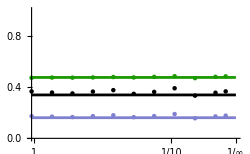

```mathematica
plotA=Show[
Plot[CVherd/.xmax->ymax/.ymax->(1-x)^tryV,{x,0,1},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[CVind,{x,0,1},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[(CVind/CVherd/.xmax->ymax/.ymax->(1-x)^tryV),{x,0,1},PlotStyle->Black],
ListPlot[forplottingherdA,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[forplottingindA,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Table[{forplottingindA[[i,1]],forplottingindA[[i,2]]/forplottingherdA[[i,2]]},{i,1,Length[forplottingindA]}],PlotStyle->{Black}],
AxesOrigin->{0,0},
PlotRange->{{0,1},{0,1}},
Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel B: Asymmetric contraction leading to elongated ranges [xmax/ymax along x axis]

```mathematica
SeedRandom[21773];
```

We seek to examine a range of ymax from 0 to 1, holding xmax=1. In our plots, we’ll show xmax/ymax along the x-axis using values of x from 0 to 1. To do so, we define ymax = (1-x)^V, which allows us to vary xmax/ymax from 1 at x=0 to infinity at x=1. V allows us to change the midpoint, which we set to 2, so that a value of x=1/2 corresponds to xmax/ymax=4. To convert the x-axis to ymax, we use 1-ymax^(1/V):

```mathematica
tryV=2;
```

```mathematica
Solve[ymax==(1-x)^V,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1-ymax^(1/V)}}

```mathematica
tab=Join[Table[i,{i,0,9/10,1/10}]]//Flatten
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10}

```mathematica
tryxmax=1;
```

```mathematica
numind=100;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Table[RandomReal[UniformDistribution[{{0,tryxmax},{0,(1-tab[[t]])^tryV}}]],{i,1,numind}];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsim[tryxmax,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsim[tryxmax,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdB=Table[{tab[[t]],CVherdsim[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.47049},{1/10,0.491607},{1/5,0.507825},{3/10,0.537111},{2/5,0.568451},{1/2,0.62333},{3/5,0.663144},{7/10,0.685779},{4/5,0.694607},{9/10,0.701092}}

```mathematica
forplottingindB=Table[{tab[[t]],CVindsim[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.157596},{1/10,0.176405},{1/5,0.164852},{3/10,0.193088},{2/5,0.175682},{1/2,0.195336},{3/5,0.198762},{7/10,0.189041},{4/5,0.21651},{9/10,0.223265}}

Below, we’ll want the ratio of CVind/CVherd in the limit for a very elongated range:

```mathematica
limratio=Limit[CVind1/CVherd/.xmax->tryxmax,ymax->Infinity]
```

1/(√10)

To label the x axis:

```mathematica
{x,tryxmax/(1-x)^tryV}/.x->tab//MatrixForm
```

(0 | 1/10 | 1/5 | 3/10 | 2/5 | 1/2 | 3/5 | 7/10 | 4/5 | 9/10
1 | 100/81 | 25/16 | 100/49 | 25/9 | 4 | 25/4 | 100/9 | 25 | 100)

```mathematica
Select[x/.Solve[1/(1-x)^tryV==10,x],#<1&]
```

{1/10 (10-√10)}

```mathematica
xticks={{0.01,"1"},{1/2 (2-√2),"2"},{1/2,"4"},{1/10 (10-√10),"10"},{4/5,"25"},{9/10,"100"},{1,"∞"}}
```

{{0.01,1},{1/2 (2-√2),2},{1/2,4},{1/10 (10-√10),10},{4/5,25},{9/10,100},{1,∞}}

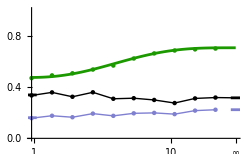

```mathematica
plot1=Show[
Plot[CVherd/.xmax->tryxmax/.ymax->(1-x)^tryV,{x,0,0.999},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[CVind,{x,-0.025,0.025},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVind1,{x,0.975,1.025},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[(CVind/CVherd/.xmax->tryxmax/.ymax->tryxmax),{x,-0.025,0.025},PlotStyle->Black],
Plot[limratio,{x,0.975,1.025},PlotStyle->Black],
ListPlot[forplottingherdB,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[forplottingindB,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[forplottingindB,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]},Joined->True],
ListPlot[Table[{forplottingindB[[i,1]],forplottingindB[[i,2]]/forplottingherdB[[i,2]]},{i,1,Length[forplottingindB]}],PlotStyle->{Black}],
ListPlot[Join[Table[{forplottingindB[[i,1]],forplottingindB[[i,2]]/forplottingherdB[[i,2]]},{i,1,Length[forplottingindB]}],{{1,limratio}}],Joined->True,PlotStyle->{Black,Thin}],
AxesOrigin->{0,0},
PlotRange->{{0,1},{0,1}},
Ticks->{xticks,Automatic},ImageSize->250
]
```

Dividing CVind by CVherd gives very similar answers in the 1D and symmetrical 2D cases (at opposite ends of this “elongation” axis). While the dashed line looks flat, the values are not exactly the same.

```mathematica
{CVind/(CVherd/.xmax->1/.ymax->1),CVind1/CVherd1}//N
```

{0.338924,0.316228}

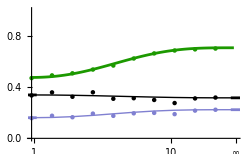

```mathematica
plotB=Show[
Plot[CVherd/.xmax->tryxmax/.ymax->(1-x)^tryV,{x,0,0.99},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[CVind,{x,-0.025,0.025},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVind1,{x,0.975,1.025},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[(CVind/CVherd/.xmax->tryxmax/.ymax->tryxmax),{x,-0.025,0.025},PlotStyle->Black],
Plot[limratio,{x,0.975,1.025},PlotStyle->Black],
ListPlot[forplottingherdB,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[forplottingindB,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[intplottingindB,{{1,CVind1}}],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingindB[[i,1]],forplottingindB[[i,2]]/forplottingherdB[[i,2]]},{i,1,Length[forplottingindB]}],PlotStyle->{Black}],
ListPlot[Join[Table[{intplottingindB[[i,1]],intplottingindB[[i,2]]/(CVherd/.xmax->tryxmax/.ymax->(1-tab[[i]])^tryV)},{i,1,Length[intplottingindB]}],{{1,limratio}}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,1},{0,1}},
Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel B: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate. Integration was inaccurate and so we first simplify and then take the limit as c approaches its numerical value:

```mathematica
tryc=0;
```

```mathematica
meanTEMP=Simplify[Limit[soln+(f xmax)/(30  α^2) ((((1+Subscript[c, s])^5-2(1+α^5+Subscript[c, s]^5))+2 H (1-3 α^2+α^4)+2 H2 (α^2-α Subscript[c, s]-Subscript[c, s]^2) (α^2+α Subscript[c, s]-Subscript[c, s]^2)- H1 (-1+α+α^2-(-2+α) Subscript[c, s]-Subscript[c, s]^2) (-1-α+α^2+(2+α) Subscript[c, s]-Subscript[c, s]^2)+H3 (-1+α+α^2+(-2+α) Subscript[c, s]-Subscript[c, s]^2) (1+α-α^2+(2+α) Subscript[c, s]+Subscript[c, s]^2)+H4^5)+5/4 α Log[(H+α)^-4 ((H1+α)/H4)^(2 (-1+Subscript[c, s])^4)  (Subscript[c, s]/(H2+α))^(4 Subscript[c, s]^4) ((H3+α)/(1+Subscript[c, s]))^(2 (1+Subscript[c, s])^4) ((α/(1+H))^2(1+H3+Subscript[c, s])/(-1+H1+Subscript[c, s]))^(2 α^3)(((-1+H1+Subscript[c, s]) (1+H3+Subscript[c, s]))/(H2+Subscript[c, s])^2)^(2 α^3 Subscript[c, s]) ])/.{H->√(1+α^2),H1->√(α^2+(-1+Subscript[c, s])^2),H2->√(α^2+Subscript[c, s]^2),H3->√(α^2+(1+Subscript[c, s])^2),H4->√((-1+Subscript[c, s])^2)}/.Subscript[c, s]->c/xmax/.α ->ymax/xmax/.xmax->tryxmax/.f->tryf,c->tryc],ymax≥0]
```

1/(30 ymax^2)(2+2 ymax^5-2 √(1+ymax^2)+6 ymax^2 √(1+ymax^2)-2 ymax^4 √(1+ymax^2)+5 ymax^4 Log[(1+√(1+ymax^2))/ymax]+5 ymax Log[ymax+√(1+ymax^2)])

```mathematica
For[t=1,t≤Length[tab],t++,
tryymax=(1-tab[[t]])^tryV;
mean=N[Limit[meanTEMP,ymax->tryymax],20];
sqH=(xmax^2+ymax^2)/6+c^2 f/.xmax->tryxmax/.ymax->tryymax/.f->tryf/.c->tryc;

CVherdintC[tryxmax,tab[[t]]]=N[Sqrt[sqH-mean^2]/mean,20];
CVindintC[tryxmax,tab[[t]]]=N[Sqrt[sqI[tryxmax,tryymax,tryc,tryf]-mean^2]/mean,20];Print[{CVherdintC[tryxmax,tab[[t]]],CVindintC[tryxmax,tab[[t]]]}]
]
```

{0.4755049270417650133,0.16116}

{0.4822380026918243942,0.163129}

{0.5035605163459533908,0.169341}

{0.5382485852563119834,0.179356}

{0.5811678976675914237,0.191519}

{0.6248567012527921603,0.203509}

{0.6620715792330464921,0.213227}

{0.6880902245050734449,0.219553}

{0.7019998219304748962,0.222623}

{0.7066416337749279018,0.223529}

```mathematica
intplottingherdB=Table[{tab[[t]],CVherdintC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.4755049270417650133},{1/10,0.4822380026918243942},{1/5,0.5035605163459533908},{3/10,0.5382485852563119834},{2/5,0.5811678976675914237},{1/2,0.6248567012527921603},{3/5,0.6620715792330464921},{7/10,0.6880902245050734449},{4/5,0.7019998219304748962},{9/10,0.7066416337749279018}}

```mathematica
intplottingindB=Table[{tab[[t]],CVindintC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.16116},{1/10,0.163129},{1/5,0.169341},{3/10,0.179356},{2/5,0.191519},{1/2,0.203509},{3/5,0.213227},{7/10,0.219553},{4/5,0.222623},{9/10,0.223529}}

#### Panel C: Even herd split [midpoint at c=4]

```mathematica
SeedRandom[32912];
```

We seek to examine a range of distances, c, between the peaks. To do so, we use c/(V+c) along the x-axis, which allows us to vary c from 0 at x=0 to infinity at x=1, within a single plot (we use V = 4 so that patches 4 sd apart are half-way along the plot). To convert the x-axis to c, we use:

```mathematica
tryV=4;
```

```mathematica
Solve[c/(tryV+c)==x,c]
```

{{c→-(4 x)/(-1+x)}}

```mathematica
tab=Join[Table[i,{i,0/10,4/20,1/20}],Table[i,{i,3/10,9/10,1/10}]]//Flatten
```

{0,1/20,1/10,3/20,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10}

```mathematica
numind1=50;
numind2=50;
numind=numind1+numind2;
```

```mathematica
tryf=2 (numind2/numind)(numind1/numind) (*Unequal split with 95% in one patch so f = 0.095*)
```

1/2

```mathematica
trymax=1;
tryxmax=trymax;
tryymax=trymax;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Join[Table[RandomReal[UniformDistribution[{{0,tryxmax},{0,tryymax}}]],{i,1,numind1}],Table[RandomReal[UniformDistribution[{{(tryV tab[[t]])/(1-tab[[t]]),(tryV tab[[t]])/(1-tab[[t]])+tryxmax},{0,tryymax}}]],{i,1,numind2}]];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsimC[tryxmax,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsimC[tryxmax,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdC=Table[{tab[[t]],CVherdsimC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.475331},{1/20,0.487266},{1/10,0.495214},{3/20,0.524657},{1/5,0.53443},{3/10,0.626007},{2/5,0.69305},{1/2,0.78026},{3/5,0.838624},{7/10,0.89089},{4/5,0.929399},{9/10,0.961288}}

```mathematica
forplottingindC=Table[{tab[[t]],CVindsimC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.173211},{1/20,0.182847},{1/10,0.203726},{3/20,0.227707},{1/5,0.188517},{3/10,0.125227},{2/5,0.100634},{1/2,0.0657055},{3/5,0.0490179},{7/10,0.0290495},{4/5,0.0192999},{9/10,0.00768273}}

```mathematica
maxc=1;
```

Below, we’ll want the ratio of CVind/CVherd in the limit for very distant patches when the patches are even:

```mathematica
limratio=Limit[CVindfarsplit/CVherdC/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c->Infinity]
```

0

We also plot CVherd in the limit for very distant patches when the patches are even:

```mathematica
limratioHERD=Limit[CVherdC/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c->Infinity]
```

1

Choosing x-axis tick positions:

```mathematica
{x,(tryV x)/(1-x)}/.x->tab//Transpose
```

{{0,0},{1/20,4/19},{1/10,4/9},{3/20,12/17},{1/5,1},{3/10,12/7},{2/5,8/3},{1/2,4},{3/5,6},{7/10,28/3},{4/5,16},{9/10,36}}

```mathematica
Solve[(tryV x)/(1-x)==2,x]
```

{{x→1/3}}

```mathematica
xticks={{0.01,"0"},{1/5,"1"},{1/3,"2"},{1/2,"4"},{3/5,"6"},{4/5,"16"},{9/10,"36"},{1,"∞"}}
```

{{0.01,0},{1/5,1},{1/3,2},{1/2,4},{3/5,6},{4/5,16},{9/10,36},{1,∞}}

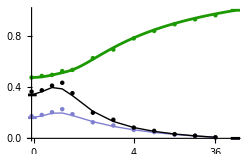

```mathematica
plotC=Show[
Plot[CVherdC/.xmax->trymax/.ymax->trymax/.f->tryf/.c->(tryV x)/(1-x),{x,0,maxc},WorkingPrecision->50,PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[limratioHERD,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVind/.xmax->tryxmax/.ymax->tryymax,{x,-0.025,0.025},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVindfarsplit/.xmax->tryxmax/.ymax->tryymax/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVind/CVherd/.xmax->tryxmax/.ymax->tryymax,{x,-0.025,0.025},PlotStyle->Black],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdC,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[forplottingindC,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[intplottingindC,Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingherdC[[i,1]],forplottingindC[[i,2]]/forplottingherdC[[i,2]]},{i,1,Length[forplottingindC]}],PlotStyle->{Black}],
ListPlot[Table[{intplottingindC[[i,1]],intplottingindC[[i,2]]/intplottingherdC[[i,2]]},{i,1,Length[forplottingindC]}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,1}},Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel C: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate. Integration was inaccurate and so we first simplify and then take the limit as c approaches its numerical value:

```mathematica
meanTEMP=Simplify[soln+(f xmax)/(30  α^2) ((((1+Subscript[c, s])^5-2(1+α^5+Subscript[c, s]^5))+2 H (1-3 α^2+α^4)+2 H2 (α^2-α Subscript[c, s]-Subscript[c, s]^2) (α^2+α Subscript[c, s]-Subscript[c, s]^2)- H1 (-1+α+α^2-(-2+α) Subscript[c, s]-Subscript[c, s]^2) (-1-α+α^2+(2+α) Subscript[c, s]-Subscript[c, s]^2)+H3 (-1+α+α^2+(-2+α) Subscript[c, s]-Subscript[c, s]^2) (1+α-α^2+(2+α) Subscript[c, s]+Subscript[c, s]^2)+H4^5)+5/4 α Log[(H+α)^-4 ((H1+α)/H4)^(2 (-1+Subscript[c, s])^4)  (Subscript[c, s]/(H2+α))^(4 Subscript[c, s]^4) ((H3+α)/(1+Subscript[c, s]))^(2 (1+Subscript[c, s])^4) ((α/(1+H))^2(1+H3+Subscript[c, s])/(-1+H1+Subscript[c, s]))^(2 α^3)(((-1+H1+Subscript[c, s]) (1+H3+Subscript[c, s]))/(H2+Subscript[c, s])^2)^(2 α^3 Subscript[c, s]) ])/.{H->√(1+α^2),H1->√(α^2+(-1+Subscript[c, s])^2),H2->√(α^2+Subscript[c, s]^2),H3->√(α^2+(1+Subscript[c, s])^2),H4->√((-1+Subscript[c, s])^2)}/.Subscript[c, s]->c/xmax/.α ->ymax/xmax/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c≥0]
```

1/60 (8+2 √2+(1+c)^5-(1-3 c+c^2) √(2-2 c+c^2) (-1-c+c^2)+2 √(1+c^2) (-1-c+c^2) (-1+c+c^2)-(-1+c+c^2) √(2+2 c+c^2) (1+3 c+c^2)-2 (2+c^5)+Abs[-1+c]^5+20 Log[1+√2]+5/4 Log[1/(1+√2)^8(1+√(1+(-1+c)^2))^(2 (-1+c)^4) (-1+√(1+(-1+c)^2)+c)^(2 (-1+c)) (c/(1+√(1+c^2)))^(4 c^4) (c+√(1+c^2))^(-4 c) ((1+c)/(1+√(1+(1+c)^2)))^(-2 (1+c)^4) (1+c+√(1+(1+c)^2))^(2 (1+c)) Abs[-1+c]^(-2 (-1+c)^4)])

```mathematica
For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=N[Limit[meanTEMP,c->tryc],20];
sqH=(xmax^2+ymax^2)/6+c^2 f/.xmax->tryxmax/.ymax->tryymax/.f->tryf/.c->tryc;

CVherdintC[tryxmax,tab[[t]]]=N[Sqrt[sqH-mean^2]/mean,20];
CVindintC[trymax,tab[[t]]]=N[Sqrt[sqI[trymax,tryc,tryf]-mean^2]/mean,20];Print[{CVherdintC[trymax,tab[[t]]],CVindintC[trymax,tab[[t]]]}]
]
```

{0.4755049270417650133,0.16116}

{0.4801301308897845306,0.174868}

{0.4942647559954516806,0.196181}

{0.5124231934169125522,0.197843}

{0.5354324213836169643,0.178548}

{0.6169607285366896165,0.130382}

{0.7075649576679686667,0.0933431}

{0.7845745273644130115,0.0663114}

{0.8467525018809703436,0.0461015}

{0.8968935093634621468,0.0305338}

{0.9377919470044052127,0.018212}

{0.9716244129419319288,0.00823386}

```mathematica
intplottingherdC=Table[{tab[[t]],CVherdintC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.4755049270417650133},{1/20,0.4801301308897845306},{1/10,0.4942647559954516806},{3/20,0.5124231934169125522},{1/5,0.5354324213836169643},{3/10,0.6169607285366896165},{2/5,0.7075649576679686667},{1/2,0.7845745273644130115},{3/5,0.8467525018809703436},{7/10,0.8968935093634621468},{4/5,0.9377919470044052127},{9/10,0.9716244129419319288}}

```mathematica
intplottingindC=Table[{tab[[t]],CVindintC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.16116},{1/20,0.174868},{1/10,0.196181},{3/20,0.197843},{1/5,0.178548},{3/10,0.130382},{2/5,0.0933431},{1/2,0.0663114},{3/5,0.0461015},{7/10,0.0305338},{4/5,0.018212},{9/10,0.00823386}}

#### Panel D: Uneven herd split [midpoint at c=4]

```mathematica
SeedRandom[43812];
```

We seek to examine a range of distances, c, between the peaks. To do so, we use c/(V+c) along the x-axis, which allows us to vary c from 0 at x=0 to infinity at x=1, within a single plot (we use V = 4 so that patches 4 sd apart are half-way along the plot). To convert the x-axis to c, we use:

```mathematica
tryV=4;
```

```mathematica
Solve[c/(tryV+c)==x,c]
```

{{c→-(4 x)/(-1+x)}}

```mathematica
tab=Join[Table[i,{i,0/10,4/20,1/20}],Table[i,{i,3/10,9/10,1/10}]]//Flatten
```

{0,1/20,1/10,3/20,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10}

```mathematica
numind1=90;
numind2=10;
numind=numind1+numind2;
```

```mathematica
tryf=2 (numind2/numind)(numind1/numind) (*Unequal split with 90% in one patch so f = 0.18*)
```

9/50

```mathematica
trymax=1;
tryxmax=trymax;
tryymax=trymax;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Join[Table[RandomReal[UniformDistribution[{{0,tryxmax},{0,tryymax}}]],{i,1,numind1}],Table[RandomReal[UniformDistribution[{{(tryV tab[[t]])/(1-tab[[t]]),(tryV tab[[t]])/(1-tab[[t]])+tryxmax},{0,tryymax}}]],{i,1,numind2}]];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsimC[tryxmax,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsimC[tryxmax,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdD=Table[{tab[[t]],CVherdsimC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.474266},{1/20,0.470027},{1/10,0.484829},{3/20,0.483136},{1/5,0.57089},{3/10,0.798745},{2/5,0.960725},{1/2,1.22076},{3/5,1.41601},{7/10,1.58171},{4/5,1.81007},{9/10,1.96378}}

```mathematica
forplottingindD=Table[{tab[[t]],CVindsimC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.16428},{1/20,0.160544},{1/10,0.183164},{3/20,0.191312},{1/5,0.284328},{3/10,0.470485},{2/5,0.583888},{1/2,0.761376},{3/5,0.887567},{7/10,0.998112},{4/5,1.1435},{9/10,1.24055}}

```mathematica
maxc=1;
```

Below, we’ll want the ratio of CVind/CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratio=Limit[CVindfarsplit/CVherdC/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c->Infinity]//N
```

0.624695

We also plot CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratioHERD=Limit[CVherdC/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c->Infinity]//N
```

2.13437

Choosing x-axis tick positions:

```mathematica
{x,(tryV x)/(1-x)}/.x->tab//Transpose
```

{{0,0},{1/20,4/19},{1/10,4/9},{3/20,12/17},{1/5,1},{3/10,12/7},{2/5,8/3},{1/2,4},{3/5,6},{7/10,28/3},{4/5,16},{9/10,36}}

```mathematica
Solve[(tryV x)/(1-x)==2,x]
```

{{x→1/3}}

```mathematica
xticks={{0.01,"0"},{1/5,"1"},{1/3,"2"},{1/2,"4"},{3/5,"6"},{4/5,"16"},{9/10,"36"},{1,"∞"}}
```

{{0.01,0},{1/5,1},{1/3,2},{1/2,4},{3/5,6},{4/5,16},{9/10,36},{1,∞}}

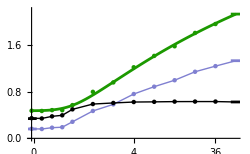

```mathematica
Show[
Plot[CVherdC/.xmax->trymax/.ymax->trymax/.f->tryf/.c->(tryV x)/(1-x),{x,0,maxc},WorkingPrecision->50,PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[limratioHERD,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVind/.xmax->tryxmax/.ymax->tryymax,{x,-0.025,0.025},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVindfarsplit/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVind/CVherd/.xmax->tryxmax/.ymax->tryymax,{x,-0.025,0.025},PlotStyle->Black],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdD,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[forplottingindD,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[forplottingindD,{{1,CVindfarsplit/.f->tryf}}],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingherdD[[i,1]],forplottingindD[[i,2]]/forplottingherdD[[i,2]]},{i,1,Length[forplottingindD]}],PlotStyle->{Black}],
ListPlot[Join[Table[{forplottingherdD[[i,1]],forplottingindD[[i,2]]/forplottingherdD[[i,2]]},{i,1,Length[forplottingindD]}],{{1,limratio}}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,2.2}},Ticks->{xticks,Automatic},ImageSize->250
]
```

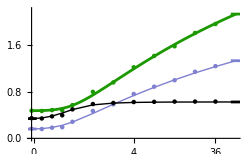

```mathematica
plotD=Show[
Plot[CVherdC/.xmax->trymax/.ymax->trymax/.f->tryf/.c->(tryV x)/(1-x),{x,0,maxc},WorkingPrecision->50,PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[limratioHERD,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVind/.xmax->tryxmax/.ymax->tryymax,{x,-0.025,0.025},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVindfarsplit/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVind/CVherd/.xmax->tryxmax/.ymax->tryymax,{x,-0.025,0.025},PlotStyle->Black],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdD,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[forplottingindD,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[intplottingindD,{{1,CVindfarsplit/.f->tryf}}],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingherdD[[i,1]],forplottingindD[[i,2]]/forplottingherdD[[i,2]]},{i,1,Length[forplottingindD]}],PlotStyle->{Black}],
ListPlot[Join[Table[{intplottingindD[[i,1]],intplottingindD[[i,2]]/intplottingherdD[[i,2]]},{i,1,Length[forplottingindD]}],{{1,limratio}}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,2.2}},Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel D: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate. Integration was inaccurate and so we first simplify and then take the limit as c approaches its numerical value:

```mathematica
meanTEMP=Simplify[soln+(f xmax)/(30  α^2) ((((1+Subscript[c, s])^5-2(1+α^5+Subscript[c, s]^5))+2 H (1-3 α^2+α^4)+2 H2 (α^2-α Subscript[c, s]-Subscript[c, s]^2) (α^2+α Subscript[c, s]-Subscript[c, s]^2)- H1 (-1+α+α^2-(-2+α) Subscript[c, s]-Subscript[c, s]^2) (-1-α+α^2+(2+α) Subscript[c, s]-Subscript[c, s]^2)+H3 (-1+α+α^2+(-2+α) Subscript[c, s]-Subscript[c, s]^2) (1+α-α^2+(2+α) Subscript[c, s]+Subscript[c, s]^2)+H4^5)+5/4 α Log[(H+α)^-4 ((H1+α)/H4)^(2 (-1+Subscript[c, s])^4)  (Subscript[c, s]/(H2+α))^(4 Subscript[c, s]^4) ((H3+α)/(1+Subscript[c, s]))^(2 (1+Subscript[c, s])^4) ((α/(1+H))^2(1+H3+Subscript[c, s])/(-1+H1+Subscript[c, s]))^(2 α^3)(((-1+H1+Subscript[c, s]) (1+H3+Subscript[c, s]))/(H2+Subscript[c, s])^2)^(2 α^3 Subscript[c, s]) ])/.{H->√(1+α^2),H1->√(α^2+(-1+Subscript[c, s])^2),H2->√(α^2+Subscript[c, s]^2),H3->√(α^2+(1+Subscript[c, s])^2),H4->√((-1+Subscript[c, s])^2)}/.Subscript[c, s]->c/xmax/.α ->ymax/xmax/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c≥0]
```

2/15+(√2)/15+1/3 Log[1+√2]+3/500 (-2 √2+(1+c)^5-(1-3 c+c^2) √(2-2 c+c^2) (-1-c+c^2)+2 √(1+c^2) (-1-c+c^2) (-1+c+c^2)-(-1+c+c^2) √(2+2 c+c^2) (1+3 c+c^2)-2 (2+c^5)+Abs[-1+c]^5+5/4 Log[1/(1+√2)^8(1+√(1+(-1+c)^2))^(2 (-1+c)^4) (-1+√(1+(-1+c)^2)+c)^(2 (-1+c)) (c/(1+√(1+c^2)))^(4 c^4) (c+√(1+c^2))^(-4 c) ((1+c)/(1+√(1+(1+c)^2)))^(-2 (1+c)^4) (1+c+√(1+(1+c)^2))^(2 (1+c)) Abs[-1+c]^(-2 (-1+c)^4)])

```mathematica
For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=N[Limit[meanTEMP,c->tryc],20];
sqH=(xmax^2+ymax^2)/6+c^2 f/.xmax->tryxmax/.ymax->tryymax/.f->tryf/.c->tryc;

CVherdintC[tryxmax,tab[[t]]]=N[Sqrt[sqH-mean^2]/mean,20];
CVindintC[tryxmax,tab[[t]]]=N[Sqrt[sqI[tryxmax,tryc,tryf]-mean^2]/mean,20];Print[{CVherdintC[trymax,tab[[t]]],CVindintC[tryxmax,tab[[t]]]}]
]
```

{0.4755049270417650133,0.16116}

{0.4775163517603715289,0.167081}

{0.4879628917409243562,0.186761}

{0.5150387657378148952,0.22388}

{0.5664045746687243068,0.279918}

{0.743896213947195823,0.427474}

{0.9666853844938108845,0.585175}

{1.193390931536194245,0.736027}

{1.409945802103042397,0.87613}

{1.61234834952651222,1.00514}

{1.800046641135843841,1.12372}

{1.973701515109571924,1.2328}

```mathematica
intplottingherdD=Table[{tab[[t]],CVherdintC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.4755049270417650133},{1/20,0.4775163517603715289},{1/10,0.4879628917409243562},{3/20,0.5150387657378148952},{1/5,0.5664045746687243068},{3/10,0.743896213947195823},{2/5,0.9666853844938108845},{1/2,1.193390931536194245},{3/5,1.409945802103042397},{7/10,1.61234834952651222},{4/5,1.800046641135843841},{9/10,1.973701515109571924}}

```mathematica
intplottingindD=Table[{tab[[t]],CVindintC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.16116},{1/20,0.167081},{1/10,0.186761},{3/20,0.22388},{1/5,0.279918},{3/10,0.427474},{2/5,0.585175},{1/2,0.736027},{3/5,0.87613},{7/10,1.00514},{4/5,1.12372},{9/10,1.2328}}

#### Panel E: Even herd split with elongated patches [ymax short]

```mathematica
SeedRandom[59238];
```

We seek to examine a range of distances, c, between the peaks, now allowing each patch to be elongated. To do so, we use c/(V+c) along the x-axis, which allows us to vary c from 0 at x=0 to infinity at x=1, within a single plot (we use V = 4 so that patches 4 sd apart are half-way along the plot). To convert the x-axis to c, we use:

```mathematica
tryV=4;
```

```mathematica
Solve[c/(tryV+c)==x,c]
```

{{c→-(4 x)/(-1+x)}}

```mathematica
tab=Join[Table[i,{i,0/10,2/10,1/20}],Table[i,{i,3/10,9/10,1/10}]]//Flatten
```

{0,1/20,1/10,3/20,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10}

```mathematica
numind1=50;
numind2=50;
numind=numind1+numind2;
```

```mathematica
tryf=2 (numind2/numind)(numind1/numind) (*Equal split with 50% in one patch so f = 1/2*)
```

1/2

```mathematica
tryxmax=1;
tryymax=1/5;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Join[Table[RandomReal[UniformDistribution[{{0,tryxmax},{0,tryymax}}]],{i,1,numind1}],Table[RandomReal[UniformDistribution[{{(tryV tab[[t]])/(1-tab[[t]]),(tryV tab[[t]])/(1-tab[[t]])+tryxmax},{0,tryymax}}]],{i,1,numind2}]];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsimC[tryxmax,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsimC[tryxmax,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdE=Table[{tab[[t]],CVherdsimC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.65269},{1/20,0.651785},{1/10,0.681042},{3/20,0.681407},{1/5,0.679038},{3/10,0.722538},{2/5,0.792907},{1/2,0.853867},{3/5,0.890349},{7/10,0.91603},{4/5,0.94696},{9/10,0.97109}}

```mathematica
forplottingindE=Table[{tab[[t]],CVindsimC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.215848},{1/20,0.243695},{1/10,0.295809},{3/20,0.267889},{1/5,0.229122},{3/10,0.147649},{2/5,0.0951801},{1/2,0.0614867},{3/5,0.0379738},{7/10,0.0323404},{4/5,0.0175789},{9/10,0.00834784}}

Below, we’ll want the ratio of CVind/CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratio=Limit[CVindfarsplit/CVherdC/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c->Infinity]
```

0

We also plot CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
CVherdfar=Limit[CVherdC/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c->Infinity]
```

1

```mathematica
maxc=1;
```

```mathematica
xticks={{0.01,"0"},{1/5,"1"},{1/3,"2"},{1/2,"4"},{3/5,"6"},{4/5,"16"},{9/10,"36"},{1,"∞"}}
```

{{0.01,0},{1/5,1},{1/3,2},{1/2,4},{3/5,6},{4/5,16},{9/10,36},{1,∞}}

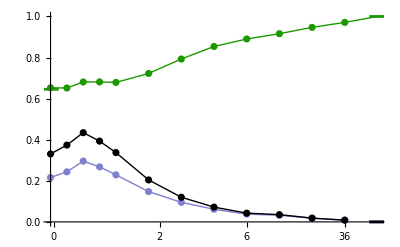

```mathematica
plotE=Show[
Plot[CVherdfar,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVindfarsplit/.xmax->tryxmax/.ymax->tryymax/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVherd/.xmax->tryxmax/.ymax->tryymax,{x,-0.025,0.025},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdE,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[Join[forplottingherdE,{{1,CVherdfar}}],Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[forplottingindE,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[forplottingindE,Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingherdE[[i,1]],forplottingindE[[i,2]]/forplottingherdE[[i,2]]},{i,1,Length[forplottingindE]}],PlotStyle->{Black}],
ListPlot[Table[{forplottingherdE[[i,1]],forplottingindE[[i,2]]/forplottingherdE[[i,2]]},{i,1,Length[forplottingindE]}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,1}},Ticks->{xticks,Automatic}
]
```

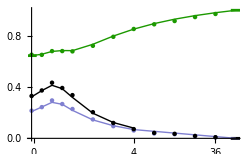

```mathematica
plotE=Show[
Plot[CVherdfar,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVindfarsplit/.xmax->tryxmax/.ymax->tryymax/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVherd/.xmax->tryxmax/.ymax->tryymax,{x,-0.025,0.025},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdE,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[Join[intplottingherdE,{{1,CVherdfar}}],Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[forplottingindE,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[intplottingindE,{{1,CVindfarsplit/.f->tryf}}],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingherdE[[i,1]],forplottingindE[[i,2]]/forplottingherdE[[i,2]]},{i,1,Length[forplottingindE]}],PlotStyle->{Black}],
ListPlot[Table[{intplottingherdE[[i,1]],intplottingindE[[i,2]]/intplottingherdE[[i,2]]},{i,1,Length[intplottingindE]}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,1}},Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel E: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate. Integration was inaccurate and so we first simplify and then take the limit as c approaches its numerical value:

```mathematica
meanTEMP=Simplify[soln+(f xmax)/(30  α^2) ((((1+Subscript[c, s])^5-2(1+α^5+Subscript[c, s]^5))+2 H (1-3 α^2+α^4)+2 H2 (α^2-α Subscript[c, s]-Subscript[c, s]^2) (α^2+α Subscript[c, s]-Subscript[c, s]^2)- H1 (-1+α+α^2-(-2+α) Subscript[c, s]-Subscript[c, s]^2) (-1-α+α^2+(2+α) Subscript[c, s]-Subscript[c, s]^2)+H3 (-1+α+α^2+(-2+α) Subscript[c, s]-Subscript[c, s]^2) (1+α-α^2+(2+α) Subscript[c, s]+Subscript[c, s]^2)+H4^5)+5/4 α Log[(H+α)^-4 ((H1+α)/H4)^(2 (-1+Subscript[c, s])^4)  (Subscript[c, s]/(H2+α))^(4 Subscript[c, s]^4) ((H3+α)/(1+Subscript[c, s]))^(2 (1+Subscript[c, s])^4) ((α/(1+H))^2(1+H3+Subscript[c, s])/(-1+H1+Subscript[c, s]))^(2 α^3)(((-1+H1+Subscript[c, s]) (1+H3+Subscript[c, s]))/(H2+Subscript[c, s])^2)^(2 α^3 Subscript[c, s]) ])/.{H->√(1+α^2),H1->√(α^2+(-1+Subscript[c, s])^2),H2->√(α^2+Subscript[c, s]^2),H3->√(α^2+(1+Subscript[c, s])^2),H4->√((-1+Subscript[c, s])^2)}/.Subscript[c, s]->c/xmax/.α ->ymax/xmax/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c≥0]
```

1042/625-(551 √26)/1875+1/150 (125 Log[1/5 (1+√26)]+Log[5+√26])+5/12 ((1102 √26)/3125+(1+c)^5-((29-55 c+25 c^2) √(26-50 c+25 c^2) (19-45 c+25 c^2))/3125+(2 √(1+25 c^2) (-1-5 c+25 c^2) (-1+5 c+25 c^2))/3125-2 (3126/3125+c^5)+(-19/25-(9 c)/5-c^2) (29/25+(11 c)/5+c^2) √(1/25+(1+c)^2)+Abs[-1+c]^5+1/4 Log[(5^(-24 c^2) (c/(1+√(1+25 c^2)))^(4 c^4) (5 c+√(1+25 c^2))^(-4 c/125) (1+√(26-50 c+25 c^2))^(2 (-1+c)^4) (-5+5 c+√(26-50 c+25 c^2))^(2/125 (-1+c)) ((1+c)/(1+√(26+50 c+25 c^2)))^(-2 (1+c)^4) (5+5 c+√(26+50 c+25 c^2))^((2 (1+c))/125) Abs[-1+c]^(-2 (-1+c)^4))/((1+√26)^4 (5+√26)^(4/125))])

```mathematica
For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=N[Limit[meanTEMP,c->tryc],20];
sqH=(xmax^2+ymax^2)/6+c^2 f/.xmax->tryxmax/.ymax->tryymax/.f->tryf/.c->tryc;

CVherdintC[tryxmax,tab[[t]]]=N[Sqrt[sqH-mean^2]/mean,20];
CVindintC[tryxmax,tab[[t]]]=N[Sqrt[sqI[tryxmax,tryymax,tryc,tryf]-mean^2]/mean,20];Print[{CVherdintC[tryxmax,tab[[t]]],CVindintC[tryxmax,tab[[t]]]}]
]
```

{0.6456877909802461191,0.209022}

{0.6564504908685524942,0.244649}

{0.6785197070168401252,0.28109}

{0.6853889458045307584,0.265716}

{0.6847161800752769921,0.218766}

{0.7343507160965991353,0.143969}

{0.7986818887932470375,0.0986395}

{0.8528021120433971568,0.0684358}

{0.8958894823253643301,0.0468901}

{0.9302599510489040393,0.0307513}

{0.9580661386616496218,0.0182129}

{0.9809238877024275145,0.0081917}

```mathematica
intplottingherdE=Table[{tab[[t]],CVherdintC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.6456877909802461191},{1/20,0.6564504908685524942},{1/10,0.6785197070168401252},{3/20,0.6853889458045307584},{1/5,0.6847161800752769921},{3/10,0.7343507160965991353},{2/5,0.7986818887932470375},{1/2,0.8528021120433971568},{3/5,0.8958894823253643301},{7/10,0.9302599510489040393},{4/5,0.9580661386616496218},{9/10,0.9809238877024275145}}

```mathematica
intplottingindE=Table[{tab[[t]],CVindintC[tryxmax,tab[[t]]]},{t,1,8}]
```

{{0,0.209022},{1/20,0.244649},{1/10,0.28109},{3/20,0.265716},{1/5,0.218766},{3/10,0.143969},{2/5,0.0986395},{1/2,0.0684358}}

#### Panel F: Uneven herd split with elongated patches [ymax short]

```mathematica
SeedRandom[66127];
```

We seek to examine a range of distances, c, between the peaks, now allowing each patch to be elongated. To do so, we use c/(V+c) along the x-axis, which allows us to vary c from 0 at x=0 to infinity at x=1, within a single plot (we use V = 4 so that patches 4 sd apart are half-way along the plot). To convert the x-axis to c, we use:

```mathematica
tryV=4;
```

```mathematica
Solve[c/(tryV+c)==x,c]
```

{{c→-(4 x)/(-1+x)}}

```mathematica
tab=Join[Table[i,{i,0/10,9/10,1/10}]]//Flatten
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10}

```mathematica
numind1=90;
numind2=10;
numind=numind1+numind2;
```

```mathematica
tryf=2 (numind2/numind)(numind1/numind) (*Unequal split with 90% in one patch so f = 0.18*)
```

9/50

```mathematica
tryxmax=1;
tryymax=1/5;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Join[Table[RandomReal[UniformDistribution[{{0,tryxmax},{0,tryymax}}]],{i,1,numind1}],Table[RandomReal[UniformDistribution[{{(tryV tab[[t]])/(1-tab[[t]]),(tryV tab[[t]])/(1-tab[[t]])+tryxmax},{0,tryymax}}]],{i,1,numind2}]];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsimC[tryxmax,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsimC[tryxmax,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdF=Table[{tab[[t]],CVherdsimC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.65037},{1/10,0.663809},{1/5,0.793686},{3/10,1.0085},{2/5,1.21359},{1/2,1.4339},{3/5,1.60634},{7/10,1.73474},{4/5,1.88707},{9/10,2.01019}}

```mathematica
forplottingindF=Table[{tab[[t]],CVindsimC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.219119},{1/10,0.270121},{1/5,0.414427},{3/10,0.60206},{2/5,0.745494},{1/2,0.897708},{3/5,1.01159},{7/10,1.09366},{4/5,1.19192},{9/10,1.2694}}

Below, we’ll want the ratio of CVind/CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratio=Limit[CVindfarsplit/CVherdC/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c->Infinity]
```

400/(√(410000-4 Log[2]^2-Log[4]^2+Log[4] Log[16]))

We also plot CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
Simplify[CVherdC/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c>1];
CVherdfar=Limit[%,c->Infinity]
```

(√41)/3

```mathematica
maxc=1;
```

```mathematica
xticks={{0.01,"0"},{1/5,"1"},{1/3,"2"},{1/2,"4"},{3/5,"6"},{4/5,"16"},{9/10,"36"},{1,"∞"}}
```

{{0.01,0},{1/5,1},{1/3,2},{1/2,4},{3/5,6},{4/5,16},{9/10,36},{1,∞}}

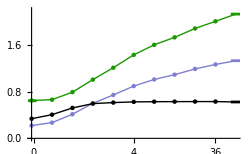

```mathematica
plotF=Show[
Plot[CVherdfar,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVindfarsplit/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVherd/.xmax->tryxmax/.ymax->tryymax,{x,-0.025,0.025},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdF,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[Join[forplottingherdF,{{1,CVherdfar}}],Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[forplottingindF,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[forplottingindF,{{1,CVindfarsplit/.f->tryf}}],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingherdF[[i,1]],forplottingindF[[i,2]]/forplottingherdF[[i,2]]},{i,1,Length[forplottingindF]}],PlotStyle->{Black}],
ListPlot[Join[Table[{forplottingherdF[[i,1]],forplottingindF[[i,2]]/forplottingherdF[[i,2]]},{i,1,Length[forplottingindF]}],{{1,limratio}}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,2.2}},Ticks->{xticks,Automatic},ImageSize->250
]
```

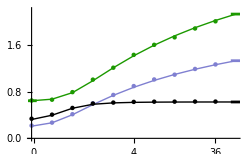

```mathematica
plotF=Show[
Plot[CVherdfar,{x,0.975,1.05},PlotStyle->{RGBColor[0.11,0.6,0.]},PlotRange->All],
Plot[CVindfarsplit/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVherd/.xmax->tryxmax/.ymax->tryymax,{x,-0.025,0.025},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdF,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[Join[intplottingherdF,{{1,CVherdfar}}],Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[forplottingindF,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[intplottingindF,{{1,CVindfarsplit/.f->tryf}}],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]},PlotRange->All],
ListPlot[Table[{forplottingherdF[[i,1]],forplottingindF[[i,2]]/forplottingherdF[[i,2]]},{i,1,Length[forplottingindF]}],PlotStyle->{Black}],
ListPlot[Join[Table[{intplottingherdF[[i,1]],intplottingindF[[i,2]]/intplottingherdF[[i,2]]},{i,1,Length[intplottingindF]}],{{1,limratio}}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,2.2}},Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel F: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate. Integration was inaccurate and so we first simplify and then take the limit as c approaches its numerical value:

```mathematica
meanTEMP=Simplify[soln+(f xmax)/(30  α^2) ((((1+Subscript[c, s])^5-2(1+α^5+Subscript[c, s]^5))+2 H (1-3 α^2+α^4)+2 H2 (α^2-α Subscript[c, s]-Subscript[c, s]^2) (α^2+α Subscript[c, s]-Subscript[c, s]^2)- H1 (-1+α+α^2-(-2+α) Subscript[c, s]-Subscript[c, s]^2) (-1-α+α^2+(2+α) Subscript[c, s]-Subscript[c, s]^2)+H3 (-1+α+α^2+(-2+α) Subscript[c, s]-Subscript[c, s]^2) (1+α-α^2+(2+α) Subscript[c, s]+Subscript[c, s]^2)+H4^5)+5/4 α Log[(H+α)^-4 ((H1+α)/H4)^(2 (-1+Subscript[c, s])^4)  (Subscript[c, s]/(H2+α))^(4 Subscript[c, s]^4) ((H3+α)/(1+Subscript[c, s]))^(2 (1+Subscript[c, s])^4) ((α/(1+H))^2(1+H3+Subscript[c, s])/(-1+H1+Subscript[c, s]))^(2 α^3)(((-1+H1+Subscript[c, s]) (1+H3+Subscript[c, s]))/(H2+Subscript[c, s])^2)^(2 α^3 Subscript[c, s]) ])/.{H->√(1+α^2),H1->√(α^2+(-1+Subscript[c, s])^2),H2->√(α^2+Subscript[c, s]^2),H3->√(α^2+(1+Subscript[c, s])^2),H4->√((-1+Subscript[c, s])^2)}/.Subscript[c, s]->c/xmax/.α ->ymax/xmax/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c≥0]
```

1042/625-(551 √26)/1875+1/150 (125 Log[1/5 (1+√26)]+Log[5+√26])+3/20 ((1102 √26)/3125+(1+c)^5-((29-55 c+25 c^2) √(26-50 c+25 c^2) (19-45 c+25 c^2))/3125+(2 √(1+25 c^2) (-1-5 c+25 c^2) (-1+5 c+25 c^2))/3125-2 (3126/3125+c^5)+(-19/25-(9 c)/5-c^2) (29/25+(11 c)/5+c^2) √(1/25+(1+c)^2)+Abs[-1+c]^5+1/4 Log[1/((1+√26)^4 (5+√26)^(4/125))5^(-24 c^2) (c/(1+√(1+25 c^2)))^(4 c^4) (5 c+√(1+25 c^2))^(-4 c/125) (1+√(26-50 c+25 c^2))^(2 (-1+c)^4) (-5+5 c+√(26-50 c+25 c^2))^(2/125 (-1+c)) ((1+c)/(1+√(26+50 c+25 c^2)))^(-2 (1+c)^4) (5+5 c+√(26+50 c+25 c^2))^((2 (1+c))/125) Abs[-1+c]^(-2 (-1+c)^4)])

```mathematica
For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=N[Limit[meanTEMP,c->tryc],20];
sqH=(xmax^2+ymax^2)/6+c^2 f/.xmax->tryxmax/.ymax->tryymax/.f->tryf/.c->tryc;

CVherdintC[tryxmax,tab[[t]]]=N[Sqrt[sqH-mean^2]/mean,20];
CVindintC[tryxmax,tab[[t]]]=N[Sqrt[sqI[tryxmax,tryymax,tryc,tryf]-mean^2]/mean,20];Print[{CVherdintC[tryxmax,tab[[t]]],CVindintC[tryxmax,tab[[t]]]}]
]
```

{0.6456877909802461191,0.209022}

{0.6726141069407129428,0.26716}

{0.7848943583382700488,0.405781}

{0.9893559257920512755,0.578939}

{1.212529226442353135,0.738577}

{1.418204657239621433,0.876644}

{1.600291382773758638,0.995234}

{1.760109799946668596,1.09758}

{1.900530189552676495,1.18655}

{2.024441835701119692,1.26452}

```mathematica
intplottingherdF=Table[{tab[[t]],CVherdintC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.6456877909802461191},{1/10,0.6726141069407129428},{1/5,0.7848943583382700488},{3/10,0.9893559257920512755},{2/5,1.212529226442353135},{1/2,1.418204657239621433},{3/5,1.600291382773758638},{7/10,1.760109799946668596},{4/5,1.900530189552676495},{9/10,2.024441835701119692}}

```mathematica
intplottingindF=Table[{tab[[t]],CVindintC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.209022},{1/10,0.26716},{1/5,0.405781},{3/10,0.578939},{2/5,0.738577},{1/2,0.876644},{3/5,0.995234},{7/10,1.09758},{4/5,1.18655},{9/10,1.26452}}

#### Panel G: Even herd split with elongated patches [ymax long]

```mathematica
SeedRandom[77212];
```

We seek to examine a range of distances, c, between the peaks, now allowing each patch to be elongated. To do so, we use c/(V+c) along the x-axis, which allows us to vary c from 0 at x=0 to infinity at x=1, within a single plot (we use V = 4 so that patches 4 sd apart are half-way along the plot). To convert the x-axis to c, we use:

```mathematica
tryV=4;
```

```mathematica
Solve[c/(tryV+c)==x,c]
```

{{c→-(4 x)/(-1+x)}}

```mathematica
tab=Join[Table[i,{i,0/10,9/10,1/10}]]//Flatten
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10}

```mathematica
numind1=50;
numind2=50;
numind=100;
```

```mathematica
tryf=2 (numind2/numind)(numind1/numind) (*Equal split with 50% in one patch so f = 1/2*)
```

1/2

```mathematica
tryxmax=1;
tryymax=5;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Join[Table[RandomReal[UniformDistribution[{{0,tryxmax},{0,tryymax}}]],{i,1,numind1}],Table[RandomReal[UniformDistribution[{{(tryV tab[[t]])/(1-tab[[t]]),(tryV tab[[t]])/(1-tab[[t]])+tryxmax},{0,tryymax}}]],{i,1,numind2}]];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsimC[tryxmax,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsimC[tryxmax,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdG=Table[{tab[[t]],CVherdsimC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.63467},{1/10,0.615477},{1/5,0.555801},{3/10,0.502156},{2/5,0.495109},{1/2,0.525298},{3/5,0.602384},{7/10,0.704638},{4/5,0.815552},{9/10,0.900771}}

```mathematica
forplottingindG=Table[{tab[[t]],CVindsimC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.203677},{1/10,0.252975},{1/5,0.179129},{3/10,0.156466},{2/5,0.121663},{1/2,0.100978},{3/5,0.0688491},{7/10,0.0445305},{4/5,0.0329098},{9/10,0.0134876}}

Below, we’ll want the ratio of CVind/CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratio=Limit[CVindfarsplit/CVherdC/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c->Infinity]
```

0

We also plot CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
Simplify[CVherdC/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c>1];
CVherdfar=Limit[%,c->Infinity]
```

1

```mathematica
maxc=1;
```

```mathematica
Solve[(tryV x)/(1-x)==6,x]
```

{{x→3/5}}

```mathematica
xticks={{0.01,"0"},{1/5,"1"},{1/3,"2"},{1/2,"4"},{3/5,"6"},{4/5,"16"},{9/10,"36"},{1,"∞"}}
```

{{0.01,0},{1/5,1},{1/3,2},{1/2,4},{3/5,6},{4/5,16},{9/10,36},{1,∞}}

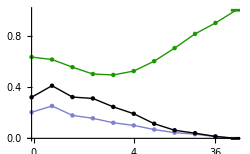

```mathematica
plotG=Show[
Plot[CVherdfar,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVindfarsplit/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVherd/.xmax->tryxmax/.ymax->tryymax,{x,-0.025,0.025},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdG,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[Join[forplottingherdG,{{1,CVherdfar}}],Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[forplottingindG,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[forplottingindG,{{1,CVindfarsplit/.f->tryf}}],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingherdG[[i,1]],forplottingindG[[i,2]]/forplottingherdG[[i,2]]},{i,1,Length[forplottingindG]}],PlotStyle->{Black}],
ListPlot[Join[Table[{forplottingherdG[[i,1]],forplottingindG[[i,2]]/forplottingherdG[[i,2]]},{i,1,Length[forplottingindG]}],{{1,limratio}}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,1}},Ticks->{xticks,Automatic},ImageSize->250
]
```

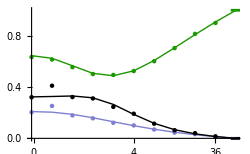

```mathematica
plotG=Show[
Plot[CVherdfar,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVindfarsplit/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVherd/.xmax->tryxmax/.ymax->tryymax,{x,-0.025,0.025},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdG,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[Join[intplottingherdG,{{1,CVherdfar}}],Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[forplottingindG,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[intplottingindG,{{1,CVindfarsplit/.f->tryf}}],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{forplottingherdG[[i,1]],forplottingindG[[i,2]]/forplottingherdG[[i,2]]},{i,1,Length[forplottingindG]}],PlotStyle->{Black}],
ListPlot[Join[Table[{intplottingherdG[[i,1]],intplottingindG[[i,2]]/intplottingherdG[[i,2]]},{i,1,Length[intplottingindG]}],{{1,limratio}}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,1}},Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel G: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate. Integration was inaccurate and so we first simplify and then take the limit as c approaches its numerical value:

```mathematica
meanTEMP=Simplify[soln+(f xmax)/(30  α^2) ((((1+Subscript[c, s])^5-2(1+α^5+Subscript[c, s]^5))+2 H (1-3 α^2+α^4)+2 H2 (α^2-α Subscript[c, s]-Subscript[c, s]^2) (α^2+α Subscript[c, s]-Subscript[c, s]^2)- H1 (-1+α+α^2-(-2+α) Subscript[c, s]-Subscript[c, s]^2) (-1-α+α^2+(2+α) Subscript[c, s]-Subscript[c, s]^2)+H3 (-1+α+α^2+(-2+α) Subscript[c, s]-Subscript[c, s]^2) (1+α-α^2+(2+α) Subscript[c, s]+Subscript[c, s]^2)+H4^5)+5/4 α Log[(H+α)^-4 ((H1+α)/H4)^(2 (-1+Subscript[c, s])^4)  (Subscript[c, s]/(H2+α))^(4 Subscript[c, s]^4) ((H3+α)/(1+Subscript[c, s]))^(2 (1+Subscript[c, s])^4) ((α/(1+H))^2(1+H3+Subscript[c, s])/(-1+H1+Subscript[c, s]))^(2 α^3)(((-1+H1+Subscript[c, s]) (1+H3+Subscript[c, s]))/(H2+Subscript[c, s])^2)^(2 α^3 Subscript[c, s]) ])/.{H->√(1+α^2),H1->√(α^2+(-1+Subscript[c, s])^2),H2->√(α^2+Subscript[c, s]^2),H3->√(α^2+(1+Subscript[c, s])^2),H4->√((-1+Subscript[c, s])^2)}/.Subscript[c, s]->c/xmax/.α ->ymax/xmax/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c≥0]
```

1/1500(12504-1102 √26+(1+c)^5-(-19-7 c+c^2) √(26-2 c+c^2) (-29+3 c+c^2)+2 √(25+c^2) (-25-5 c+c^2) (-25+5 c+c^2)+(29+3 c-c^2) √(26+2 c+c^2) (-19+7 c+c^2)-2 (3126+c^5)+Abs[-1+c]^5+50 (125 Log[1/5 (1+√26)]+Log[5+√26])+25/4 Log[(30549363634996046820519793932136176997894027405723266638936139092812916265247204577018572351080152282568751526935904671553178534278042839697351331142009178896307244205337728522220355888195318837008165086679301794879136633899370525163649789227021200352450820912190874482021196014946372110934030798550767828365183620409339937395998276770114898681640625 ((5+√(25+(-1+c)^2))/(√((-1+c)^2)))^(2 (-1+c)^4) (c/(5+√(25+c^2)))^(4 c^4) ((5+√(25+(1+c)^2))/(1+c))^(2 (1+c)^4) (1+c+√(25+(1+c)^2))^250 (((-1+√(25+(-1+c)^2)+c) (1+c+√(25+(1+c)^2)))/((c+√(25+c^2))^2))^(250 c))/((1+√26)^500 (5+√26)^4 (-1+√(25+(-1+c)^2)+c)^250)])

```mathematica
For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=N[Limit[meanTEMP,c->tryc],20];
sqH=(xmax^2+ymax^2)/6+c^2 f/.xmax->tryxmax/.ymax->tryymax/.f->tryf/.c->tryc;

CVherdintC[tryxmax,tab[[t]]]=N[Sqrt[sqH-mean^2]/mean,20];
CVindintC[tryxmax,tab[[t]]]=N[Sqrt[sqI[tryxmax,tryymax,tryc,tryf]-mean^2]/mean,20];Print[{CVherdintC[tryxmax,tab[[t]]],CVindintC[tryxmax,tab[[t]]]}]
]
```

{0.6456877909802461191,0.209022}

{0.6249669682390801206,0.204264}

{0.5667721406605546949,0.187473}

{0.5073851200907658822,0.160621}

{0.4888278688972020791,0.129537}

{0.5272574266623707615,0.0987984}

{0.6078424280028319966,0.071197}

{0.7072676067712154196,0.0478076}

{0.8100289075250711776,0.0285568}

{0.9086010837792124169,0.012853}

```mathematica
intplottingherdG=Table[{tab[[t]],CVherdintC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.6456877909802461191},{1/10,0.6249669682390801206},{1/5,0.5667721406605546949},{3/10,0.5073851200907658822},{2/5,0.4888278688972020791},{1/2,0.5272574266623707615},{3/5,0.6078424280028319966},{7/10,0.7072676067712154196},{4/5,0.8100289075250711776},{9/10,0.9086010837792124169}}

```mathematica
intplottingindG=Table[{tab[[t]],CVindintC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.209022},{1/10,0.204264},{1/5,0.187473},{3/10,0.160621},{2/5,0.129537},{1/2,0.0987984},{3/5,0.071197},{7/10,0.0478076},{4/5,0.0285568},{9/10,0.012853}}

#### Panel H: Uneven herd split with elongated patches [ymax long]

```mathematica
SeedRandom[827523];
```

We seek to examine a range of distances, c, between the peaks, now allowing each patch to be elongated. To do so, we use c/(V+c) along the x-axis, which allows us to vary c from 0 at x=0 to infinity at x=1, within a single plot (we use V = 4 so that patches 4 sd apart are half-way along the plot). To convert the x-axis to c, we use:

```mathematica
tryV=4;
```

```mathematica
Solve[c/(tryV+c)==x,c]
```

{{c→-(4 x)/(-1+x)}}

```mathematica
tab=Join[Table[i,{i,0/10,9/10,1/10}]]//Flatten
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10}

```mathematica
numind1=90;
numind2=10;
numind=numind1+numind2;
```

```mathematica
tryf=2 (numind2/numind)(numind1/numind) (*Unequal split with 90% in one patch so f = 0.18*)
```

9/50

```mathematica
tryxmax=1;
tryymax=5;
```

```mathematica
For[t=1,t≤Length[tab],t++,
table=Join[Table[RandomReal[UniformDistribution[{{0,tryxmax},{0,tryymax}}]],{i,1,numind1}],Table[RandomReal[UniformDistribution[{{(tryV tab[[t]])/(1-tab[[t]]),(tryV tab[[t]])/(1-tab[[t]])+tryxmax},{0,tryymax}}]],{i,1,numind2}]];
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
CVherdsimC[tryxmax,tab[[t]]]=StandardDeviation[disttable]/Mean[disttable];
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
CVindsimC[tryxmax,tab[[t]]]=StandardDeviation[disttable2]/Mean[disttable2]
]
```

```mathematica
forplottingherdH=Table[{tab[[t]],CVherdsimC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.64555},{1/10,0.647195},{1/5,0.624738},{3/10,0.595356},{2/5,0.599694},{1/2,0.650181},{3/5,0.821925},{7/10,0.973951},{4/5,1.28448},{9/10,1.68513}}

```mathematica
forplottingindH=Table[{tab[[t]],CVindsimC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.189993},{1/10,0.20105},{1/5,0.197965},{3/10,0.238172},{2/5,0.231567},{1/2,0.304318},{3/5,0.474573},{7/10,0.581909},{4/5,0.801142},{9/10,1.06177}}

Below, we’ll want the ratio of CVind/CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
limratio=Limit[CVindfarsplit/CVherdC/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c->Infinity]
```

4/(√41)

We also plot CVherd in the limit for very distant patches when the patches are uneven:

```mathematica
Simplify[CVherdC/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c>1];
CVherdfar=Limit[%,c->Infinity]
```

(√41)/3

```mathematica
maxc=1;
```

```mathematica
xticks={{0.01,"0"},{1/5,"1"},{1/3,"2"},{1/2,"4"},{3/5,"6"},{4/5,"16"},{9/10,"36"},{1,"∞"}}
```

{{0.01,0},{1/5,1},{1/3,2},{1/2,4},{3/5,6},{4/5,16},{9/10,36},{1,∞}}

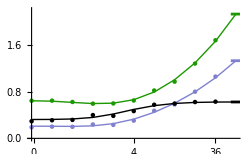

```mathematica
plotH=Show[
Plot[CVherdfar,{x,0.975,1.05},PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
Plot[CVindfarsplit/.f->tryf,{x,0.975,1.05},PlotStyle->RGBColor[0.5,0.5,0.82]],
Plot[CVherd/.xmax->tryxmax/.ymax->tryymax,{x,-0.025,0.025},PlotStyle->RGBColor[0.11,0.6,0.]],
Plot[limratio,{x,0.975,1.05},PlotStyle->Black],
ListPlot[forplottingherdH,PlotStyle->RGBColor[0.11,0.6,0.]],
ListPlot[Join[intplottingherdH,{{1,CVherdfar}}],Joined->True,PlotStyle->{Thin,RGBColor[0.11,0.6,0.]}],
ListPlot[forplottingindH,PlotStyle->RGBColor[0.5,0.5,0.82]],
ListPlot[Join[intplottingindH,{{1,CVindfarsplit/.f->tryf}}],Joined->True,PlotStyle->{Thin,RGBColor[0.5,0.5,0.82]},PlotRange->All],
ListPlot[Table[{forplottingherdH[[i,1]],forplottingindH[[i,2]]/forplottingherdH[[i,2]]},{i,1,Length[forplottingindH]}],PlotStyle->{Black}],
ListPlot[Join[Table[{intplottingherdH[[i,1]],intplottingindH[[i,2]]/intplottingherdH[[i,2]]},{i,1,Length[intplottingindH]}],{{1,limratio}}],Joined->True,PlotStyle->{Thin,Black}],
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,2.2}},Ticks->{xticks,Automatic},ImageSize->250
]
```

#### Panel H: Numerical integration [SLOW - Don’t enter]

For comparison, we can numerically integrate. Integration was inaccurate and so we first simplify and then take the limit as c approaches its numerical value:

```mathematica
meanTEMP=Simplify[soln+(f xmax)/(30  α^2) ((((1+Subscript[c, s])^5-2(1+α^5+Subscript[c, s]^5))+2 H (1-3 α^2+α^4)+2 H2 (α^2-α Subscript[c, s]-Subscript[c, s]^2) (α^2+α Subscript[c, s]-Subscript[c, s]^2)- H1 (-1+α+α^2-(-2+α) Subscript[c, s]-Subscript[c, s]^2) (-1-α+α^2+(2+α) Subscript[c, s]-Subscript[c, s]^2)+H3 (-1+α+α^2+(-2+α) Subscript[c, s]-Subscript[c, s]^2) (1+α-α^2+(2+α) Subscript[c, s]+Subscript[c, s]^2)+H4^5)+5/4 α Log[(H+α)^-4 ((H1+α)/H4)^(2 (-1+Subscript[c, s])^4)  (Subscript[c, s]/(H2+α))^(4 Subscript[c, s]^4) ((H3+α)/(1+Subscript[c, s]))^(2 (1+Subscript[c, s])^4) ((α/(1+H))^2(1+H3+Subscript[c, s])/(-1+H1+Subscript[c, s]))^(2 α^3)(((-1+H1+Subscript[c, s]) (1+H3+Subscript[c, s]))/(H2+Subscript[c, s])^2)^(2 α^3 Subscript[c, s]) ])/.{H->√(1+α^2),H1->√(α^2+(-1+Subscript[c, s])^2),H2->√(α^2+Subscript[c, s]^2),H3->√(α^2+(1+Subscript[c, s])^2),H4->√((-1+Subscript[c, s])^2)}/.Subscript[c, s]->c/xmax/.α ->ymax/xmax/.xmax->tryxmax/.ymax->tryymax/.f->tryf,c≥0]
```

1/37500(312600-45182 √26+9 (1+c)^5-9 (-19-7 c+c^2) √(26-2 c+c^2) (-29+3 c+c^2)+18 √(25+c^2) (-25-5 c+c^2) (-25+5 c+c^2)-9 (-29-3 c+c^2) √(26+2 c+c^2) (-19+7 c+c^2)-18 (3126+c^5)+9 Abs[-1+c]^5+1250 (125 Log[1/5 (1+√26)]+Log[5+√26])+225/4 Log[(30549363634996046820519793932136176997894027405723266638936139092812916265247204577018572351080152282568751526935904671553178534278042839697351331142009178896307244205337728522220355888195318837008165086679301794879136633899370525163649789227021200352450820912190874482021196014946372110934030798550767828365183620409339937395998276770114898681640625 ((5+√(25+(-1+c)^2))/(√((-1+c)^2)))^(2 (-1+c)^4) (c/(5+√(25+c^2)))^(4 c^4) ((5+√(25+(1+c)^2))/(1+c))^(2 (1+c)^4) (1+c+√(25+(1+c)^2))^250 (((-1+√(25+(-1+c)^2)+c) (1+c+√(25+(1+c)^2)))/((c+√(25+c^2))^2))^(250 c))/((1+√26)^500 (5+√26)^4 (-1+√(25+(-1+c)^2)+c)^250)])

```mathematica
For[t=1,t≤Length[tab],t++,
tryc=(tryV tab[[t]])/(1-tab[[t]]);
mean=N[Limit[meanTEMP,c->tryc],20];
sqH=(xmax^2+ymax^2)/6+c^2 f/.xmax->tryxmax/.ymax->tryymax/.f->tryf/.c->tryc;

CVherdintC[tryxmax,tab[[t]]]=N[Sqrt[sqH-mean^2]/mean,20];
CVindintC[tryxmax,tab[[t]]]=N[Sqrt[sqI[tryxmax,tryymax,tryc,tryf]-mean^2]/mean,20];Print[{CVherdintC[tryxmax,tab[[t]]],CVindintC[tryxmax,tab[[t]]]}]
]
```

{0.6456877909802461191,0.209022}

{0.6382173336190422852,0.207524}

{0.6172818531644725514,0.205481}

{0.5979012682139712844,0.214711}

{0.6044261845933080114,0.252541}

{0.6638665661780649766,0.329672}

{0.7958159315818981299,0.44703}

{1.006425308266586006,0.603241}

{1.296108079565853422,0.799359}

{1.66849469042825828,1.0399}

```mathematica
intplottingherdH=Table[{tab[[t]],CVherdintC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.6456877909802461191},{1/10,0.6382173336190422852},{1/5,0.6172818531644725514},{3/10,0.5979012682139712844},{2/5,0.6044261845933080114},{1/2,0.6638665661780649766},{3/5,0.7958159315818981299},{7/10,1.006425308266586006},{4/5,1.296108079565853422},{9/10,1.66849469042825828}}

```mathematica
intplottingindH=Table[{tab[[t]],CVindintC[tryxmax,tab[[t]]]},{t,1,Length[tab]}]
```

{{0,0.209022},{1/10,0.207524},{1/5,0.205481},{3/10,0.214711},{2/5,0.252541},{1/2,0.329672},{3/5,0.44703},{7/10,0.603241},{4/5,0.799359},{9/10,1.0399}}

#### Altogether

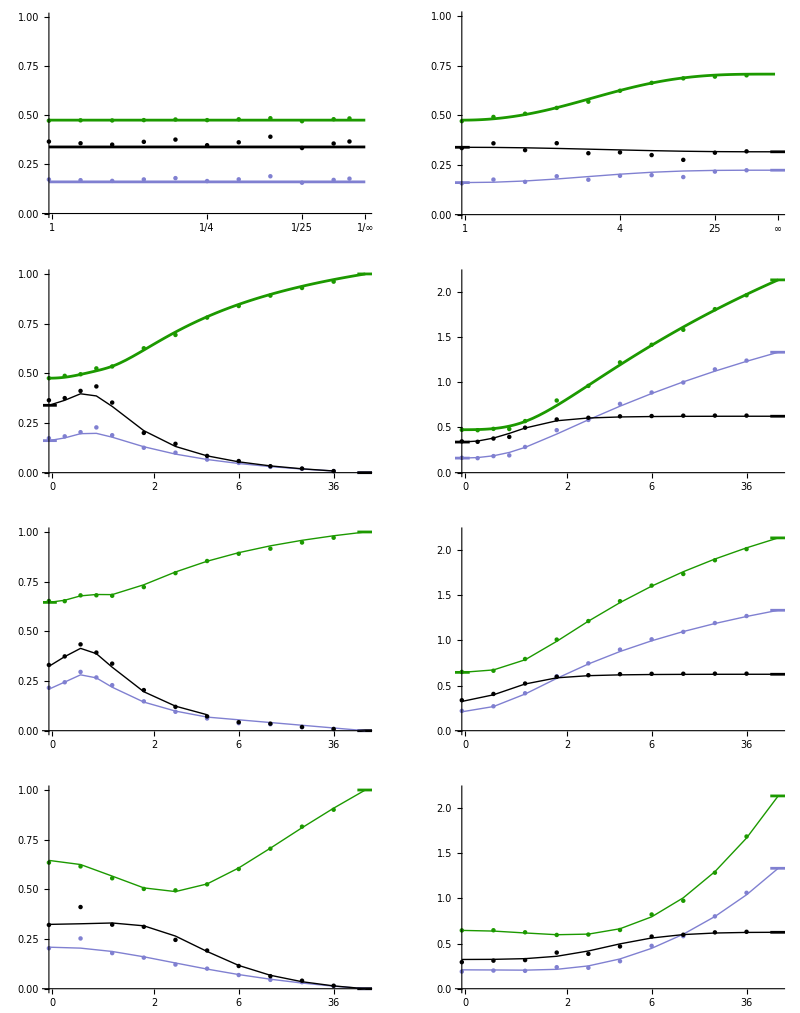

```mathematica
GraphicsGrid[{{plotA,plotB},{plotC,plotD},{plotE,plotF},{plotG,plotH}}]
```

## Individuals distributed uniformly across an elliptical range

### Simulation only

5000 individuals were simulated from the given population distribution (more individuals to get a more accurate estimate).

Ranges were drawn from a uniform disk, either circular with radius r or elliptical with radii r1 and r2.

#### Herd with a circular range (CV_herd~0.469, CV_ind~0.147)

```mathematica
SeedRandom[748645];
```

Assume a random distribution of individuals (blue):

```mathematica
tryr=1;
numind=5000;
```

```mathematica
table=RandomPoint[Disk[{0,0},tryr],numind];
```

Calculating the mean Euclidean distance for all pairwise distances (blue)

This table includes all of the pairwise distances:

```mathematica
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
```

The mean and SD:

```mathematica
{ Mean[disttable],StandardDeviation[disttable]}
```

{0.908522,0.425707}

The coefficient of variation across the herd (CV_herd):

```mathematica
StandardDeviation[disttable]/Mean[disttable]
```

0.468571

Looking instead at how far, on average, each individual is to all others, then calculating the CV in this value among individuals (CV_ind):

```mathematica
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
```

The mean and SD:

```mathematica
{Mean[disttable2],StandardDeviation[disttable2]}
```

{0.908522,0.133448}

Because of the averaging that occurs for each individual’s average pairwise distance, we get a lower CV_ind:

```mathematica
StandardDeviation[disttable2]/Mean[disttable2]
```

0.146885

#### Herd with a very elongated range (CV_herd~0.710, CV_ind~0.256)

```mathematica
SeedRandom[748645];
```

Assume a random distribution of individuals (blue):

```mathematica
tryr1=1;
tryr2=10^6;
numind=5000;
```

```mathematica
table=RandomPoint[Disk[{0,0},{tryr1,tryr2}],numind];
```

Calculating the mean Euclidean distance for all pairwise distances (blue)

This table includes all of the pairwise distances:

```mathematica
disttable=Flatten[Table[EuclideanDistance[table[[i]],table[[j]]],{i,1,numind},{j,i+1,numind}]];
```

The mean and SD:

```mathematica
{ Mean[disttable],StandardDeviation[disttable]}
```

{580988.,412674.}

The coefficient of variation across the herd (CV_herd):

```mathematica
StandardDeviation[disttable]/Mean[disttable]
```

0.710298

Looking instead at how far, on average, each individual is to all others, then calculating the CV in this value among individuals (CV_ind):

```mathematica
disttable2=Table[1/(Length[table]-1)(Sum[EuclideanDistance[table[[i]],table[[j]]],{j,1,i-1}]+Sum[EuclideanDistance[table[[i]],table[[j]]],{j,i+1,numind}]),{i,1,numind}];
```

The mean and SD:

```mathematica
{Mean[disttable2],StandardDeviation[disttable2]}
```

{580988.,148566.}

Because of the averaging that occurs for each individual’s average pairwise distance, we get a lower CV_ind:

```mathematica
StandardDeviation[disttable2]/Mean[disttable2]
```

0.255713